# Using Mathematica V14.3 for Tensorial Analysis & Calculus

Abstract
“Tensorial Analysis” was originally developed by Renan Cabrera and later modified by Munehiro Shinabe (shinabe.munehiro@hotmail.co.jp). This tensor calculus package is designed for beginners and is well-suited for studying in reference to standard textbooks. Its beautifully formatted equations follow the notation commonly used in academic texts.
Last updated:  2025/10/30

```mathematica
Remove["Global`*"]
Remove["mshtensorial`*"]
Names["mshtensorial`*"]
packagefile="C:\\Users\\shina\\Desktop\\math_tensor\\msh_tensorial.wl"
(*dir =DirectoryName["C:\\Users\\shina\\Desktop\\math_tensor\\msh_tensorial.m"];*)
(*Get["msh_tensorial.m",Path->dir]*)
"Download the package msh_tensorial.wl."
(*Needs["mshtensorial`",packagefile]*)
Get[packagefile]
Names["Global`*"]
"List of functions and special characters in a package"
Names["mshtensorial`*"]
```

Remove::rmnsm: "mshtensorial`*"に合致するシンボルはありません．

{}

C:\Users\shina\Desktop\math_tensor\msh_tensorial.wl

Download the package msh_tensorial.wl.

{}

List of functions and special characters in a package

{AbsoluteDerivative,Christoffel1,Christoffel2,CovariantDerivative,DummyVariableSimplify,EinsteinTensor,EvaluateIndexDerivative,Expand2ndCODer,ExpandABSDer,ExpandChristoffel1,ExpandChristoffel2,ExpandCODer,ExpandDoubleIndex,ExpandIndex,ExpandIndexDerivativeUp,ExpandMat,ExpandRCC,ExpandRiccFor,ExpandRicci,IndexDerivative,IndexDerivativeSimplify,IndexDerivativeUp,Kronecker,KroneckerSimplify,LeviCivitaRule,MatTen,MetricSimplify,NDim,OrderChristoffel,OrderIndexDeri,OrderTensor,RiccFormula,RieChrisCur,SetSystem,SetTensorRule,Tensor,TensorSimplify,ToContravariantIndex,ToCovariantIndex,Void,x,x$,Γ,δ,ϵ,ξ,ρ,σ}

https://community.wolfram.com/groups/-/m/t/142857         Abstract  mathworld mathsource
https : // library . wolfram . com/infocenter/Demos/434/       Wolfram Library Archive
This package was created so that beginners can learn the basic theory of “tensor analysis” at the introductory level using Mathematica.

## 1.Introduction of Matrices and Tensor

## Tensor Definition

#### A tensor is an object that can be denoted by the Head Tensor and two lists keeping the conventional covariant and contravariant indexes.

```mathematica
TB1 =Tensor[B,{i,Void},{Void,j}]
```

B_i^j

#### We can expand a certain tensor with ExpandIndex[ Tensor, index]. Important: index must be always list !!

```mathematica
a( TB1+ Tensor[F,{i,Void},{Void,j}])
ExpandIndex[%, {i,j}];
MatrixForm[%]
```

a (B_i^j+F_i^j)

(a (B_1^1+F_1^1) | a (B_1^2+F_1^2) | a (B_1^3+F_1^3)
a (B_2^1+F_2^1) | a (B_2^2+F_2^2) | a (B_2^3+F_2^3)
a (B_3^1+F_3^1) | a (B_3^2+F_3^2) | a (B_3^3+F_3^3))

#### To expand tensors with double indexes we have to use explicitly the command ExpandDoubleIndex[ Tensor , double index ] . In this case double indexes are treated as dummy variables.

```mathematica
TB = Tensor[B,{Void ,i},{j}] Tensor[A,{Void,j} , {k}]
```

A_j^k B_i^j

```mathematica
NDim=3;
ExpandDoubleIndex[  TB, {j} ]
```

A_1^k B_i^1+A_2^k B_i^2+A_3^k B_i^3

```mathematica
ExpandIndex[%, {i,k} ];
MatrixForm[%]
```

(A_1^1 B_1^1+A_2^1 B_1^2+A_3^1 B_1^3 | A_1^2 B_1^1+A_2^2 B_1^2+A_3^2 B_1^3 | A_1^3 B_1^1+A_2^3 B_1^2+A_3^3 B_1^3
A_1^1 B_2^1+A_2^1 B_2^2+A_3^1 B_2^3 | A_1^2 B_2^1+A_2^2 B_2^2+A_3^2 B_2^3 | A_1^3 B_2^1+A_2^3 B_2^2+A_3^3 B_2^3
A_1^1 B_3^1+A_2^1 B_3^2+A_3^1 B_3^3 | A_1^2 B_3^1+A_2^2 B_3^2+A_3^2 B_3^3 | A_1^3 B_3^1+A_2^3 B_3^2+A_3^3 B_3^3)

```mathematica
(Tensor[A,{i,j},{Void,Void}]+ Tensor[A,{i,k},{Void,Void}])Tensor[B,{Void},{i}]

ExpandDoubleIndex[ % ,{i} ]
```

(A_ij^+A_ik^) B_^i

A_(1j)^ B_^1+A_(1k)^ B_^1+A_(2j)^ B_^2+A_(2k)^ B_^2+A_(3j)^ B_^3+A_(3k)^ B_^3

```mathematica
ExpandDoubleIndex[ Tensor[Q,{Void},{m}] + TB, {j} ]
```

A_1^k B_i^1+A_2^k B_i^2+A_3^k B_i^3+Q_^m

## Tensor functions built into Mathematica

#### TensorProduct ,TensorWedge

```mathematica
Remove["Global`*"]
Aa=ExpandIndex[Tensor[a,{Void},{i}],{i}];
Bb=ExpandIndex[Tensor[b,{j},{Void}],{j}];
AaBb=TensorProduct[Aa,Bb];
"Aa⊗Bb"==MatrixForm[AaBb]
ExpandIndex[Tensor[a,{Void},{i}]Tensor[b,{j},{Void}],{i,j}];
⟨Tensor[a,{Void},{i}]Tensor[b,{j},{Void}]⟩==MatrixForm[%]
"Aa\[TensorWedge]Bb"==MatrixForm[Normal[Aa\[TensorWedge]Bb]]

ExpandIndex[Tensor[a,{Void},{i}]Tensor[b,{j},{Void}] -Tensor[a,{Void},{j}]Tensor[b,{i},{Void}] ,{i,j}];
⟨Tensor[a,{Void},{i}]Tensor[b,{j},{Void}]-Tensor[a,{Void},{j}]Tensor[b,{i},{Void}]⟩==MatrixForm[%]
"Aa.Bb"==TensorContract[TensorProduct[Aa,Bb],{1,2}]
"Contraction of slots 1 and 2 of AaBb"
```

Aa⊗Bb==(a_^1 b_1^ | a_^1 b_2^ | a_^1 b_3^
a_^2 b_1^ | a_^2 b_2^ | a_^2 b_3^
a_^3 b_1^ | a_^3 b_2^ | a_^3 b_3^)

⟨a_^i b_j^⟩==(a_^1 b_1^ | a_^1 b_2^ | a_^1 b_3^
a_^2 b_1^ | a_^2 b_2^ | a_^2 b_3^
a_^3 b_1^ | a_^3 b_2^ | a_^3 b_3^)

Aa\[TensorWedge]Bb==(0 | -a_^2 b_1^+a_^1 b_2^ | -a_^3 b_1^+a_^1 b_3^
a_^2 b_1^-a_^1 b_2^ | 0 | -a_^3 b_2^+a_^2 b_3^
a_^3 b_1^-a_^1 b_3^ | a_^3 b_2^-a_^2 b_3^ | 0)

⟨-a_^j b_i^+a_^i b_j^⟩==(0 | -a_^2 b_1^+a_^1 b_2^ | -a_^3 b_1^+a_^1 b_3^
a_^2 b_1^-a_^1 b_2^ | 0 | -a_^3 b_2^+a_^2 b_3^
a_^3 b_1^-a_^1 b_3^ | a_^3 b_2^-a_^2 b_3^ | 0)

Aa.Bb==a_^1 b_1^+a_^2 b_2^+a_^3 b_3^

Contraction of slots 1 and 2 of AaBb

#### From TensorWedge to The cross product of two vectors.

```mathematica
1/2ExpandIndex[ExpandDoubleIndex[Tensor[ϵ,{Void},{i,j,k}](Tensor[a,{Void},{i}]Tensor[b,{j},{Void}] -Tensor[a,{Void},{j}]Tensor[b,{i},{Void}]) ,{i,j}],{k}]//Expand;
"Aa×Bb"==⟨1/2Tensor[ϵ,{Void},{i,j,k}]"(Aa\[TensorWedge]Bb)_ij"⟩==MatrixForm[%]
ExpandIndex[ExpandDoubleIndex[Tensor[ϵ,{Void},{r,s,k}]Tensor[ϵ,{k,i,j},{Void}]Tensor[a,{Void},{i}]Tensor[b,{j},{Void}],{i,j,k}],{r,s}];
"Aa\[TensorWedge]Bb"==⟨Tensor[ϵ,{Void},{r,s,k}]"(a×b)_k"⟩==MatrixForm[%]
```

Aa×Bb==⟨1/2 (Aa\[TensorWedge]Bb)_ij ϵ_^ijk⟩==(-a_^3 b_2^+a_^2 b_3^
a_^3 b_1^-a_^1 b_3^
-a_^2 b_1^+a_^1 b_2^)

Aa\[TensorWedge]Bb==⟨(a×b)_k ϵ_^rsk⟩==(0 | -a_^2 b_1^+a_^1 b_2^ | -a_^3 b_1^+a_^1 b_3^
a_^2 b_1^-a_^1 b_2^ | 0 | -a_^3 b_2^+a_^2 b_3^
a_^3 b_1^-a_^1 b_3^ | a_^3 b_2^-a_^2 b_3^ | 0)

#### TensorContract

```mathematica
Remove["Global`*"]
Aa=ExpandIndex[Tensor[a,{j,Void},{Void,i}],{i,j}];
Bb=ExpandIndex[Tensor[b,{j,Void},{Void,i}],{i,j}];
AaBb=TensorProduct[Aa,Bb];
MatrixForm[AaBb]
s1=Aa.Bb;
MatrixForm[s1]
Tensor[a,{j,Void},{Void,i}]Tensor[b,{k,Void},{Void,j}]
s2=ExpandIndex[ExpandDoubleIndex[%,{j}],{i,k}];
s1==s2
s1==TensorContract[AaBb,{2,3}]
"Contraction of slots 2 and 3 of AaBb"
```

((a_1^1 b_1^1 | a_1^1 b_2^1 | a_1^1 b_3^1
a_1^1 b_1^2 | a_1^1 b_2^2 | a_1^1 b_3^2
a_1^1 b_1^3 | a_1^1 b_2^3 | a_1^1 b_3^3) | (a_2^1 b_1^1 | a_2^1 b_2^1 | a_2^1 b_3^1
a_2^1 b_1^2 | a_2^1 b_2^2 | a_2^1 b_3^2
a_2^1 b_1^3 | a_2^1 b_2^3 | a_2^1 b_3^3) | (a_3^1 b_1^1 | a_3^1 b_2^1 | a_3^1 b_3^1
a_3^1 b_1^2 | a_3^1 b_2^2 | a_3^1 b_3^2
a_3^1 b_1^3 | a_3^1 b_2^3 | a_3^1 b_3^3)
(a_1^2 b_1^1 | a_1^2 b_2^1 | a_1^2 b_3^1
a_1^2 b_1^2 | a_1^2 b_2^2 | a_1^2 b_3^2
a_1^2 b_1^3 | a_1^2 b_2^3 | a_1^2 b_3^3) | (a_2^2 b_1^1 | a_2^2 b_2^1 | a_2^2 b_3^1
a_2^2 b_1^2 | a_2^2 b_2^2 | a_2^2 b_3^2
a_2^2 b_1^3 | a_2^2 b_2^3 | a_2^2 b_3^3) | (a_3^2 b_1^1 | a_3^2 b_2^1 | a_3^2 b_3^1
a_3^2 b_1^2 | a_3^2 b_2^2 | a_3^2 b_3^2
a_3^2 b_1^3 | a_3^2 b_2^3 | a_3^2 b_3^3)
(a_1^3 b_1^1 | a_1^3 b_2^1 | a_1^3 b_3^1
a_1^3 b_1^2 | a_1^3 b_2^2 | a_1^3 b_3^2
a_1^3 b_1^3 | a_1^3 b_2^3 | a_1^3 b_3^3) | (a_2^3 b_1^1 | a_2^3 b_2^1 | a_2^3 b_3^1
a_2^3 b_1^2 | a_2^3 b_2^2 | a_2^3 b_3^2
a_2^3 b_1^3 | a_2^3 b_2^3 | a_2^3 b_3^3) | (a_3^3 b_1^1 | a_3^3 b_2^1 | a_3^3 b_3^1
a_3^3 b_1^2 | a_3^3 b_2^2 | a_3^3 b_3^2
a_3^3 b_1^3 | a_3^3 b_2^3 | a_3^3 b_3^3))

(a_1^1 b_1^1+a_2^1 b_1^2+a_3^1 b_1^3 | a_1^1 b_2^1+a_2^1 b_2^2+a_3^1 b_2^3 | a_1^1 b_3^1+a_2^1 b_3^2+a_3^1 b_3^3
a_1^2 b_1^1+a_2^2 b_1^2+a_3^2 b_1^3 | a_1^2 b_2^1+a_2^2 b_2^2+a_3^2 b_2^3 | a_1^2 b_3^1+a_2^2 b_3^2+a_3^2 b_3^3
a_1^3 b_1^1+a_2^3 b_1^2+a_3^3 b_1^3 | a_1^3 b_2^1+a_2^3 b_2^2+a_3^3 b_2^3 | a_1^3 b_3^1+a_2^3 b_3^2+a_3^3 b_3^3)

a_j^i b_k^j

True

True

Contraction of slots 2 and 3 of AaBb

```mathematica
A=Array[Subscript[a,##]&,{2,3,2,3}];
Map[MatrixForm,%]
TensorContract[A,{{1,3},{2,4}}]
"Contract slots 1 and 3 of AaBb, and also contract slots 2 and 4 of AaBb."
```

{((a_(1,1,1,1)
a_(1,1,1,2)
a_(1,1,1,3)) | (a_(1,1,2,1)
a_(1,1,2,2)
a_(1,1,2,3))
(a_(1,2,1,1)
a_(1,2,1,2)
a_(1,2,1,3)) | (a_(1,2,2,1)
a_(1,2,2,2)
a_(1,2,2,3))
(a_(1,3,1,1)
a_(1,3,1,2)
a_(1,3,1,3)) | (a_(1,3,2,1)
a_(1,3,2,2)
a_(1,3,2,3))),((a_(2,1,1,1)
a_(2,1,1,2)
a_(2,1,1,3)) | (a_(2,1,2,1)
a_(2,1,2,2)
a_(2,1,2,3))
(a_(2,2,1,1)
a_(2,2,1,2)
a_(2,2,1,3)) | (a_(2,2,2,1)
a_(2,2,2,2)
a_(2,2,2,3))
(a_(2,3,1,1)
a_(2,3,1,2)
a_(2,3,1,3)) | (a_(2,3,2,1)
a_(2,3,2,2)
a_(2,3,2,3)))}

a_(1,1,1,1)+a_(1,2,1,2)+a_(1,3,1,3)+a_(2,1,2,1)+a_(2,2,2,2)+a_(2,3,2,3)

Contract slots 1 and 3 of AaBb, and also contract slots 2 and 4 of AaBb.

#### A second-order tensor T defines a linear transformation that maps a vector u to a new vector T(u). T[u]==(Aa⊗Bb)[u]==(u.Bb)Aa A second-order tensor T acts on two vectors u and v to produce a scalar T(u, v). T[u,v]==(Aa⊗Bb)[u,v]==(Aa.v)(Bb.u)

```mathematica
Remove["Global`*"]
Aa=ExpandIndex[Tensor[a,{Void},{i}],{i}];
Bb=ExpandIndex[Tensor[b,{j},{Void}],{j}];
Uu=ExpandIndex[Tensor[u,{k},{Void}],{k}];
Vv=ExpandIndex[Tensor[v,{l},{Void}],{l}];
TensorProduct[Aa,Bb].Uu//Factor
Uu.Bb Aa
"T[Uu]==(Aa⊗Bb)[Uu]==(Uu.Bb)Aa"
(TensorProduct[Aa,Bb].Uu).Vv//Factor
Aa.Vv Bb.Uu//Factor
```

{a_^1 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^),a_^2 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^),a_^3 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^)}

{a_^1 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^),a_^2 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^),a_^3 (b_1^ u_1^+b_2^ u_2^+b_3^ u_3^)}

T[Uu]==(Aa⊗Bb)[Uu]==(Uu.Bb)Aa

(b_1^ u_1^+b_2^ u_2^+b_3^ u_3^) (a_^1 v_1^+a_^2 v_2^+a_^3 v_3^)

(b_1^ u_1^+b_2^ u_2^+b_3^ u_3^) (a_^1 v_1^+a_^2 v_2^+a_^3 v_3^)

#### HodgeDual,SymmetrizedArray and TensorSymmetry

```mathematica
Remove["Global`*"]
Normal@HodgeDual[{a,b,c}];
MatrixForm[%]
Normal@HodgeDual[1,3];
Map[MatrixForm,%]
```

(0 | c | -b
-c | 0 | a
b | -a | 0)

{(0 | 0 | 0
0 | 0 | 1
0 | -1 | 0),(0 | 0 | -1
0 | 0 | 0
1 | 0 | 0),(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 0)}

```mathematica
SymmetrizedArray[{{1,2}->a,{1,3}->b,{2,3}->c},{3,3},Antisymmetric[{1,2}]]
Normal[%]
MatrixForm[%]
```

SymmetrizedArray[…]

{{0,a,b},{-a,0,c},{-b,-c,0}}

(0 | a | b
-a | 0 | c
-b | -c | 0)

```mathematica
SymmetrizedArray[{{1,2}->a,{1,3}->b,{2,3}->c},{3,3},Symmetric[{1,2}]]
MatrixForm[Normal[%]]
SymmetrizedArrayRules[%]
```

SymmetrizedArray[…]

(0 | a | b
a | 0 | c
b | c | 0)

{{1,2}→a,{1,3}→b,{2,1}→a,{2,3}→c,{3,1}→b,{3,2}→c,{_,_}→0}

```mathematica
Aa={{1,5,6},{5,2,3},{6,3,3}};
MatrixForm[Aa]
TensorSymmetry[Aa]
Aa={{0,5,6},{-5,0,3},{-6,-3,0}};
MatrixForm[Aa]
TensorSymmetry[Aa]
```

(1 | 5 | 6
5 | 2 | 3
6 | 3 | 3)

Symmetric[{1,2}]

(0 | 5 | 6
-5 | 0 | 3
-6 | -3 | 0)

Antisymmetric[{1,2}]

## TensorExpand built into Mathematica (Help reference)

#### 例 (2)

線形結合のテンソル積は自動的には展開されない：

```mathematica
(v1+v2)⊗(w1-2w2)
```

(v1+v2)⊗(w1-2 w2)

積を展開する：

```mathematica
%//TensorExpand
```

v1⊗w1-2 v1⊗w2+v2⊗w1-2 v2⊗w2

2つの外積のスカラー積を展開する：

```mathematica
(a×b).(c×d)//TensorExpand
```

-a.d b.c+a.c b.d

#### スコープ (3)

あらゆる種類の積を含む式を扱う：

```mathematica
(2a+b)c//TensorExpand
```

2 a c+b c

```mathematica
(2a+b)⊗c//TensorExpand
```

2 a⊗c+b⊗c

```mathematica
(2a+b).c//TensorExpand
```

2 a.c+b.c

```mathematica
(2a+b)\[TensorWedge]c//TensorExpand
```

2 a\[TensorWedge]c+b\[TensorWedge]c

```mathematica
(2a+b)×c//TensorExpand
```

2 a×c+b×c

記号オブジェクトと明示的なオブジェクトの両方を含む式を扱う：

```mathematica
(2a+b)⊗{x,y,z}//TensorExpand
```

2 a⊗{x,y,z}+b⊗{x,y,z}

操作によっては追加情報が必要な場合もある．Dotpaclet:ref/Dot積は一般に可換ではない：

```mathematica
Remove["Global`*"]
a.b-b.a//TensorExpand
```

a.b-b.a

しかし，オブジェクトがベクトルであると宣言されれば，これは可換である：

```mathematica
Assuming[(a|b)∈Vectors[dim],%//TensorExpand]
```

0

#### オプション (1)Assumptions

この式はaの階数が未知なので正準化できない：

```mathematica
TensorExpand[(b×c).a]
```

a×b.c

aがベクトルであると仮定する：

```mathematica
TensorExpand[(b×c).a,Assumptions->a∈Vectors[3]]
```

a×b.c

#### アプリケーション (6)

線形展開：

```mathematica
(2v-w).w//TensorExpand
```

2 v.w-w.w

```mathematica
(7v-3w)×(w+v)//TensorExpand
```

10 v×w

次元3のベクトル恒等式：

```mathematica
(v×w).v//TensorExpand
```

0

```mathematica
w×v//TensorExpand
```

-v×w

```mathematica
Remove["Global`*"]
a×(b×c)//TensorExpand
```

-c a.b+b a.c

```mathematica
(a×b)×c==-c×(a×b)==-a(b.c)+b(a.c)//TensorExpand
```

True

```mathematica
(a×b).(c×d)//TensorExpand
```

-a.d b.c+a.c b.d

```mathematica
(a×b).(c×d)==(a×c).(b×d)-(b×c).(a×d)//TensorExpand
```

True

```mathematica
a×(b×(c×d))==b a.(c×d)-(a.b)c×d//TensorExpand
```

True

```mathematica
a (b×c).d-b(a×c).d+c(a×b).d-d(a×b).c==0//TensorExpand
```

True

```mathematica
((a×b).c)^4//TensorExpand
```

(a.c)^4 (b.b)^2-4 a.b (a.c)^3 b.b b.c+4 (a.b)^2 (a.c)^2 (b.c)^2+2 a.a (a.c)^2 b.b (b.c)^2-4 a.a a.b a.c (b.c)^3+(a.a)^2 (b.c)^4+2 (a.b)^2 (a.c)^2 b.b c.c-2 a.a (a.c)^2 (b.b)^2 c.c-4 (a.b)^3 a.c b.c c.c+4 a.a a.b a.c b.b b.c c.c+2 a.a (a.b)^2 (b.c)^2 c.c-2 (a.a)^2 b.b (b.c)^2 c.c+(a.b)^4 (c.c)^2-2 a.a (a.b)^2 b.b (c.c)^2+(a.a)^2 (b.b)^2 (c.c)^2

次元4のベクトル恒等式：

```mathematica
Remove["Global`*"]
a×b×c==b×c×a//TensorExpand
```

True

```mathematica
Remove["Global`*"]
(a×b×c).(d×e×f)//TensorExpand
```

-a.f b.e c.d+a.e b.f c.d+a.f b.d c.e-a.d b.f c.e-a.e b.d c.f+a.d b.e c.f

```mathematica
Remove["Global`*"]
(a×b×c)×(a×b×d)×(a×b×e)==0//TensorExpand
```

True

転置の組合せ：

```mathematica
Transpose[Transpose[A,{2,3,1}],{2,1,3}]//TensorExpand
```

Transpose[A,{1,3,2}]

```mathematica
ConjugateTranspose[Transpose[A,{2,3,1}]]//TensorExpand
```

ConjugateTranspose[A,{1,3,2}]

行列のベキ乗．行列は可逆であるとみなされる：

```mathematica
MatrixPower[M,4].M.M.Inverse[M]//TensorExpand
```

MatrixPower[M,5]

```mathematica
MatrixPower[Transpose[Inverse[Transpose[M]]],4]//TensorExpand
```

MatrixPower[M,-4]

a，b，cが三次元ベクトルであると宣言する：

```mathematica
$Assumptions=(a|b|c)∈Vectors[3]
```

(a|b|c)∈Vectors[3,ℂ]

こうすると，これらの式が効果的に行列{a,b,c}を反転させる：

```mathematica
ap=(b×c)/(a.b×c);
bp=(c×a)/(a.b×c);
cp=(a×b)/(a.b×c);
```

```mathematica
Outer[Dot,{a,b,c},{ap,bp,cp}]//TensorExpand
```

{{1,0,0},{0,1,0},{0,0,1}}

## Application to matrices

#### Aa & Bb matrix representation and operations using a tensor.

```mathematica
Remove["Global`*"]
Tensor[a,{j,Void},{Void,i}]
MatTen[%,{4,3}]
Aa=ExpandMat[%,{i,j}];
Tensor[b,{k,Void},{Void,j}]
MatTen[%,{3,2}]
Bb=ExpandMat[%,{j,k}];
Print[MatrixForm[Aa],".",MatrixForm[Bb],"=",MatrixForm[Aa.Bb]]
Tensor[a,{j,Void},{Void,i}]Tensor[b,{k,Void},{Void,j}]
Sum[%,{j,1,3}]
MatTen[%,{4,2}]
AB1=ExpandMat[%,{i,k}];

MatrixForm[Aa.Bb]==MatrixForm[AB1]
```

a_j^i

[a_j^i]_(,,43)

b_k^j

[b_k^j]_(,,32)

(a_1^1 | a_2^1 | a_3^1
a_1^2 | a_2^2 | a_3^2
a_1^3 | a_2^3 | a_3^3
a_1^4 | a_2^4 | a_3^4).(b_1^1 | b_2^1
b_1^2 | b_2^2
b_1^3 | b_2^3)=(a_1^1 b_1^1+a_2^1 b_1^2+a_3^1 b_1^3 | a_1^1 b_2^1+a_2^1 b_2^2+a_3^1 b_2^3
a_1^2 b_1^1+a_2^2 b_1^2+a_3^2 b_1^3 | a_1^2 b_2^1+a_2^2 b_2^2+a_3^2 b_2^3
a_1^3 b_1^1+a_2^3 b_1^2+a_3^3 b_1^3 | a_1^3 b_2^1+a_2^3 b_2^2+a_3^3 b_2^3
a_1^4 b_1^1+a_2^4 b_1^2+a_3^4 b_1^3 | a_1^4 b_2^1+a_2^4 b_2^2+a_3^4 b_2^3)

a_j^i b_k^j

a_1^i b_k^1+a_2^i b_k^2+a_3^i b_k^3

[a_1^i b_k^1+a_2^i b_k^2+a_3^i b_k^3]_(,,42)

True

#### Determinant representation and operations using a tensor.

```mathematica
Remove["Global`*"]
NDim=3;
Tensor[a,{j,Void},{Void,i}]
MatTen[%,{n,n}]
Aa=ExpandMat[(%/.{n->NDim}),{i,j}];
MatrixForm[%]
s1=Det[Aa]
Tensor[ ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{i,Void},{Void,1}]Tensor[a,{j,Void},{Void,2}]Tensor[a,{k,Void},{Void,3}]
s2=ExpandDoubleIndex[%,{i,j,k}]
s1==s2
```

a_j^i

[a_j^i]_(,,nn)

(a_1^1 | a_2^1 | a_3^1
a_1^2 | a_2^2 | a_3^2
a_1^3 | a_2^3 | a_3^3)

-a_1^3 a_2^2 a_3^1+a_1^2 a_2^3 a_3^1+a_1^3 a_2^1 a_3^2-a_1^1 a_2^3 a_3^2-a_1^2 a_2^1 a_3^3+a_1^1 a_2^2 a_3^3

a_i^1 a_j^2 a_k^3 ϵ_^ijk

-a_1^3 a_2^2 a_3^1+a_1^2 a_2^3 a_3^1+a_1^3 a_2^1 a_3^2-a_1^1 a_2^3 a_3^2-a_1^2 a_2^1 a_3^3+a_1^1 a_2^2 a_3^3

True

#### Addition and multiplication representation and operations using a tensor.

```mathematica
Remove["Global`*"]
s1=MatTen[Tensor[B,{j},{i,l}],{2,3,4}]
s2=MatTen[Tensor[A,{j},{i,l}],{2,3,4}]
s3=MatTen[Tensor[A,{j},{i,l}]+Tensor[B,{j},{i,l}],{2,3,4}]
s11=ExpandMat[s1,{j,i,l}];
Map[MatrixForm,%]
s1+s2;
s22=ExpandMat[%,{j,i,l}];
Map[MatrixForm,%]
ExpandMat[s3,{j,i,l}];
Map[MatrixForm,%]
s1 s2
ExpandMat[%,{j,i,l}];
Map[MatrixForm,%]
```

[B_j^il]_(,,234)

[A_j^il]_(,,234)

[A_j^il+B_j^il]_(,,234)

{(B_1^11 | B_1^12 | B_1^13 | B_1^14
B_1^21 | B_1^22 | B_1^23 | B_1^24
B_1^31 | B_1^32 | B_1^33 | B_1^34),(B_2^11 | B_2^12 | B_2^13 | B_2^14
B_2^21 | B_2^22 | B_2^23 | B_2^24
B_2^31 | B_2^32 | B_2^33 | B_2^34)}

{(A_1^11+B_1^11 | A_1^12+B_1^12 | A_1^13+B_1^13 | A_1^14+B_1^14
A_1^21+B_1^21 | A_1^22+B_1^22 | A_1^23+B_1^23 | A_1^24+B_1^24
A_1^31+B_1^31 | A_1^32+B_1^32 | A_1^33+B_1^33 | A_1^34+B_1^34),(A_2^11+B_2^11 | A_2^12+B_2^12 | A_2^13+B_2^13 | A_2^14+B_2^14
A_2^21+B_2^21 | A_2^22+B_2^22 | A_2^23+B_2^23 | A_2^24+B_2^24
A_2^31+B_2^31 | A_2^32+B_2^32 | A_2^33+B_2^33 | A_2^34+B_2^34)}

{(A_1^11+B_1^11 | A_1^12+B_1^12 | A_1^13+B_1^13 | A_1^14+B_1^14
A_1^21+B_1^21 | A_1^22+B_1^22 | A_1^23+B_1^23 | A_1^24+B_1^24
A_1^31+B_1^31 | A_1^32+B_1^32 | A_1^33+B_1^33 | A_1^34+B_1^34),(A_2^11+B_2^11 | A_2^12+B_2^12 | A_2^13+B_2^13 | A_2^14+B_2^14
A_2^21+B_2^21 | A_2^22+B_2^22 | A_2^23+B_2^23 | A_2^24+B_2^24
A_2^31+B_2^31 | A_2^32+B_2^32 | A_2^33+B_2^33 | A_2^34+B_2^34)}

[A_j^il]_(,,234) [B_j^il]_(,,234)

{(A_1^11 B_1^11 | A_1^12 B_1^12 | A_1^13 B_1^13 | A_1^14 B_1^14
A_1^21 B_1^21 | A_1^22 B_1^22 | A_1^23 B_1^23 | A_1^24 B_1^24
A_1^31 B_1^31 | A_1^32 B_1^32 | A_1^33 B_1^33 | A_1^34 B_1^34),(A_2^11 B_2^11 | A_2^12 B_2^12 | A_2^13 B_2^13 | A_2^14 B_2^14
A_2^21 B_2^21 | A_2^22 B_2^22 | A_2^23 B_2^23 | A_2^24 B_2^24
A_2^31 B_2^31 | A_2^32 B_2^32 | A_2^33 B_2^33 | A_2^34 B_2^34)}

## Dummy Variables

#### One of the most important and also more difficult procedures to implement in a Tensor package is the handling of the dummy variables.

```mathematica
c  Tensor[A,{Void},{i}]  Tensor[B,{i},{Void}] + a Tensor[A,{Void},{j}]  Tensor[B,{j},{Void}]+
		b Tensor[A,{Void},{m}]  Tensor[B,{m},{Void}]

DummyVariableSimplify[%]
```

c A_^i B_i^+a A_^j B_j^+b A_^m B_m^

a A_^i B_i^+b A_^i B_i^+c A_^i B_i^

```mathematica
r Tensor[A,{Void,Void},{i,j}]  Tensor[B,{i},{Void}] Tensor[C,{j},{Void}] +
s Tensor[A,{Void,Void},{k,m}]  Tensor[B,{k},{Void}] Tensor[C,{m},{Void}]
DummyVariableSimplify[%]
```

r A_^ij B_i^ C_j^+s A_^km B_k^ C_m^

r A_^ij B_i^ C_j^+s A_^ij B_i^ C_j^

```mathematica
c  Tensor[A,{Void},{i}]  Tensor[B,{i},{Void}] + a Tensor[A,{Void},{j}]  Tensor[B,{j},{Void}]+
		b Tensor[A,{Void},{m}]  Tensor[B,{m},{Void}]+ r Tensor[A,{Void,Void},{i,j}]  Tensor[B,{i},{Void}] Tensor[C,{j},{Void}] + Tensor[A,{Void,Void},{k,m}]  Tensor[B,{k},{Void}] Tensor[C,{m},{Void}] 
DummyVariableSimplify[%]
```

c A_^i B_i^+a A_^j B_j^+b A_^m B_m^+r A_^ij B_i^ C_j^+A_^km B_k^ C_m^

a A_^i B_i^+b A_^i B_i^+c A_^i B_i^+A_^ij B_i^ C_j^+r A_^ij B_i^ C_j^

```mathematica
a Tensor[A,{i,j},{Void,Void}]Tensor[G,{Void,Void},{i}] +
b Tensor[A,{k,m},{Void,Void}]Tensor[G,{Void,Void},{k}] 
DummyVariableSimplify[ % ]
```

a A_ij^ G_^i+b A_km^ G_^k

a A_ij^ G_^i+b A_im^ G_^i

```mathematica
a*Tensor[U,{Void},{i}]Tensor[A,{i,j},{Void,Void}]Tensor[G,{Void,Void},{j,k}] Tensor[B,{k},{Void}]+
b*Tensor[U,{Void},{k}]Tensor[A,{k,m},{Void,Void}]Tensor[G,{Void,Void},{m,p}] Tensor[B,{p},{Void}]
DummyVariableSimplify[%]
```

a A_ij^ B_k^ G_^jk U_^i+b A_km^ B_p^ G_^mp U_^k

a A_ij^ B_k^ G_^jk U_^i+b A_ij^ B_k^ G_^jk U_^i

```mathematica
a Tensor[F,{Void,Void,i},{i,j,Void}]+ b Tensor[F,{Void,Void,k},{k,j,Void}]+c Tensor[F,{Void,Void,m},{m,j,Void}]	
DummyVariableSimplify[ %]
```

a F_i^ij+b F_k^kj+c F_m^mj

a F_i^ij+b F_i^ij+c F_i^ij

```mathematica
a Tensor[F,{Void,Void,i,j},{i,j,Void,Void}]+ b Tensor[F,{Void,Void,j,p},{j,p,Void,Void}]+c Tensor[F,{Void,Void,m,r},{m,r,Void,Void}]	
DummyVariableSimplify[ % ]
```

a F_ij^ij+b F_jp^jp+c F_mr^mr

a F_ij^ij+b F_ij^ij+c F_ij^ij

```mathematica
c  Tensor[A,{Void},{i}]  Tensor[B,{i},{Void}]  Tensor[F,{Void},{j}]  Tensor[G,{j},{Void}]+ a Tensor[A,{Void},{j}]  Tensor[B,{j},{Void}]+
		b Tensor[A,{Void},{m}]  Tensor[B,{m},{Void}]
DummyVariableSimplify[ % ]
```

a A_^j B_j^+b A_^m B_m^+c A_^i B_i^ F_^j G_j^

a A_^j B_j^+b A_^j B_j^+c A_^j B_j^ F_^i G_i^

```mathematica
a Tensor[F,{Void,Void,i,j},{i,j,Void,Void}]+ 
b Tensor[F,{Void,Void,j,p},{j,p,Void,Void}]+c Tensor[F,{Void,Void,m,r},{m,r,Void,Void}] * 
Tensor[A,{Void},{i}]Tensor[B,{i},{Void}]	

DummyVariableSimplify[%]
```

a F_ij^ij+b F_jp^jp+c A_^i B_i^ F_mr^mr

a F_ij^ij+b F_ij^ij+c A_^m B_m^ F_ij^ij

```mathematica
a Tensor[B,{r},{Void}]Tensor[F,{Void,Void,Void,i,j},{i,j,r,Void,Void}]+ 
b Tensor[B,{k},{Void}]Tensor[F,{Void,Void,Void,i,j},{i,j,k,Void,Void}]+
c Tensor[B,{m},{Void}]Tensor[F,{Void,Void,Void,k,j},{k,j,m,Void,Void}]	

DummyVariableSimplify[ % ]
```

b B_k^ F_ij^ijk+a B_r^ F_ij^ijr+c B_m^ F_kj^kjm

a B_k^ F_ij^ijk+b B_k^ F_ij^ijk+c B_k^ F_ij^ijk

## Assigning Values

#### In order to assign particular values we have two ways to do it. Defining a rule for each value or assign explicit values.

```mathematica
ValueRuleA = SetTensorRule[  
	ExpandIndex[ Tensor[A,{Void},{i}],{i}]  ,{X,Y,Z}]
```

{A_^1→X,A_^2→Y,A_^3→Z}

```mathematica
ExpandIndex[
	Tensor[A,{Void},{i}],{i}
                        ]/. ValueRuleA
```

{X,Y,Z}

#### Assigning explicit values.

```mathematica
VA = {a,b,c};
Do[Tensor[A,{Void},{i}] = VA[[i]];
,{i,1,3}]
```

```mathematica
ExpandIndex[ Tensor[A,{Void},{i}] , {i}]
```

{a,b,c}

## 2.Special Tensors and Symbol

### Metric Tensor

#### The Metric Tensor was already defined in the beginning. We can simplify some tensors . Promoting and demoting tensors.

```mathematica
Remove["Global`*"]
GM={{x[2],0,0},{0,x[3]x[2]x[1],0},{0,0,Sin[x[1]]}};
SetSystem[x,g,GM];
 (b Tensor[A,{Void},{j}]+Tensor[M,{Void},{j}])Tensor[g,{i,j},{Void,Void}]
TensorSimplify[Expand[%]]
 (b Tensor[A,{j},{Void}]+Tensor[M,{j},{Void}] )Tensor[g,{Void,Void},{i,j}]
TensorSimplify[Expand[%]]
```

g_ij^ (b A_^j+M_^j)

b A_i^+M_i^

g_^ij (b A_j^+M_j^)

b A_^i+M_^i

#### Index raising and lowering with Metric tensor.

```mathematica
Remove["Global`*"]
"(1)"
Tensor[y,{l,Void},{Void,j}] 
MetricSimplify[%,y]
"(2)"
Tensor[y,{l,i},{Void,Void}] Tensor[y,{Void,Void},{j,l}] 
MetricSimplify[%,y]
"(3)"
 Tensor[w,{Void,Void},{j,k}]Tensor[y,{i,j},{Void,Void}]
MetricSimplify[%,y]
"(4)"
Tensor[w,{j,k},{Void,Void}] Tensor[y,{Void,Void},{i,j}]
MetricSimplify[%,y]
"(5)"
Tensor[y,{j,k},{Void,Void}] Tensor[y,{Void,Void},{k,j}]
MetricSimplify[%,y]
```

(1)

y_l^j

δ_l^j

(2)

y_^jl y_li^

δ_i^j

(3)

w_^jk y_ij^

w_i^k

(4)

w_jk^ y_^ij

w_k^i

(5)

y_^kj y_jk^

δ_k^k

#### Use MetricSimplify on RieChrisCur

```mathematica
Remove["Global`*"]
"(1)"
RieChrisCur[{m},{l,k},{k},g,x]
MetricSimplify[%,g]
"(2)"
RieChrisCur[{m},{k,l},{k},g,x]
MetricSimplify[%,g]
"(3)"
Tensor[g,{Void,Void},{m,l}]RieChrisCur[{m},{l},{Void},g,x]
MetricSimplify[%,g]
"(4)"
RieChrisCur[{j},{k,l},{n},g,x]Tensor[g,{i,n},{Void,Void}]
MetricSimplify[%,g]
"(5)"
Tensor[g,{Void,Void},{i,m}]Tensor[g,{Void,Void},{j,n}]RieChrisCur[{m},{n},{Void},g,x]
MetricSimplify[%,g]
"(6)"
Tensor[g,{Void,Void},{k,i}]RieChrisCur[{k},{j},{Void},g,x]
MetricSimplify[%,g]
"(7)"
RieChrisCur[{j},{k,l},{σ},g,x]Tensor[g,{i,σ},{Void,Void}]
MetricSimplify[%,g]
"(8)"
Tensor[g,{Void,Void},{k,i}]RieChrisCur[{k},{j},{Void},g,x]
MetricSimplify[%,g]
"(9)"
RieChrisCur[{j},{k,l},{n},g,x]Tensor[g,{i,n},{Void,Void}]
MetricSimplify[%,g]
"(10)"
RieChrisCur[{Void},{i},{l},g,x]Tensor[g,{Void,Void},{i,j}]
MetricSimplify[%,g]
"(11)"
RieChrisCur[{h,m},{i,k},{Void},g,x]Tensor[g,{Void,Void},{m,k}]
MetricSimplify[%,g]
"(12)"
RieChrisCur[{h,m},{k,i},{Void},g,x]Tensor[g,{Void,Void},{k,m}]
MetricSimplify[%,g]
"(13)"
RieChrisCur[{m,h},{k,i},{Void},g,x]Tensor[g,{Void,Void},{k,m}]
MetricSimplify[%,g]
"(14)"
RieChrisCur[{i,j},{k,l},{Void},g,x]
ExpandRicci[%]
MetricSimplify[%,g]
%==-(%/.{i->j,j->i})
```

(1)

RCC_(m,lk)^k

-RCC_(m,l)^

(2)

RCC_(m,kl)^k

RCC_(m,l)^

(3)

RCC_(m,l)^ g_^ml

RCC_,^

(4)

RCC_(j,kl)^n g_in^

RCC_(ij,kl)^

(5)

RCC_(m,n)^ g_^im g_^jn

RCC_,^ij

(6)

RCC_(k,j)^ g_^ki

RCC_(,j)^i

(7)

RCC_(j,kl)^σ g_iσ^

RCC_(ij,kl)^

(8)

RCC_(k,j)^ g_^ki

RCC_(,j)^i

(9)

RCC_(j,kl)^n g_in^

RCC_(ij,kl)^

(10)

RCC_(,i)^l g_^ij

RCC_,^lj

(11)

RCC_(hm,ik)^ g_^mk

RCC_(h,i)^

(12)

RCC_(hm,ki)^ g_^km

-RCC_(h,i)^

(13)

RCC_(mh,ki)^ g_^km

RCC_(h,i)^

(14)

RCC_(ij,kl)^

RCC_(j,kl)^σ g_iσ^

RCC_(ij,kl)^

RCC_(ij,kl)^==-RCC_(ji,kl)^

#### In case T_ba^qp = T_ab^pq, OrderTensor change T_ba^qp to T_ab^pq

```mathematica
Remove["Global`*"]
Tensor[T,{b,a},{q,p}]
OrderTensor[%,T]
Tensor[T,{a,b},{Void,Void}]-Tensor[T,{b,a},{Void,Void}]+Tensor[Y,{a,b},{Void,Void}]-Tensor[Y,{b,a},{Void,Void}]
OrderTensor[%,T]
```

T_ba^qp

T_ab^pq

T_ab^-T_ba^+Y_ab^-Y_ba^

Y_ab^-Y_ba^

#### The Metric Tensor in Paraboloid of revolution coordinates.

```mathematica
Remove["Global`*"]
r1={x[1]-> x̄[1]x̄[2]Cos[x̄[3]],x[2]-> x̄[1]x̄[2]Sin[x̄[3]],x[3]->1/2(x̄[2]^2-x̄[1]^2)};
IndexDerivative[x[i],x̄[j]];
ExpandIndex[%,{i,j}];
%/.r1;
s1=EvaluateIndexDerivative[%];
MatrixForm[ExpandIndex[IndexDerivative[x[i],x̄[j]],{i,j}]]==MatrixForm[s1]
MatrixForm[ExpandIndex[Tensor[ḡ,{i,j},{Void,Void}],{i,j}]]==MatrixForm[s1ᵀ.s1//Simplify]
```

(∂_((x̄)_^1) x_^1 | ∂_((x̄)_^2) x_^1 | ∂_((x̄)_^3) x_^1
∂_((x̄)_^1) x_^2 | ∂_((x̄)_^2) x_^2 | ∂_((x̄)_^3) x_^2
∂_((x̄)_^1) x_^3 | ∂_((x̄)_^2) x_^3 | ∂_((x̄)_^3) x_^3)==(Cos[(x̄)_^3] (x̄)_^2 | Cos[(x̄)_^3] (x̄)_^1 | -Sin[(x̄)_^3] (x̄)_^1 (x̄)_^2
Sin[(x̄)_^3] (x̄)_^2 | Sin[(x̄)_^3] (x̄)_^1 | Cos[(x̄)_^3] (x̄)_^1 (x̄)_^2
-(x̄)_^1 | (x̄)_^2 | 0)

((ḡ)_11^ | (ḡ)_12^ | (ḡ)_13^
(ḡ)_21^ | (ḡ)_22^ | (ḡ)_23^
(ḡ)_31^ | (ḡ)_32^ | (ḡ)_33^)==(((x̄)_^1)^2+((x̄)_^2)^2 | 0 | 0
0 | ((x̄)_^1)^2+((x̄)_^2)^2 | 0
0 | 0 | ((x̄)_^1)^2 ((x̄)_^2)^2)

#### Differentiation formula for the metric tensor. (g-1) ∂_(x_(" ")^l) g_(" "" ")^λρ==-∂_(x_(" ")^l) g_μν^(" "" ") g_(" "" ")^λμ g_(" "" ")^νρ (g-2)∂_(x_(" ")^l) g_(" "" ")^νρ g_μν^(" "" ")==-∂_(x_(" ")^l) g_μν^(" "" ") g_(" "" ")^νρ (g-3)∂_(x_(" ")^l) Log[G]==∂_(x_(" ")^l) g_μν^(" "" ") g_(" "" ")^νμ

```mathematica
Remove["Global`*"]
GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}];
SetSystem[x,g,GM];

Tensor[g,{μ,ν},{Void,Void}]Tensor[g,{Void,Void},{ν,ρ}]==TensorSimplify[Tensor[g,{μ,ν},{Void,Void}]Tensor[g,{Void,Void},{ν,ρ}]]
IndexDerivative[%[[1]],x[l]]==IndexDerivativeSimplify[IndexDerivative[%[[2]],x[l]]]
%/.%[[1,2]]->(%[[1,2]]/.ν->λ)
Expand[Tensor[g,{Void,Void},{λ,μ}]%[[1]]]==0
"(g-1)"
TensorSimplify[%%]
s1=Reduce[%,IndexDerivative[Tensor[g,{Void,Void},{ν,ρ}],x[l]]]
ExpandIndex[s1[[1]],{l,λ,ρ}]==ExpandIndex[ExpandDoubleIndex[s1[[2]],{μ,ν}],{l,λ,ρ}];
(Simplify[Expand[EvaluateIndexDerivative[%[[1]]]]])==(Simplify[Expand[EvaluateIndexDerivative[%[[2]]]]])
"(g-2)"
Tensor[g,{μ,λ},{Void,Void}]s1[[1]]==Tensor[g,{μ,λ},{Void,Void}]s1[[2]]
MetricSimplify[%,g]
s2=%/.λ->ν
ExpandIndex[ExpandDoubleIndex[s2[[1]],{ν}],{l,ρ,μ}]==ExpandIndex[ExpandDoubleIndex[s2[[2]],{ν}],{l,ρ,μ}];
(Simplify[Expand[EvaluateIndexDerivative[%[[1]]]]])==(Simplify[Expand[EvaluateIndexDerivative[%[[2]]]]])
```

g_^νρ g_μν^==δ_μ^ρ

(∂_(x_^l) g_μν^) g_^νρ+(∂_(x_^l) g_^νρ) g_μν^==0

(∂_(x_^l) g_μν^) g_^νρ+(∂_(x_^l) g_^λρ) g_μλ^==0

(∂_(x_^l) g_μν^) g_^λμ g_^νρ+(∂_(x_^l) g_^λρ) g_^λμ g_μλ^==0

(g-1)

∂_(x_^l) g_^λρ+(∂_(x_^l) g_μν^) g_^λμ g_^νρ==0

∂_(x_^l) g_^λρ==-(∂_(x_^l) g_μν^) g_^λμ g_^νρ

True

(g-2)

(∂_(x_^l) g_^λρ) g_μλ^==-(∂_(x_^l) g_μν^) g_^λμ g_^νρ g_μλ^

(∂_(x_^l) g_^λρ) g_μλ^==-(∂_(x_^l) g_μν^) δ_λ^λ g_^νρ

(∂_(x_^l) g_^νρ) g_μν^==-(∂_(x_^l) g_μν^) δ_ν^ν g_^νρ

True

```mathematica
Remove["Global`*"]
(*GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}]/.Subscript[a, i_,j_]/;i>j->Subscript[a, j,i]*)
GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{4,4}];
SetSystem[x,g,GM];
"(3)"
IndexDerivative[Log[G],x[l]]==Tensor[g,{Void,Void},{ν,μ}]IndexDerivative[Tensor[g,{μ,ν},{Void,Void}],x[l]]
s1=G%[[1]]==G %[[2]] 
ExpandDoubleIndex[s1[[2]],{μ,ν}];
ExpandIndex[%,{l}]/.G->Det[GM];
s2=EvaluateIndexDerivative[%]//Expand;
ExpandIndex[s1[[1]],{l}]/.G->Det[GM];
s3=EvaluateIndexDerivative[%]//Expand;
s2==s3
```

(3)

(∂_(x_^l) G)/G==(∂_(x_^l) g_μν^) g_^νμ

∂_(x_^l) G==G (∂_(x_^l) g_μν^) g_^νμ

True

#### Differentiation formula for the metric tensor. (g-3’)∂_(x_(" ")^l) G==∂_(x_(" ")^l) g_μν^(" "" ") g_(" "" ")^νμ G

```mathematica
Remove["Global`*"]
GM=Array[Subscript[g, ##]&,{3,3}];
MatrixForm[%];
SetSystem[x,g,GM]
IndexDerivative[ G,x[l]]
s1=%/.G->Det[GM]//Expand
IndexDerivative[ Tensor[g,{m,n},{Void,Void}],x[l]] Tensor[g,{Void,Void},{n,m}]G
s2=ExpandDoubleIndex[%/.G->Det[GM],{m,n}]//Simplify//Expand
s1==s2
```

∂_(x_^l) G

-(∂_(x_^l) g_(3,3)) g_(1,2) g_(2,1)+(∂_(x_^l) g_(3,2)) g_(1,3) g_(2,1)+(∂_(x_^l) g_(3,3)) g_(1,1) g_(2,2)-(∂_(x_^l) g_(3,1)) g_(1,3) g_(2,2)-(∂_(x_^l) g_(3,2)) g_(1,1) g_(2,3)+(∂_(x_^l) g_(3,1)) g_(1,2) g_(2,3)+(∂_(x_^l) g_(2,3)) g_(1,2) g_(3,1)-(∂_(x_^l) g_(2,2)) g_(1,3) g_(3,1)-(∂_(x_^l) g_(1,3)) g_(2,2) g_(3,1)+(∂_(x_^l) g_(1,2)) g_(2,3) g_(3,1)-(∂_(x_^l) g_(2,3)) g_(1,1) g_(3,2)+(∂_(x_^l) g_(2,1)) g_(1,3) g_(3,2)+(∂_(x_^l) g_(1,3)) g_(2,1) g_(3,2)-(∂_(x_^l) g_(1,1)) g_(2,3) g_(3,2)+(∂_(x_^l) g_(2,2)) g_(1,1) g_(3,3)-(∂_(x_^l) g_(2,1)) g_(1,2) g_(3,3)-(∂_(x_^l) g_(1,2)) g_(2,1) g_(3,3)+(∂_(x_^l) g_(1,1)) g_(2,2) g_(3,3)

G (∂_(x_^l) g_mn^) g_^nm

-(∂_(x_^l) g_(3,3)) g_(1,2) g_(2,1)+(∂_(x_^l) g_(3,2)) g_(1,3) g_(2,1)+(∂_(x_^l) g_(3,3)) g_(1,1) g_(2,2)-(∂_(x_^l) g_(3,1)) g_(1,3) g_(2,2)-(∂_(x_^l) g_(3,2)) g_(1,1) g_(2,3)+(∂_(x_^l) g_(3,1)) g_(1,2) g_(2,3)+(∂_(x_^l) g_(2,3)) g_(1,2) g_(3,1)-(∂_(x_^l) g_(2,2)) g_(1,3) g_(3,1)-(∂_(x_^l) g_(1,3)) g_(2,2) g_(3,1)+(∂_(x_^l) g_(1,2)) g_(2,3) g_(3,1)-(∂_(x_^l) g_(2,3)) g_(1,1) g_(3,2)+(∂_(x_^l) g_(2,1)) g_(1,3) g_(3,2)+(∂_(x_^l) g_(1,3)) g_(2,1) g_(3,2)-(∂_(x_^l) g_(1,1)) g_(2,3) g_(3,2)+(∂_(x_^l) g_(2,2)) g_(1,1) g_(3,3)-(∂_(x_^l) g_(2,1)) g_(1,2) g_(3,3)-(∂_(x_^l) g_(1,2)) g_(2,1) g_(3,3)+(∂_(x_^l) g_(1,1)) g_(2,2) g_(3,3)

True

#### Differentiation formula for the metric tensor. (g-4) Γ_mn^(" "m)==1/2 ∂_(x_(" ")^n) g_mσ^(" "" ") g_(" "" ")^mσ==∂_x[n] Log[√G]==(∂_(x_(" ")^n) ("("G")")^(1/2))/("("G")")^(1/2)==(∂_(x_(" ")^n) G)/(2 G) (g-5)g_(" "" ")^mn Γ_mn^(" "k)==-(∂_x[l] (√G g_(" "" ")^lk))/(√G)

```mathematica
Remove["Global`*"]
(*GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}];*)
GM=Array[Subscript[a, ##][x[1],x[2],x[3],x[4]]&,{4,4}]/.Subscript[a, i_,j_]/;i>j->Subscript[a, j,i];
Christoffel2[g,x][{m,n},{m}]==HoldForm[IndexDerivative[Log[Sqrt[G]],x[n]]]
SetSystem[x,g,GM];
r1=G->Det[GM];
"(g-4)"
IndexDerivative[Log[Sqrt[G]],x[n]]
ExpandIndex[%,{n}];
s1=EvaluateIndexDerivative[%/.r1]//Expand//Simplify;
Christoffel2[g,x][{m,n},{m}]

ExpandChristoffel2[%]
ss=ExpandChristoffel1[%]//Expand
%/.%[[1]]->(%[[1]]/.σ->m1/.m->σ/.m1->m);
OrderTensor[%,g]

Expand[ss];
Factor[%[[{1,3}]]]+%[[2]];
MetricSimplify[%,g]


"Since (g-3)"
s3=1/(2G)IndexDerivative[G,x[n]] 
1/Sqrt[G[x[n]]]IndexDerivative[Sqrt[G[x[n]]],x[n]] 
EvaluateIndexDerivative[%]

ExpandIndex[s3,{n}]/.r1;
s2=EvaluateIndexDerivative[%]//Expand//Simplify;
s1==s2
```

Γ_(m n)^m==∂_x[n] Log[√G]

(g-4)

(∂_(x_^n) G)/(2 G)

Γ_(m n)^m

g_^mσ Γ_(σ,m n)

-1/2 (∂_(x_^σ) g_mn^) g_^mσ+1/2 (∂_(x_^n) g_mσ^) g_^mσ+1/2 (∂_(x_^m) g_nσ^) g_^mσ

1/2 (∂_(x_^n) g_mσ^) g_^mσ

1/2 (∂_(x_^n) g_mσ^) g_^mσ

Since (g-3)

(∂_(x_^n) G)/(2 G)

(∂_(x_^n) G[x_^n])/(2 G[x_^n])

G'[x_^n]/(2 G[x_^n])

True

```mathematica
Remove["Global`*"]
(*GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}];*)
(*GM=Array[Subscript[a, ##][x[1],x[2],x[3],x[4]]&,{4,4}]/.Subscript[a, i_,j_]/;i>j->Subscript[a, j,i]*)
GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}]/.Subscript[a, i_,j_]/;i>j->Subscript[a, j,i];
Christoffel2[g,x][{m,n},{k}]Tensor[g,{Void,Void},{m,n}]==-HoldForm[IndexDerivative[Sqrt[G]Tensor[g,{Void,Void},{l,k}],x[l]]/Sqrt[G]]
SetSystem[x,g,GM];
r1=G->Det[GM];
"(g-5)"
-IndexDerivative[Sqrt[G]Tensor[g,{Void,Void},{l,k}],x[l]]/Sqrt[G]
ExpandDoubleIndex[%,{l}];
ExpandIndex[%,{k}];
s1=EvaluateIndexDerivative[%/.r1]//Expand//Simplify;

Christoffel2[g,x][{m,n},{k}]Tensor[g,{Void,Void},{m,n}]
ExpandChristoffel2[%]
ExpandChristoffel1[%]
%/.%[[2,3]]->(%[[2,3]]/.m->n1/.n->m/.n1->n)//Expand
"Since (3)"
%%/.%%[[1]]->-1/(2 G) Tensor[g,{Void,Void},{k,l}]IndexDerivative[G,x[l]]
"Since (2)"
%%/.%%[[2,1,1]]->dum/.%%[[2,2]]->-%%[[2,1,1]]/.dum->%%[[2,2]]/.n->l
MetricSimplify[%,g]
KroneckerSimplify[%]
-1/Sqrt[G]IndexDerivative[Sqrt[G] Tensor[g,{Void,Void},{l,k}],x[l]]//Expand
ExpandDoubleIndex[%,{l}];
ExpandIndex[%/.r1,{k}];
s2=EvaluateIndexDerivative[%]//Expand//Simplify;
s1==s2
```

g_^mn Γ_(m n)^k==-(∂_x[l] (√G g_^lk))/(√G)

(g-5)

(-(G)^(1/2) (∂_(x_^l) g_^lk)-((∂_(x_^l) G) g_^lk)/(2 (G)^(1/2)))/(G)^(1/2)

g_^mn Γ_(m n)^k

g_^kσ g_^mn Γ_(σ,m n)

1/2 (-(∂_(x_^σ) g_mn^)+∂_(x_^n) g_mσ^+∂_(x_^m) g_nσ^) g_^kσ g_^mn

-1/2 (∂_(x_^σ) g_mn^) g_^kσ g_^mn+(∂_(x_^n) g_mσ^) g_^kσ g_^mn

Since (3)

-((∂_(x_^l) G) g_^kl)/(2 G)+(∂_(x_^n) g_mσ^) g_^kσ g_^mn

Since (2)

-((∂_(x_^l) G) g_^kl)/(2 G)-(∂_(x_^l) g_^kσ) g_^ml g_mσ^

-(∂_(x_^l) g_^kσ) δ_σ^l-((∂_(x_^l) G) g_^kl)/(2 G)

-(∂_(x_^l) g_^kl)-((∂_(x_^l) G) g_^kl)/(2 G)

-(∂_(x_^l) g_^lk)-((∂_(x_^l) G) g_^lk)/(2 G)

True

#### Differentiation formula for the metric tensor. (g-6)-∂_(x_(" ")^j) Γ_si^(" "s)+∂_(x_(" ")^i) Γ_sj^(" "s)=0

```mathematica
Remove["Global`*"]
"(g-8)"
s3=-IndexDerivative[Christoffel2[g,x][{s,i},{s}],x[j]]+IndexDerivative[Christoffel2[g,x][{s,j},{s}],x[i]]
s31=s3[[2,1]];
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand;
Factor[%[[1;;2]]]+%[[3]]
s32=MetricSimplify[%,g];
s33=s3[[1,2,1]];
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand
s55=Factor[%[[1;;2]]]+%[[3]]
s34=MetricSimplify[%,g];
s3/.s31->s32/.s33->s34//Expand
%/.IndexDerivative[w_,x[i],x[j]]->IndexDerivative[w,x[j],x[i]]
Factor[%]
MetricSimplify[%,g]
```

(g-8)

-(∂_(x_^j) Γ_(s i)^s)+∂_(x_^i) Γ_(s j)^s

1/2 (∂_(x_^s) g_jσ^-∂_(x_^σ) g_sj^) g_^sσ+1/2 (∂_(x_^j) g_sσ^) g_^sσ

1/2 (∂_(x_^s) g_iσ^) g_^sσ-1/2 (∂_(x_^σ) g_si^) g_^sσ+1/2 (∂_(x_^i) g_sσ^) g_^sσ

1/2 (∂_(x_^s) g_iσ^-∂_(x_^σ) g_si^) g_^sσ+1/2 (∂_(x_^i) g_sσ^) g_^sσ

-1/2 (∂_(x_^j) g_^sσ) (∂_(x_^i) g_sσ^)+1/2 (∂_(x_^i) g_^sσ) (∂_(x_^j) g_sσ^)+1/2 (∂_(x_^i,x_^j) g_sσ^) g_^sσ-1/2 (∂_(x_^j,x_^i) g_sσ^) g_^sσ

-1/2 (∂_(x_^j) g_^sσ) (∂_(x_^i) g_sσ^)+1/2 (∂_(x_^i) g_^sσ) (∂_(x_^j) g_sσ^)

1/2 (-(∂_(x_^j) g_^sσ) (∂_(x_^i) g_sσ^)+(∂_(x_^i) g_^sσ) (∂_(x_^j) g_sσ^))

0

### Kronecker's Delta

#### Special Tensors are predefined such as the Kronecker Delta.

```mathematica
Kronecker[i,j]
Kronecker[i,1]
Kronecker[1,1]
Kronecker[1,3]
Kronecker[i,i+1]
Kronecker[{i,j,k},{m,n,p}] 
Kronecker[{1,2,3},{1,3,2}] 
Kronecker[{1,2,3},{3,1,2}] 
Kronecker[{1,2,3},{2,1,2}]
```

δ_i^j

δ_i^1

1

0

δ_i^(1+i)

{i,j,k},{m,n,p}

0

0

0

#### KroneckerSimplify

```mathematica
Kronecker[j,i]( Tensor[A,{i},{Void,m}]+ Tensor[B,{i},{Void,m}])
KroneckerSimplify[%]
```

δ_j^i (A_i^m+B_i^m)

A_j^m+B_j^m

```mathematica
Remove["Global`*"]
IndexDerivative[Tensor[T,{Void},{j}],t]IndexDerivative[t,s]
IndexDerivativeSimplify[%]
IndexDerivative[x[i],x[r]]IndexDerivative[x[s],x[i]]Tensor[T,{Void},{r}]
IndexDerivativeSimplify[%]
KroneckerSimplify[%]
```

(∂_s t) (∂_t T_^j)

∂_s T_^j

(∂_(x_^r) x_^i) (∂_(x_^i) x_^s) T_^r

δ_r^s T_^r

T_^s

### Levi-Civita symbol

#### Basic operation of Levi-Civita symbol

```mathematica
Tensor[ϵ,{i,j,k},{Void,Void,Void}] 
Tensor[ϵ,{Void,Void,Void},{i,j,k}] 
Tensor[ϵ,{1,2,3},{Void,Void,Void}]
Tensor[ϵ,{2,1,3},{Void,Void,Void}]
Tensor[ϵ,{2,3,1},{Void,Void,Void}]
Tensor[ϵ,{2,2,2},{Void,Void,Void}]
```

ϵ_ijk^

ϵ_^ijk

1

-1

1

0

```mathematica
ExpandIndex[Tensor[ϵ,{i,j,k},{Void,Void,Void}] ,{i,j,k}  ];
Map[MatrixForm,%]
```

{(0 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | -1 | 0 | 1
0 | -1 | -1 | 0),(0 | 0 | -1 | -1
0 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | -1 | 0),(0 | 1 | 0 | -1
-1 | 0 | 0 | -1
0 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 1 | 1 | 0
-1 | 0 | 1 | 0
-1 | -1 | 0 | 0
0 | 0 | 0 | 0)}

#### Determinant using Levi-Civita symbol

```mathematica
Remove["Global`*"]
NDim=3;
Tensor[a,{i,j},{Void,Void}]
MatTen[%,{n,n}]
Aa=ExpandMat[(%/.{n->NDim}),{i,j}]
s1=Det[Aa]
Tensor[ ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{1,i},{Void,Void}]Tensor[a,{2,j},{Void,Void}]Tensor[a,{3,k},{Void,Void}]
s2=ExpandDoubleIndex[%,{i,j,k}]
s1==s2
```

a_ij^

[a_ij^]_(,,nn)

{{a_11^,a_12^,a_13^},{a_21^,a_22^,a_23^},{a_31^,a_32^,a_33^}}

-a_13^ a_22^ a_31^+a_12^ a_23^ a_31^+a_13^ a_21^ a_32^-a_11^ a_23^ a_32^-a_12^ a_21^ a_33^+a_11^ a_22^ a_33^

a_(1i)^ a_(2j)^ a_(3k)^ ϵ_^ijk

-a_13^ a_22^ a_31^+a_12^ a_23^ a_31^+a_13^ a_21^ a_32^-a_11^ a_23^ a_32^-a_12^ a_21^ a_33^+a_11^ a_22^ a_33^

True

#### Vector cross product , scalar triple product and curl using Levi-Civita symbol

```mathematica
Remove["Global`*"]
NDim=3;
Aa=ExpandIndex[Tensor[a,{i},{Void}],{i}];
Bb=ExpandIndex[Tensor[b,{j},{Void}],{j}];
Cc=ExpandIndex[Tensor[c,{j},{Void}],{j}];
Cross[Aa,Bb];
"Aa×Bb"==MatrixForm[%]
"Aa.(Bb×Cc)"==Aa.Cross[Bb,Cc]//Simplify
Tensor[ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{i},{Void}]Tensor[b,{j},{Void}];
ExpandIndex[ExpandDoubleIndex[%,{i,j}],{k}];
⟨Tensor[ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{i},{Void}]Tensor[b,{j},{Void}]⟩==MatrixForm[%]
Tensor[ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{i},{Void}]Tensor[b,{j},{Void}]Tensor[c,{k},{Void}];
⟨Tensor[ϵ,{Void,Void,Void},{i,j,k}]Tensor[a,{i},{Void}]Tensor[b,{j},{Void}]Tensor[c,{k},{Void}]⟩==ExpandDoubleIndex[%,{i,j,k}]//Simplify
Curl[{A1[x[1],x[2],x[3]],A2[x[1],x[2],x[3]],A3[x[1],x[2],x[3]]},ExpandIndex[x[j],{j}]];
"Curl[Aa,x]"==MatrixForm[%]
Tensor[ϵ,{Void,Void,Void},{i,j,k}]IndexDerivative[Tensor[A,{j},{Void}][x[1],x[2],x[3]],x[i]];
ExpandIndex[ExpandDoubleIndex[%,{i,j}],{k}];
EvaluateIndexDerivative[%];
⟨Tensor[ϵ,{Void,Void,Void},{i,j,k}]IndexDerivative[Tensor[A,{j},{Void}][x[1],x[2],x[3]],x[i]]⟩==MatrixForm[%]
```

Aa×Bb==(-a_3^ b_2^+a_2^ b_3^
a_3^ b_1^-a_1^ b_3^
-a_2^ b_1^+a_1^ b_2^)

Aa.(Bb×Cc)==a_3^ (-b_2^ c_1^+b_1^ c_2^)+a_2^ (b_3^ c_1^-b_1^ c_3^)+a_1^ (-b_3^ c_2^+b_2^ c_3^)

⟨a_i^ b_j^ ϵ_^ijk⟩==(-a_3^ b_2^+a_2^ b_3^
a_3^ b_1^-a_1^ b_3^
-a_2^ b_1^+a_1^ b_2^)

⟨a_i^ b_j^ c_k^ ϵ_^ijk⟩==a_3^ (-b_2^ c_1^+b_1^ c_2^)+a_2^ (b_3^ c_1^-b_1^ c_3^)+a_1^ (-b_3^ c_2^+b_2^ c_3^)

Curl[Aa,x]==(-A2^(0,0,1)[x_^1,x_^2,x_^3]+A3^(0,1,0)[x_^1,x_^2,x_^3]
A1^(0,0,1)[x_^1,x_^2,x_^3]-A3^(1,0,0)[x_^1,x_^2,x_^3]
-A1^(0,1,0)[x_^1,x_^2,x_^3]+A2^(1,0,0)[x_^1,x_^2,x_^3])

⟨∂_(x_^i) A_j^[x_^1,x_^2,x_^3] ϵ_^ijk⟩==(-(A_2^)^(0,0,1)[x_^1,x_^2,x_^3]+(A_3^)^(0,1,0)[x_^1,x_^2,x_^3]
(A_1^)^(0,0,1)[x_^1,x_^2,x_^3]-(A_3^)^(1,0,0)[x_^1,x_^2,x_^3]
-(A_1^)^(0,1,0)[x_^1,x_^2,x_^3]+(A_2^)^(1,0,0)[x_^1,x_^2,x_^3])

#### Angular velocity tensor using Levi-Civita symbol

```mathematica
Remove["Global`*"]
NDim=3;
Tensor[ϵ,{Void,Void,Void},{i,j,k}]Tensor[ω,{k},{Void}]
ExpandIndex[ExpandDoubleIndex[%,{k}],{i,j}]
MatrixForm[%]
```

ϵ_^ijk ω_k^

{{0,ω_3^,-ω_2^},{-ω_3^,0,ω_1^},{ω_2^,-ω_1^,0}}

(0 | ω_3^ | -ω_2^
-ω_3^ | 0 | ω_1^
ω_2^ | -ω_1^ | 0)

#### LeviCivitaTensor of Mathematica Function (Help reference)

```mathematica
Remove["Global`*"]
NDim=3;
Normal[LeviCivitaTensor[3]];
Map[MatrixForm,%]
ExpandIndex[Tensor[ϵ,{i,j,k},{Void}],{i,j,k}];
Map[MatrixForm,%]
LeviCivitaTensor[3].{x1,x2,x3}.{y1,y2,y3}
Cross[{x1,x2,x3},{y1,y2,y3}]
"無限小回転行列 TraditionalForm`ⅆR は，レヴィ・チビタテンソルによる角速度 TraditionalForm`ω の縮約である"
ω={ω1,ω2,ω3};
dR = TensorContract[LeviCivitaTensor[3,List]⊗ω,{2,4}];
MatrixForm[%]
"回転力学における多くの操作は，TraditionalForm`ⅆR，トルク TraditionalForm`ω×F でのベクトルの縮約である"
MatrixForm[ω×{Fx,Fy,Fz}]
dR.{Fx,Fy,Fz}==ω×{Fx,Fy,Fz}

 "角運動量 TraditionalForm`m\ ω×r"
MatrixForm[m dR.{x,y,z}]
m dR.{x,y,z}==m ω×{x,y,z}
```

{(0 | 0 | 0
0 | 0 | 1
0 | -1 | 0),(0 | 0 | -1
0 | 0 | 0
1 | 0 | 0),(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 0)}

{(0 | 0 | 0
0 | 0 | 1
0 | -1 | 0),(0 | 0 | -1
0 | 0 | 0
1 | 0 | 0),(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 0)}

{x3 y2-x2 y3,-x3 y1+x1 y3,x2 y1-x1 y2}

{-x3 y2+x2 y3,x3 y1-x1 y3,-x2 y1+x1 y2}

無限小回転行列 TraditionalForm`ⅆR は，レヴィ・チビタテンソルによる角速度 TraditionalForm`ω の縮約である

(0 | -ω3 | ω2
ω3 | 0 | -ω1
-ω2 | ω1 | 0)

回転力学における多くの操作は，TraditionalForm`ⅆR，トルク TraditionalForm`ω×F でのベクトルの縮約である

(Fz ω2-Fy ω3
-Fz ω1+Fx ω3
Fy ω1-Fx ω2)

True

角運動量 TraditionalForm`m\ ω×r

(m (z ω2-y ω3)
m (-z ω1+x ω3)
m (y ω1-x ω2))

True

```mathematica
" TraditionalForm`t における有限回転行列は，TraditionalForm`t ⅆR の指数行列である"
Style[MatrixForm[MatrixExp[t dR]],FontSize->20]
Simplify[MatrixExp[t dR]==RotationMatrix[t √(ω.ω),ω],ω∈Reals&&ω1^2+ω2^2+ω3^2>0]
```

TraditionalForm`t における有限回転行列は，TraditionalForm`t ⅆR の指数行列である

((ω1)^2/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω2)^2-(ω3)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω2)^2-(ω3)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | (ω1 ω2)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω2-ω3 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω2+ω3 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | (ω1 ω3)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω3-ω2 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω3+ω2 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))
(ω1 ω2)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω2-ω3 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω2+ω3 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | (ω2)^2/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω1)^2-(ω3)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω1)^2-(ω3)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | (ω2 ω3)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω2 ω3-ω1 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω2 ω3+ω1 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))
(ω1 ω3)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω3-ω2 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω1 ω3+ω2 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | (ω2 ω3)/((ω1)^2+(ω2)^2+(ω3)^2)-((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω2 ω3-ω1 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (ω2 ω3+ω1 (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)))/(2 ((ω1)^2+(ω2)^2+(ω3)^2)) | -((ⅇ)^(-t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω1)^2-(ω2)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))-((ⅇ)^(t (-(ω1)^2-(ω2)^2-(ω3)^2)^(1/2)) (-(ω1)^2-(ω2)^2))/(2 ((ω1)^2+(ω2)^2+(ω3)^2))+(ω3)^2/((ω1)^2+(ω2)^2+(ω3)^2))

True

```mathematica
"次元 TraditionalForm`n のCrosspaclet:ref/Crossは，TraditionalForm`n - 1ベクトルのレヴィ・チビタテンソルへの縮約である"
n=4;
α=Array[a,{n}];
β=Array[b,{n}];
γ=Array[c,{n}];
Cross[α,β,γ]===TensorContract[α⊗β⊗γ⊗LeviCivitaTensor[n,List],{{1,4},{2,5},{3,6}}]
MatrixForm[Cross[α,β,γ]]
```

次元 TraditionalForm`n のCrosspaclet:ref/Crossは，TraditionalForm`n - 1ベクトルのレヴィ・チビタテンソルへの縮約である

True

(a[4] b[3] c[2]-a[3] b[4] c[2]-a[4] b[2] c[3]+a[2] b[4] c[3]+a[3] b[2] c[4]-a[2] b[3] c[4]
-a[4] b[3] c[1]+a[3] b[4] c[1]+a[4] b[1] c[3]-a[1] b[4] c[3]-a[3] b[1] c[4]+a[1] b[3] c[4]
a[4] b[2] c[1]-a[2] b[4] c[1]-a[4] b[1] c[2]+a[1] b[4] c[2]+a[2] b[1] c[4]-a[1] b[2] c[4]
-a[3] b[2] c[1]+a[2] b[3] c[1]+a[3] b[1] c[2]-a[1] b[3] c[2]-a[2] b[1] c[3]+a[1] b[2] c[3])

### Christoffel's Symbol

#### Very important in Tensor Analysis are the Christoffel's Symbols, which are introduced below.

```mathematica
Remove["Global`*"]
Christoffel2[g,x][{i,j},{k}]
ExpandChristoffel2[%]
ExpandChristoffel1[%]
Christoffel2[g,x][{i,j},{k}]Christoffel2[g,x][{m,n},{l}]
(ExpandChristoffel2[%[[1]]]/.σ->σ1)(ExpandChristoffel2[%[[1]]]/.σ->σ2)
ExpandChristoffel1[%]//Expand
```

Γ_ij^k

g_^kσ Γ_(σ,ij)

1/2 (-∂_(x_^σ) g_ij^+∂_(x_^j) g_iσ^+∂_(x_^i) g_jσ^) g_^kσ

Γ_ij^k Γ_mn^l

g_^kσ1 g_^kσ2 Γ_(σ1,ij) Γ_(σ2,ij)

1/4 ∂_(x_^σ1) g_ij^ ∂_(x_^σ2) g_ij^ g_^kσ1 g_^kσ2-1/4 ∂_(x_^σ2) g_ij^ ∂_(x_^j) g_iσ1^ g_^kσ1 g_^kσ2-1/4 ∂_(x_^σ1) g_ij^ ∂_(x_^j) g_iσ2^ g_^kσ1 g_^kσ2+1/4 ∂_(x_^j) g_iσ1^ ∂_(x_^j) g_iσ2^ g_^kσ1 g_^kσ2-1/4 ∂_(x_^σ2) g_ij^ ∂_(x_^i) g_jσ1^ g_^kσ1 g_^kσ2+1/4 ∂_(x_^j) g_iσ2^ ∂_(x_^i) g_jσ1^ g_^kσ1 g_^kσ2-1/4 ∂_(x_^σ1) g_ij^ ∂_(x_^i) g_jσ2^ g_^kσ1 g_^kσ2+1/4 ∂_(x_^j) g_iσ1^ ∂_(x_^i) g_jσ2^ g_^kσ1 g_^kσ2+1/4 ∂_(x_^i) g_jσ1^ ∂_(x_^i) g_jσ2^ g_^kσ1 g_^kσ2

#### Christoffel's symbols by default are not evaluated in their derivatives. We have to use EvaluateIndexDerivative as below.

```mathematica
Remove["Global`*"]
GM={{x[2],0,0},{0,x[3]x[2]x[1],0},{0,0,Sin[x[1]]}};
SetSystem[x,g,GM];
Christoffel1[g,x][{3,3},{1}] 
EvaluateIndexDerivative[%]
Christoffel2[g,x][{2,1},{2}] 
EvaluateIndexDerivative[%]
ExpandIndex[
	Christoffel1[g,x][{i,j},{k}]
,{k,i,j}]//EvaluateIndexDerivative;
Map[MatrixForm,%]
ExpandIndex[
	Christoffel2[g,x][{i,j},{k}]
,{k,i,j}];
ss=%//EvaluateIndexDerivative;
Map[MatrixForm,%]
mshfont2="Times";
Style[Map[MatrixForm,ss],Black,Plain,16,FontFamily->mshfont2]
x[m]^2
A^2
```

-1/2 ∂_(x_^1) Sin[x_^1]

-1/2 Cos[x_^1]

(∂_(x_^1) x_^1 x_^2 x_^3+x_^1 (∂_(x_^1) x_^3 x_^2+∂_(x_^1) x_^2 x_^3))/(2 x_^1 x_^2 x_^3)

1/(2 x_^1)

{(0 | 1/2 | 0
1/2 | -1/2 x_^2 x_^3 | 0
0 | 0 | -1/2 Cos[x_^1]),(-1/2 | 1/2 x_^2 x_^3 | 0
1/2 x_^2 x_^3 | 1/2 x_^1 x_^3 | 1/2 x_^1 x_^2
0 | 1/2 x_^1 x_^2 | 0),(0 | 0 | 1/2 Cos[x_^1]
0 | -1/2 x_^1 x_^2 | 0
1/2 Cos[x_^1] | 0 | 0)}

{(0 | 1/(2 x_^2) | 0
1/(2 x_^2) | -x_^3/2 | 0
0 | 0 | -Cos[x_^1]/(2 x_^2)),(-1/(2 x_^1 x_^2 x_^3) | 1/(2 x_^1) | 0
1/(2 x_^1) | 1/(2 x_^2) | 1/(2 x_^3)
0 | 1/(2 x_^3) | 0),(0 | 0 | 1/2 Cot[x_^1]
0 | -1/2 Csc[x_^1] x_^1 x_^2 | 0
1/2 Cot[x_^1] | 0 | 0)}

{(0 | 1/(2 x_^2) | 0
1/(2 x_^2) | -x_^3/2 | 0
0 | 0 | -Cos[x_^1]/(2 x_^2)),(-1/(2 x_^1 x_^2 x_^3) | 1/(2 x_^1) | 0
1/(2 x_^1) | 1/(2 x_^2) | 1/(2 x_^3)
0 | 1/(2 x_^3) | 0),(0 | 0 | 1/2 Cot[x_^1]
0 | -1/2 Csc[x_^1] x_^1 x_^2 | 0
1/2 Cot[x_^1] | 0 | 0)}

(x_^m)^2

(A)^2

#### Christoffel's symbols Basic formulas (∂_(x_(" ")^k) g_(" "" ")^ij==-g_(" "" ")^lj Γ_lk^(" "i)-g_(" "" ")^il Γ_lk^(" "j) and ∂_(x_(" ")^k) g_ij^(" "" ")==g_lj^(" "" ") Γ_ik^(" "l)+g_il^(" "" ") Γ_jk^(" "l) ) are shown below.

```mathematica
Remove["Global`*"]
GM=Array[Subscript[a, ##][x[1],x[2],x[3]]&,{3,3}]/.Subscript[a, i_,j_]/;  i>j->Subscript[a, j,i];
SetSystem[x,g,GM];
s1=IndexDerivative[Tensor[g,{Void,Void},{i,j}],x[k]]==-Christoffel2[g,x][{l,k},{i}]Tensor[g,{Void,Void},{l,j}] -Christoffel2[g,x][{l,k},{j}]Tensor[g,{Void,Void},{i,l}]
ExpandDoubleIndex[%[[2]],{l}];
ExpandChristoffel2[%];
ExpandDoubleIndex[%,{σ}];
ExpandChristoffel1[%];
s2=EvaluateIndexDerivative[ExpandIndex[%,{i,j,k}]]//Expand//Simplify;
s3=EvaluateIndexDerivative[ExpandIndex[s1[[1]],{i,j,k}]]//Expand//Simplify;
s2==s3

s1=IndexDerivative[Tensor[g,{i,j},{Void,Void}],x[k]]==Christoffel2[g,x][{i,k},{l}]Tensor[g,{l,j},{Void,Void}] +Christoffel2[g,x][{j,k},{l}]Tensor[g,{i,l},{Void,Void}]
ExpandDoubleIndex[%[[2]],{l}];
ExpandChristoffel2[%];
ExpandDoubleIndex[%,{σ}];
ExpandChristoffel1[%];
s2=EvaluateIndexDerivative[ExpandIndex[%,{i,j,k}]]//Expand//Simplify;
s3=EvaluateIndexDerivative[ExpandIndex[s1[[1]],{i,j,k}]]//Expand//Simplify;
s2==s3
```

∂_(x_^k) g_^ij==-g_^lj Γ_lk^i-g_^il Γ_lk^j

True

∂_(x_^k) g_ij^==g_lj^ Γ_ik^l+g_il^ Γ_jk^l

True

#### OrderChristoffel

```mathematica
Remove["Global`*"]
Christoffel2[g,x][{y,a},{c}]
OrderChristoffel[%]
Christoffel2[g,x][{a,b},{c}]-Christoffel2[g,x][{b,a},{c}]
OrderChristoffel[%]
Christoffel1[g,x][{y,a},{c}]
OrderChristoffel[%]
Christoffel1[g,x][{a,b},{c}]-Christoffel1[g,x][{b,a},{c}]
OrderChristoffel[%]
```

Γ_ya^c

Γ_ay^c

Γ_ab^c-Γ_ba^c

0

Γ_(c,ya)

Γ_(c,ay)

Γ_(c,ab)-Γ_(c,ba)

0

#### Christoffel symbols is not a tensor due to the Christoffel symbols transformation formula. Christoffel symbols transformation formula:(Γ̄)_νκ^(" "μ)==∂_(x_(" ")^n) (x̄)_(" ")^μ ∂_((x̄)_(" ")^ν,(x̄)_(" ")^κ) x_(" ")^n+∂_((x̄)_(" ")^κ) x_(" ")^k ∂_((x̄)_(" ")^ν) x_(" ")^n ∂_(x_(" ")^m) (x̄)_(" ")^μ Γ_nk^(" "m) Because there is an extra ∂_(x_(" ")^n) (x̄)_(" ")^μ ∂_((x̄)_(" ")^ν,(x̄)_(" ")^κ) x_(" ")^n , Γ_nk^(" "m) is not a Tensor.

```mathematica
Remove["Global`*"]
OverBar[Christoffel2][ḡ,x̄][{ν,κ},{μ}]==IndexDerivative[x[n],x̄[ν],x̄[κ]]IndexDerivative[x̄[μ],x[n]]+IndexDerivative[x[n],x̄[ν]]IndexDerivative[x[k],x̄[κ]]IndexDerivative[x̄[μ],x[m]]Christoffel2[g,x][{n,k},{m}]
ExpandChristoffel2[%[[2]]]
ExpandChristoffel1[%]//Expand
%/.%[[1]]->IndexDerivative[x̄[μ],x̄[ν],x̄[κ]]
%/.IndexDerivative[x̄[μ],x̄[ν],x̄[κ]]->0
s1=OrderTensor[%,g]
```

```mathematica
Remove["Global`*"]
OverBar[Christoffel2][ḡ,x̄][{ν,κ},{μ}]==IndexDerivative[x[n],x̄[ν],x̄[κ]]IndexDerivative[x̄[μ],x[n]]+IndexDerivative[x[n],x̄[ν]]IndexDerivative[x[k],x̄[κ]]IndexDerivative[x̄[μ],x[m]]Christoffel2[g,x][{n,k},{m}]
ExpandChristoffel2[%[[2]]]
ExpandChristoffel1[%]//Expand
%/.%[[1]]->IndexDerivative[x̄[μ],x̄[ν],x̄[κ]]
%/.IndexDerivative[x̄[μ],x̄[ν],x̄[κ]]->0
s1=OrderTensor[%,g]
```

(Γ̄)_νκ^μ==∂_(x_^n) (x̄)_^μ ∂_((x̄)_^ν,(x̄)_^κ) x_^n+∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ Γ_nk^m

∂_(x_^n) (x̄)_^μ ∂_((x̄)_^ν,(x̄)_^κ) x_^n+∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ Γ_(σ,nk)

∂_(x_^n) (x̄)_^μ ∂_((x̄)_^ν,(x̄)_^κ) x_^n+1/2 ∂_(x_^n) g_kσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ-1/2 ∂_(x_^σ) g_nk^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^k) g_nσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ

∂_((x̄)_^ν,(x̄)_^κ) (x̄)_^μ+1/2 ∂_(x_^n) g_kσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ-1/2 ∂_(x_^σ) g_nk^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^k) g_nσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ

1/2 ∂_(x_^n) g_kσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ-1/2 ∂_(x_^σ) g_nk^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^k) g_nσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ

-1/2 ∂_(x_^σ) g_kn^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^n) g_kσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^k) g_nσ^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ

```mathematica
s1/.IndexDerivative[Tensor[g,{k_,σ_},{Void,Void}],x[n_]]IndexDerivative[x[k_],x̄[κ_]]->IndexDerivative[Tensor[g,{κ,σ},{Void,Void}],x[n]]
%/.IndexDerivative[Tensor[g,{ν_,σ_},{Void,Void}],x[k_]]IndexDerivative[x[k_],x̄[κ_]]->IndexDerivative[Tensor[ḡ,{ν,σ},{Void,Void}],x̄[κ]]
s2=%/.IndexDerivative[x̄[μ_],x[m_]]Tensor[g,{Void,Void},{m_,σ_}]->Tensor[ḡ,{Void,Void},{μ,σ}]/.x[σ]->x̄[σ]
```

1/2 ∂_(x_^k) g_νσ^ ∂_((x̄)_^κ) x_^k ∂_(x_^m) (x̄)_^μ g_^mσ-1/2 ∂_(x_^σ) g_κn^ ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_(x_^n) g_κσ^ ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ

-1/2 ∂_(x_^σ) g_κn^ ∂_((x̄)_^ν) x_^n ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_((x̄)_^ν) (ḡ)_κσ^ ∂_(x_^m) (x̄)_^μ g_^mσ+1/2 ∂_((x̄)_^κ) (ḡ)_νσ^ ∂_(x_^m) (x̄)_^μ g_^mσ

-1/2 ∂_((x̄)_^σ) g_κn^ ∂_((x̄)_^ν) x_^n (ḡ)_^μσ+1/2 ∂_((x̄)_^ν) (ḡ)_κσ^ (ḡ)_^μσ+1/2 ∂_((x̄)_^κ) (ḡ)_νσ^ (ḡ)_^μσ

```mathematica
s2/.IndexDerivative[Tensor[g,{κ,n},{Void,Void}],x[σ]]IndexDerivative[x[n],x̄[ν]]->IndexDerivative[Tensor[ḡ,{κ,ν},{Void,Void}],x[σ]]
OrderTensor[%,ḡ]
Factor[%]
```

-1/2 ∂_((x̄)_^σ) g_κn^ ∂_((x̄)_^ν) x_^n (ḡ)_^μσ+1/2 ∂_((x̄)_^ν) (ḡ)_κσ^ (ḡ)_^μσ+1/2 ∂_((x̄)_^κ) (ḡ)_νσ^ (ḡ)_^μσ

-1/2 ∂_((x̄)_^σ) g_κn^ ∂_((x̄)_^ν) x_^n (ḡ)_^μσ+1/2 ∂_((x̄)_^ν) (ḡ)_κσ^ (ḡ)_^μσ+1/2 ∂_((x̄)_^κ) (ḡ)_νσ^ (ḡ)_^μσ

-1/2 (∂_((x̄)_^σ) g_κn^ ∂_((x̄)_^ν) x_^n-∂_((x̄)_^ν) (ḡ)_κσ^-∂_((x̄)_^κ) (ḡ)_νσ^) (ḡ)_^μσ

```mathematica
OverBar[Christoffel2][ḡ,x̄][{ν,κ},{μ}]
ExpandChristoffel2[%]
ExpandChristoffel1[%]
OrderTensor[%,ḡ]
Factor[%]
```

(Γ̄)_νκ^μ

(ḡ)_^μσ Γ_(σ,νκ)

1/2 (∂_((x̄)_^ν) (ḡ)_κσ^-∂_((x̄)_^σ) (ḡ)_νκ^+∂_((x̄)_^κ) (ḡ)_νσ^) (ḡ)_^μσ

1/2 (-∂_((x̄)_^σ) (ḡ)_κν^+∂_((x̄)_^ν) (ḡ)_κσ^+∂_((x̄)_^κ) (ḡ)_νσ^) (ḡ)_^μσ

-1/2 (∂_((x̄)_^σ) (ḡ)_κν^-∂_((x̄)_^ν) (ḡ)_κσ^-∂_((x̄)_^κ) (ḡ)_νσ^) (ḡ)_^μσ

```mathematica
Remove["Global`*"]
ClearAttributes[Times,Orderless]
OverBar[Christoffel2][ḡ,x̄][{κ,μ},{ν}]==Tensor[ē,{Void},{ν}]IndexDerivative[Tensor[ē,{μ},{Void}],x̄[κ]]
%[[2]]/.Tensor[ē,{Void},{ν}]->IndexDerivative[x̄[ν],x[n]]Tensor[e,{Void},{n}]
%/.Tensor[ē,{μ},{Void}]->IndexDerivative[x[m],x̄[μ]]Tensor[e,{m},{Void}]//Expand
%/.IndexDerivative[Tensor[e,{m},{Void}],x̄[κ]]->IndexDerivative[Tensor[e,{m},{Void}],x[k]]IndexDerivative[x[k],x̄[κ]]
%/.IndexDerivative[Tensor[e,{m},{Void}],x[k]]->Christoffel2[g,x][{k,m},{ν}]/Tensor[e,{Void},{n}]//Cancel
%/.Tensor[e,{Void},{n}]->Kronecker[n,m]/Tensor[e,{m},{Void}]//Cancel
KroneckerSimplify[%]
```

(Γ̄)_κμ^ν==(ē)_^ν ∂_((x̄)_^κ) (ē)_μ^

∂_(x_^n) (x̄)_^ν e_^n ∂_((x̄)_^κ) (ē)_μ^

e_^n ∂_(x_^n) (x̄)_^ν ∂_((x̄)_^κ) e_m^ ∂_((x̄)_^μ) x_^m+e_^n ∂_(x_^n) (x̄)_^ν e_m^ ∂_((x̄)_^μ,(x̄)_^κ) x_^m

e_^n ∂_(x_^n) (x̄)_^ν ∂_(x_^k) e_m^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^μ) x_^m+e_^n ∂_(x_^n) (x̄)_^ν e_m^ ∂_((x̄)_^μ,(x̄)_^κ) x_^m

∂_(x_^n) (x̄)_^ν Γ_km^ν ∂_((x̄)_^κ) x_^k ∂_((x̄)_^μ) x_^m+e_^n ∂_(x_^n) (x̄)_^ν e_m^ ∂_((x̄)_^μ,(x̄)_^κ) x_^m

∂_(x_^n) (x̄)_^ν Γ_km^ν ∂_((x̄)_^κ) x_^k ∂_((x̄)_^μ) x_^m+δ_n^m ∂_(x_^n) (x̄)_^ν ∂_((x̄)_^μ,(x̄)_^κ) x_^m

∂_(x_^n) (x̄)_^ν Γ_km^ν ∂_((x̄)_^κ) x_^k ∂_((x̄)_^μ) x_^m+∂_(x_^m) (x̄)_^ν ∂_((x̄)_^μ,(x̄)_^κ) x_^m

## 3.Derivative of Tensor

## 3.1.Partial Derivative

#### Taking Derivatives is very important, so we defined a differential operator called IndexDerivative, which behaves in many ways like the normal Derivative "D", but with important specific Characteristics as we'll see below. As an example of IndexDerivative we define a Tensor A with particular values.

```mathematica
Remove["Global`*"]
NDim=3;
TA = Tensor[A,{Void},{j}]
ValuesTA = {a x[1],b x[2],c x[3]};
Do[Tensor[A,{Void},{i}] = ValuesTA[[i]];
,{i,1,3}]
ExpandIndex[TA,{j}]
```

A_^j

{a x_^1,b x_^2,c x_^3}

#### Now we take a IndexDerivative

```mathematica
DTA =IndexDerivative[ TA   , x[i]]
ExpandIndex[DTA,{j,i}]
%// EvaluateIndexDerivative
```

∂_(x_^i) A_^j

{{a ∂_(x_^1) x_^1+∂_(x_^1) a x_^1,a ∂_(x_^2) x_^1+∂_(x_^2) a x_^1,a ∂_(x_^3) x_^1+∂_(x_^3) a x_^1},{b ∂_(x_^1) x_^2+∂_(x_^1) b x_^2,b ∂_(x_^2) x_^2+∂_(x_^2) b x_^2,b ∂_(x_^3) x_^2+∂_(x_^3) b x_^2},{c ∂_(x_^1) x_^3+∂_(x_^1) c x_^3,c ∂_(x_^2) x_^3+∂_(x_^2) c x_^3,c ∂_(x_^3) x_^3+∂_(x_^3) c x_^3}}

{{a,0,0},{0,b,0},{0,0,c}}

#### Lets see other example

```mathematica
DTA =IndexDerivative[ TA   , x[j]]

ExpandDoubleIndex[DTA,{j}] 

ExpandDoubleIndex[DTA,{j}] //EvaluateIndexDerivative
```

∂_(x_^j) A_^j

a ∂_(x_^1) x_^1+b ∂_(x_^2) x_^2+c ∂_(x_^3) x_^3+∂_(x_^1) a x_^1+∂_(x_^2) b x_^2+∂_(x_^3) c x_^3

a+b+c

#### Lets Try Derivatives on functions over the coordinates themselves

```mathematica
Remove["Global`*"]
IndexDerivative[Sin[x[k]]x[j]x[i] ,x[j]]
ExpandDoubleIndex[%,{j}] 
ExpandIndex[%,{i,k}];
EvaluateIndexDerivative[%];
MatrixForm[%]
```

Cos[x_^k] ∂_(x_^j) x_^k x_^i x_^j+Sin[x_^k] (∂_(x_^j) x_^j x_^i+∂_(x_^j) x_^i x_^j)

∂_(x_^1) x_^i Sin[x_^k] x_^1+∂_(x_^2) x_^i Sin[x_^k] x_^2+∂_(x_^3) x_^i Sin[x_^k] x_^3+∂_(x_^1) x_^1 Sin[x_^k] x_^i+∂_(x_^2) x_^2 Sin[x_^k] x_^i+∂_(x_^3) x_^3 Sin[x_^k] x_^i+Cos[x_^k] ∂_(x_^1) x_^k x_^1 x_^i+Cos[x_^k] ∂_(x_^2) x_^k x_^2 x_^i+Cos[x_^k] ∂_(x_^3) x_^k x_^3 x_^i

(4 Sin[x_^1] x_^1+Cos[x_^1] (x_^1)^2 | 4 Sin[x_^2] x_^1+Cos[x_^2] x_^1 x_^2 | 4 Sin[x_^3] x_^1+Cos[x_^3] x_^1 x_^3
4 Sin[x_^1] x_^2+Cos[x_^1] x_^1 x_^2 | 4 Sin[x_^2] x_^2+Cos[x_^2] (x_^2)^2 | 4 Sin[x_^3] x_^2+Cos[x_^3] x_^2 x_^3
4 Sin[x_^1] x_^3+Cos[x_^1] x_^1 x_^3 | 4 Sin[x_^2] x_^3+Cos[x_^2] x_^2 x_^3 | 4 Sin[x_^3] x_^3+Cos[x_^3] (x_^3)^2)

```mathematica
TX=  Sin[Tensor[x,{Void},{i}]]^2
IndexDerivative[ TX ,   Tensor[x,{Void},{j}]] 
ExpandIndex[%,{i,j}];
EvaluateIndexDerivative[%];
MatrixForm[%]
```

(Sin[x_^i])^2

∂_(x_^j) (Sin[x_^i])^2

(2 Cos[x_^1] Sin[x_^1] | 0 | 0
0 | 2 Cos[x_^2] Sin[x_^2] | 0
0 | 0 | 2 Cos[x_^3] Sin[x_^3])

```mathematica
IndexDerivative[ Tensor[T] ,x[j]] IndexDerivative[ x[j] ,x[i]] 
IndexDerivativeSimplify[%]
```

∂_(x_^j) T ∂_(x_^i) x_^j

∂_(x_^i) T

#### Metric tensor in spherical coordinates

```mathematica
Remove["Global`*"]
r1={x̄[1]->x[1]Sin[x[2]]Cos[x[3]],x̄[2]->x[1]Sin[x[2]]Sin[x[3]],x̄[3]->x[1]Cos[x[2]]}
IndexDerivative[x̄[i],x[j]];
ExpandIndex[%,{i,j}]/.r1;
Jj=EvaluateIndexDerivative[%];
GM=Jjᵀ.Jj//Simplify;
MatrixForm[%];
SetSystem[x,g,GM];
ExpandIndex[Tensor[g,{i,j},{Void,Void}],{i,j}];
Tensor[g,{i,j},{Void,Void}]==MatrixForm[%]
ExpandIndex[Tensor[g,{Void,Void},{i,j}],{i,j}];
Tensor[g,{Void,Void},{i,j}]==MatrixForm[%]
```

{(x̄)_^1→Cos[x_^3] Sin[x_^2] x_^1,(x̄)_^2→Sin[x_^2] Sin[x_^3] x_^1,(x̄)_^3→Cos[x_^2] x_^1}

g_ij^==(1 | 0 | 0
0 | (x_^1)^2 | 0
0 | 0 | (Sin[x_^2])^2 (x_^1)^2)

g_^ij==(1 | 0 | 0
0 | (x_^1)^-2 | 0
0 | 0 | ((Csc[x_^2])^2)/((x_^1)^2))

#### Lets try more complicated derivatives

```mathematica
Remove["Global`*"]
GM={{x[1]x[2],x[3],0},{0,x[2],0},{0,x[2],x[1]x[3]}};
MatrixForm[%]
SetSystem[x,g,GM]
DUM =IndexDerivative[ Christoffel2[g,x][{i,j},{k}],Tensor[x,{Void},{k}]]
ExpandDoubleIndex[DUM,{k}] ;
ExpandIndex[%  ,{i,j}];
% //EvaluateIndexDerivative;
MatrixForm[%]
```

(x_^1 x_^2 | x_^3 | 0
0 | x_^2 | 0
0 | x_^2 | x_^1 x_^3)

∂_(x_^k) Γ_ij^k

(-1/(2 (x_^1)^2)+x_^1/(2 (x_^2)^2)-1/(2 (x_^3)^2) | 1/(2 x_^1 (x_^3)^2) | -1/(2 (x_^2)^2)+1/(2 x_^1 (x_^3)^2)+x_^3/(2 (x_^1)^2 (x_^2)^2)
0 | -1/(2 (x_^2)^2)+1/(2 x_^1 (x_^3)^2)+x_^3/(2 (x_^1)^2 (x_^2)^2) | -1/(2 (x_^2)^2)+1/(2 x_^1 (x_^3)^2)+x_^3/(2 (x_^1)^2 (x_^2)^2)
-1/(2 (x_^2)^2)+1/(2 x_^1 (x_^3)^2)+x_^3/(2 (x_^1)^2 (x_^2)^2) | 0 | -1/(2 (x_^3)^2)+x_^3/(2 (x_^1)^2 x_^2))

```mathematica
DUM =IndexDerivative[ Christoffel1[g,x][{i,j},{k}],Tensor[x,{Void},{k}]]
ExpandDoubleIndex[DUM,{k}] ;
ExpandIndex[%  ,{i,j}];
% //EvaluateIndexDerivative;
MatrixForm[%]
```

∂_(x_^k) Γ_(k,ij)

(0 | 1/2 | 1/2
1/2 | 0 | 0
1/2 | 0 | 0)

#### Now we have to be aware of some problems when partial derivative is used. EvaluateIndexDerivative must be used over expanded tensors in most of the cases to avoid problems!!!!!!!!!!

```mathematica
IndexDerivative[ Christoffel2[g,x][{i,j},{k}] , x[m] ]
EvaluateIndexDerivative[%]
```

∂_(x_^m) Γ_ij^k

0

#### Now lets see partial derivatives of higher order.

```mathematica
IndexDerivative[ IndexDerivative[F,x[i]],x[j] ]
```

∂_(x_^i,x_^j) F

```mathematica
IndexDerivative[ IndexDerivative[IndexDerivative[F,x[k]],x[i]],x[j] ]
```

∂_(x_^k,x_^i,x_^j) F

## 3.2.Covariant Derivative

#### The Covariant Derivative is ready to be used.

```mathematica
Remove["Global`*"]
CovariantDerivative[Tensor[f,{Void},{Void}],x,k,g]
ExpandCODer[%]
CovariantDerivative[Tensor[f,{},{}],x,k,g]
 CovariantDerivative[IndexDerivative[Tensor[f,{Void},{Void}],Tensor[x,{Void},{n}]] , x, m , g]
ExpandCODer[%]
 CovariantDerivative[IndexDerivative[Tensor[f,{Void},{Void}],s] , x, m , g]
ExpandCODer[%]
CovariantDerivative[IndexDerivative[Tensor[T,{Void},{i}],Tensor[x,{Void},{n}]] , x ,j,g]
ExpandCODer[%]
CovariantDerivative[ IndexDerivative[Tensor[T,{Void},{i}],s] , x , j , g]
ExpandCODer[%]
```

∇_k^ f_^

∂_(x_^k) f_^

∂_(x_^k) f_^

∇_m^ ∂_(x_^n) f_^

∂_(x_^m,x_^n) f_^-(∂_(x_^ρ) f_^) Γ_(m n)^ρ

∇_m^ ∂_s f_^

∂_(x_^m,s) f_^

∇_j^ ∂_(x_^n) T_^i

∂_(x_^j,x_^n) T_^i-(∂_(x_^ρ) T_^i) Γ_(j n)^ρ+(∂_(x_^n) T_^ρ) Γ_(j ρ)^i

∇_j^ ∂_s T_^i

∂_(x_^j,s) T_^i+(∂_s T_^ρ) Γ_(j ρ)^i

#### It obeys the differentiation rules

```mathematica
CovariantDerivative[
 	 (Tensor[A,{Void,m},{k,Void}]+Tensor[B,{Void,n},{r,Void}]),
	x,j,g]
ExpandCODer[%]
CovariantDerivative[
	 Tensor[A,{Void,m},{k,Void}]Tensor[B,{Void,k},{m,Void}],
	x,j,g]
ExpandCODer[%]
```

∇_j^ A_m^k+∇_j^ B_n^r

∂_(x_^j) A_m^k+∂_(x_^j) B_n^r-A_ρ^k Γ_(j m)^ρ-B_ρ^r Γ_(j n)^ρ+A_m^ρ Γ_(j ρ)^k+B_n^ρ Γ_(j ρ)^r

(∇_j^ B_k^m) A_m^k+(∇_j^ A_m^k) B_k^m

B_k^m (∂_(x_^j) A_m^k-A_ρ^k Γ_(j m)^ρ+A_m^ρ Γ_(j ρ)^k)+A_m^k (∂_(x_^j) B_k^m-B_ρ^m Γ_(j k)^ρ+B_k^ρ Γ_(j ρ)^m)

#### CovariantDerivative will need to be evaluated by Expand2ndCODer and ExpandCODer.

```mathematica
CovariantDerivative[Tensor[A,{Void},{n}], x, {k,l} , g] 
Expand2ndCODer[%]
s1=ExpandCODer[%];
Expand[%]
CovariantDerivative[Tensor[A,{n},{Void}], x, {k,l} , g] 
Expand2ndCODer[%];
s1=ExpandCODer[%];
Expand[%]
```

∇_k^ (∇_l^ A_^n)

∂_(x_^k) (∇_l^ A_^n)-(∇_σ^ A_^n) Γ_(k l)^σ+(∇_l^ A_^σ) Γ_(k σ)^n

∂_(x_^k,x_^l) A_^n+(∂_(x_^k) Γ_(l ρ)^n) A_^ρ-(∂_(x_^σ) A_^n) Γ_(k l)^σ+(∂_(x_^l) A_^σ) Γ_(k σ)^n+(∂_(x_^k) A_^ρ) Γ_(l ρ)^n+A_^ρ Γ_(k σ)^n Γ_(l ρ)^σ-A_^ρ Γ_(k l)^σ Γ_(σ ρ)^n

∇_k^ (∇_l^ A_n^)

∂_(x_^k,x_^l) A_n^-(∂_(x_^k) Γ_(l n)^ρ) A_ρ^-(∂_(x_^σ) A_n^) Γ_(k l)^σ-(∂_(x_^l) A_σ^) Γ_(k n)^σ-(∂_(x_^k) A_ρ^) Γ_(l n)^ρ+A_ρ^ Γ_(k n)^σ Γ_(l σ)^ρ+A_ρ^ Γ_(k l)^σ Γ_(σ n)^ρ

```mathematica
DTA = CovariantDerivative[Tensor[A,{Void,i,Void},{j,Void,k}],x,k,g];
CovariantDerivative[ Evaluate[DTA] ,x,m , g]
Expand2ndCODer[%]
ExpandCODer[%]
```

∇_k^ (∇_m^ A_i^(j k))

∂_(x_^k) (∇_m^ A_i^(j k))-(∇_m^ A_σ^(j k)) Γ_(k i)^σ-(∇_σ^ A_i^(j k)) Γ_(k m)^σ+(∇_m^ A_i^(σ k)) Γ_(k σ)^j+(∇_m^ A_i^(j σ)) Γ_(k σ)^k

∂_(x_^k,x_^m) A_i^(j k)+(∂_(x_^k) Γ_(m ρ)^k) A_i^(j ρ)+(∂_(x_^k) Γ_(m ρ)^j) A_i^(ρ k)-(∂_(x_^k) Γ_(m i)^ρ) A_ρ^(j k)-(∂_(x_^k) A_ρ^(j k)) Γ_(m i)^ρ+(∂_(x_^k) A_i^(ρ k)) Γ_(m ρ)^j+(∂_(x_^k) A_i^(j ρ)) Γ_(m ρ)^k+Γ_(k σ)^k (∂_(x_^m) A_i^(j σ)-A_ρ^(j σ) Γ_(m i)^ρ+A_i^(ρ σ) Γ_(m ρ)^j+A_i^(j ρ) Γ_(m ρ)^σ)+Γ_(k σ)^j (∂_(x_^m) A_i^(σ k)-A_ρ^(σ k) Γ_(m i)^ρ+A_i^(σ ρ) Γ_(m ρ)^k+A_i^(ρ k) Γ_(m ρ)^σ)-Γ_(k i)^σ (∂_(x_^m) A_σ^(j k)+A_σ^(ρ k) Γ_(m ρ)^j+A_σ^(j ρ) Γ_(m ρ)^k-A_ρ^(j k) Γ_(m σ)^ρ)-Γ_(k m)^σ (∂_(x_^σ) A_i^(j k)-A_ρ^(j k) Γ_(σ i)^ρ+A_i^(ρ k) Γ_(σ ρ)^j+A_i^(j ρ) Γ_(σ ρ)^k)

```mathematica
CovariantDerivative[CovariantDerivative[Tensor[A,{Void,m},{k,Void}]Tensor[B,{Void,k},{m,Void}],x,j,g],x,p,g]
Expand2ndCODer[%]
ExpandCODer[%]
```

(∇_j^ (∇_p^ B_k^m)) A_m^k+(∇_j^ (∇_p^ A_m^k)) B_k^m

B_k^m (∂_(x_^j) (∇_p^ A_m^k)-(∇_p^ A_σ^k) Γ_(j m)^σ-(∇_σ^ A_m^k) Γ_(j p)^σ+(∇_p^ A_m^σ) Γ_(j σ)^k)+A_m^k (∂_(x_^j) (∇_p^ B_k^m)-(∇_p^ B_σ^m) Γ_(j k)^σ-(∇_σ^ B_k^m) Γ_(j p)^σ+(∇_p^ B_k^σ) Γ_(j σ)^m)

B_k^m (∂_(x_^j,x_^p) A_m^k+(∂_(x_^j) Γ_(p ρ)^k) A_m^ρ-(∂_(x_^j) Γ_(p m)^ρ) A_ρ^k-(∂_(x_^j) A_ρ^k) Γ_(p m)^ρ+(∂_(x_^j) A_m^ρ) Γ_(p ρ)^k+Γ_(j σ)^k (∂_(x_^p) A_m^σ-A_ρ^σ Γ_(p m)^ρ+A_m^ρ Γ_(p ρ)^σ)-Γ_(j m)^σ (∂_(x_^p) A_σ^k+A_σ^ρ Γ_(p ρ)^k-A_ρ^k Γ_(p σ)^ρ)-Γ_(j p)^σ (∂_(x_^σ) A_m^k-A_ρ^k Γ_(σ m)^ρ+A_m^ρ Γ_(σ ρ)^k))+A_m^k (∂_(x_^j,x_^p) B_k^m+(∂_(x_^j) Γ_(p ρ)^m) B_k^ρ-(∂_(x_^j) Γ_(p k)^ρ) B_ρ^m-(∂_(x_^j) B_ρ^m) Γ_(p k)^ρ+(∂_(x_^j) B_k^ρ) Γ_(p ρ)^m+Γ_(j σ)^m (∂_(x_^p) B_k^σ-B_ρ^σ Γ_(p k)^ρ+B_k^ρ Γ_(p ρ)^σ)-Γ_(j k)^σ (∂_(x_^p) B_σ^m+B_σ^ρ Γ_(p ρ)^m-B_ρ^m Γ_(p σ)^ρ)-Γ_(j p)^σ (∂_(x_^σ) B_k^m-B_ρ^m Γ_(σ k)^ρ+B_k^ρ Γ_(σ ρ)^m))

#### Third CovariantDerivative not supported

```mathematica
CovariantDerivative[ Tensor[A,{m,Void},{Void,k}],x,{j,p},g]
Expand2ndCODer[%]
CovariantDerivative[ Tensor[A,{m,p,Void},{Void,Void,k}],x,j,g]
ExpandCODer[%]
%/.Tensor[A,{m_,p_,Void},{Void,Void,k_}]->CovariantDerivative[ Tensor[A,{m,Void},{Void,k}],x,p,g]

CovariantDerivative[ Tensor[A,{m,Void},{Void,k}],x,{j,p,i},g]
CovariantDerivative[ Tensor[A,{m,i,p,Void},{Void,Void,Void,k}],x,j,g]
ExpandCODer[%]/.ρ->τ
%/.Tensor[A,{m_,i_,p_,Void},{Void,Void,Void,k_}]->CovariantDerivative[ Tensor[A,{m,Void},{Void,k}],x,{p,i},g]
Expand2ndCODer[%]//Simplify
ExpandCODer[%]
%//Expand//Simplify
```

∇_j^ (∇_p^ A_m^k)

∂_(x_^j) (∇_p^ A_m^k)-(∇_p^ A_σ^k) Γ_(j m)^σ-(∇_σ^ A_m^k) Γ_(j p)^σ+(∇_p^ A_m^σ) Γ_(j σ)^k

∇_j^ A_mp^k

∂_(x_^j) A_mp^k-A_ρp^k Γ_(j m)^ρ-A_mρ^k Γ_(j p)^ρ+A_mp^ρ Γ_(j ρ)^k

∂_(x_^j) (∇_p^ A_m^k)-(∇_p^ A_ρ^k) Γ_(j m)^ρ-(∇_ρ^ A_m^k) Γ_(j p)^ρ+(∇_p^ A_m^ρ) Γ_(j ρ)^k

∇_jpi^ A_m^k

∇_j^ A_mip^k

∂_(x_^j) A_mip^k-A_mτp^k Γ_(j i)^τ-A_τip^k Γ_(j m)^τ-A_miτ^k Γ_(j p)^τ+A_mip^τ Γ_(j τ)^k

∂_(x_^j) (∇_p^ (∇_i^ A_m^k))-(∇_p^ (∇_τ^ A_m^k)) Γ_(j i)^τ-(∇_p^ (∇_i^ A_τ^k)) Γ_(j m)^τ-(∇_τ^ (∇_i^ A_m^k)) Γ_(j p)^τ+(∇_p^ (∇_i^ A_m^τ)) Γ_(j τ)^k

-(∇_σ^ A_m^k) (∂_(x_^j) Γ_(p i)^σ)-(∇_i^ A_σ^k) (∂_(x_^j) Γ_(p m)^σ)+(∇_i^ A_m^σ) (∂_(x_^j) Γ_(p σ)^k)+∂_(x_^j,x_^p) (∇_i^ A_m^k)-(∂_(x_^j) (∇_σ^ A_m^k)) Γ_(p i)^σ-(∂_(x_^j) (∇_i^ A_σ^k)) Γ_(p m)^σ+(∂_(x_^j) (∇_i^ A_m^σ)) Γ_(p σ)^k+Γ_(j τ)^k (∂_(x_^p) (∇_i^ A_m^τ)-(∇_σ^ A_m^τ) Γ_(p i)^σ-(∇_i^ A_σ^τ) Γ_(p m)^σ+(∇_i^ A_m^σ) Γ_(p σ)^τ)-Γ_(j i)^τ (∂_(x_^p) (∇_τ^ A_m^k)-(∇_τ^ A_σ^k) Γ_(p m)^σ+(∇_τ^ A_m^σ) Γ_(p σ)^k-(∇_σ^ A_m^k) Γ_(p τ)^σ)-Γ_(j m)^τ (∂_(x_^p) (∇_i^ A_τ^k)-(∇_σ^ A_τ^k) Γ_(p i)^σ+(∇_i^ A_τ^σ) Γ_(p σ)^k-(∇_i^ A_σ^k) Γ_(p τ)^σ)-Γ_(j p)^τ (∂_(x_^τ) (∇_i^ A_m^k)-(∇_σ^ A_m^k) Γ_(τ i)^σ-(∇_i^ A_σ^k) Γ_(τ m)^σ+(∇_i^ A_m^σ) Γ_(τ σ)^k)

∂_(x_^j,x_^p) (∂_(x_^i) A_m^k-A_ρ^k Γ_(i m)^ρ+A_m^ρ Γ_(i ρ)^k)+(∂_(x_^j) Γ_(p σ)^k) (∂_(x_^i) A_m^σ-A_ρ^σ Γ_(i m)^ρ+A_m^ρ Γ_(i ρ)^σ)-(∂_(x_^j) Γ_(p m)^σ) (∂_(x_^i) A_σ^k+A_σ^ρ Γ_(i ρ)^k-A_ρ^k Γ_(i σ)^ρ)-(∂_(x_^j,x_^i) A_σ^k-(∂_(x_^j) Γ_(i σ)^ρ) A_ρ^k+(∂_(x_^j) Γ_(i ρ)^k) A_σ^ρ+(∂_(x_^j) A_σ^ρ) Γ_(i ρ)^k-(∂_(x_^j) A_ρ^k) Γ_(i σ)^ρ) Γ_(p m)^σ+(∂_(x_^j,x_^i) A_m^σ+(∂_(x_^j) Γ_(i ρ)^σ) A_m^ρ-(∂_(x_^j) Γ_(i m)^ρ) A_ρ^σ-(∂_(x_^j) A_ρ^σ) Γ_(i m)^ρ+(∂_(x_^j) A_m^ρ) Γ_(i ρ)^σ) Γ_(p σ)^k-Γ_(p i)^σ (∂_(x_^j,x_^σ) A_m^k+(∂_(x_^j) Γ_(σ ρ)^k) A_m^ρ-(∂_(x_^j) Γ_(σ m)^ρ) A_ρ^k-(∂_(x_^j) A_ρ^k) Γ_(σ m)^ρ+(∂_(x_^j) A_m^ρ) Γ_(σ ρ)^k)-(∂_(x_^j) Γ_(p i)^σ) (∂_(x_^σ) A_m^k-A_ρ^k Γ_(σ m)^ρ+A_m^ρ Γ_(σ ρ)^k)+Γ_(j τ)^k (∂_(x_^p,x_^i) A_m^τ+(∂_(x_^p) Γ_(i ρ)^τ) A_m^ρ-(∂_(x_^p) Γ_(i m)^ρ) A_ρ^τ-(∂_(x_^p) A_ρ^τ) Γ_(i m)^ρ+(∂_(x_^p) A_m^ρ) Γ_(i ρ)^τ-(∂_(x_^i) A_σ^τ+A_σ^ρ Γ_(i ρ)^τ-A_ρ^τ Γ_(i σ)^ρ) Γ_(p m)^σ+(∂_(x_^i) A_m^σ-A_ρ^σ Γ_(i m)^ρ+A_m^ρ Γ_(i ρ)^σ) Γ_(p σ)^τ-Γ_(p i)^σ (∂_(x_^σ) A_m^τ-A_ρ^τ Γ_(σ m)^ρ+A_m^ρ Γ_(σ ρ)^τ))-Γ_(j m)^τ (∂_(x_^p,x_^i) A_τ^k-(∂_(x_^p) Γ_(i τ)^ρ) A_ρ^k+(∂_(x_^p) Γ_(i ρ)^k) A_τ^ρ+(∂_(x_^p) A_τ^ρ) Γ_(i ρ)^k-(∂_(x_^p) A_ρ^k) Γ_(i τ)^ρ+(∂_(x_^i) A_τ^σ+A_τ^ρ Γ_(i ρ)^σ-A_ρ^σ Γ_(i τ)^ρ) Γ_(p σ)^k-(∂_(x_^i) A_σ^k+A_σ^ρ Γ_(i ρ)^k-A_ρ^k Γ_(i σ)^ρ) Γ_(p τ)^σ-Γ_(p i)^σ (∂_(x_^σ) A_τ^k+A_τ^ρ Γ_(σ ρ)^k-A_ρ^k Γ_(σ τ)^ρ))-Γ_(j p)^τ (∂_(x_^τ,x_^i) A_m^k+(∂_(x_^τ) Γ_(i ρ)^k) A_m^ρ-(∂_(x_^τ) Γ_(i m)^ρ) A_ρ^k-(∂_(x_^τ) A_ρ^k) Γ_(i m)^ρ+(∂_(x_^τ) A_m^ρ) Γ_(i ρ)^k-(∂_(x_^σ) A_m^k-A_ρ^k Γ_(σ m)^ρ+A_m^ρ Γ_(σ ρ)^k) Γ_(τ i)^σ-(∂_(x_^i) A_σ^k+A_σ^ρ Γ_(i ρ)^k-A_ρ^k Γ_(i σ)^ρ) Γ_(τ m)^σ+(∂_(x_^i) A_m^σ-A_ρ^σ Γ_(i m)^ρ+A_m^ρ Γ_(i ρ)^σ) Γ_(τ σ)^k)-Γ_(j i)^τ (∂_(x_^p,x_^τ) A_m^k+(∂_(x_^p) Γ_(τ ρ)^k) A_m^ρ-(∂_(x_^p) Γ_(τ m)^ρ) A_ρ^k-Γ_(p τ)^σ (∂_(x_^σ) A_m^k-A_ρ^k Γ_(σ m)^ρ+A_m^ρ Γ_(σ ρ)^k)-(∂_(x_^p) A_ρ^k) Γ_(τ m)^ρ+(∂_(x_^p) A_m^ρ) Γ_(τ ρ)^k+Γ_(p σ)^k (∂_(x_^τ) A_m^σ-A_ρ^σ Γ_(τ m)^ρ+A_m^ρ Γ_(τ ρ)^σ)-Γ_(p m)^σ (∂_(x_^τ) A_σ^k+A_σ^ρ Γ_(τ ρ)^k-A_ρ^k Γ_(τ σ)^ρ))

(∂_(x_^i) A_m^σ) (∂_(x_^j) Γ_(p σ)^k)+∂_(x_^j,x_^p) (∂_(x_^i) A_m^k-A_ρ^k Γ_(i m)^ρ+A_m^ρ Γ_(i ρ)^k)-(∂_(x_^j) Γ_(p σ)^k) A_ρ^σ Γ_(i m)^ρ-(∂_(x_^j) Γ_(p m)^σ) A_σ^ρ Γ_(i ρ)^k+(∂_(x_^j) Γ_(p σ)^k) A_m^ρ Γ_(i ρ)^σ+(∂_(x_^j) Γ_(p m)^σ) A_ρ^k Γ_(i σ)^ρ-(∂_(x_^p,x_^τ) A_m^k) Γ_(j i)^τ-(∂_(x_^p) Γ_(τ ρ)^k) A_m^ρ Γ_(j i)^τ+(∂_(x_^p) Γ_(τ m)^ρ) A_ρ^k Γ_(j i)^τ-(∂_(x_^p,x_^i) A_τ^k) Γ_(j m)^τ+(∂_(x_^p) Γ_(i τ)^ρ) A_ρ^k Γ_(j m)^τ-(∂_(x_^p) Γ_(i ρ)^k) A_τ^ρ Γ_(j m)^τ-(∂_(x_^p) A_τ^ρ) Γ_(i ρ)^k Γ_(j m)^τ+(∂_(x_^p) A_ρ^k) Γ_(i τ)^ρ Γ_(j m)^τ-(∂_(x_^τ,x_^i) A_m^k) Γ_(j p)^τ-(∂_(x_^τ) Γ_(i ρ)^k) A_m^ρ Γ_(j p)^τ+(∂_(x_^τ) Γ_(i m)^ρ) A_ρ^k Γ_(j p)^τ+(∂_(x_^τ) A_ρ^k) Γ_(i m)^ρ Γ_(j p)^τ-(∂_(x_^τ) A_m^ρ) Γ_(i ρ)^k Γ_(j p)^τ+(∂_(x_^p,x_^i) A_m^τ) Γ_(j τ)^k+(∂_(x_^p) Γ_(i ρ)^τ) A_m^ρ Γ_(j τ)^k-(∂_(x_^p) Γ_(i m)^ρ) A_ρ^τ Γ_(j τ)^k-(∂_(x_^p) A_ρ^τ) Γ_(i m)^ρ Γ_(j τ)^k+(∂_(x_^p) A_m^ρ) Γ_(i ρ)^τ Γ_(j τ)^k-(∂_(x_^j,x_^σ) A_m^k) Γ_(p i)^σ-(∂_(x_^j) Γ_(σ ρ)^k) A_m^ρ Γ_(p i)^σ+(∂_(x_^j) Γ_(σ m)^ρ) A_ρ^k Γ_(p i)^σ+(∂_(x_^σ) A_τ^k) Γ_(j m)^τ Γ_(p i)^σ-(∂_(x_^σ) A_m^τ) Γ_(j τ)^k Γ_(p i)^σ-(∂_(x_^j,x_^i) A_σ^k) Γ_(p m)^σ+(∂_(x_^j) Γ_(i σ)^ρ) A_ρ^k Γ_(p m)^σ-(∂_(x_^j) Γ_(i ρ)^k) A_σ^ρ Γ_(p m)^σ-(∂_(x_^j) A_σ^ρ) Γ_(i ρ)^k Γ_(p m)^σ+(∂_(x_^j) A_ρ^k) Γ_(i σ)^ρ Γ_(p m)^σ+(∂_(x_^τ) A_σ^k) Γ_(j i)^τ Γ_(p m)^σ-(∂_(x_^i) A_σ^τ) Γ_(j τ)^k Γ_(p m)^σ-A_σ^ρ Γ_(i ρ)^τ Γ_(j τ)^k Γ_(p m)^σ+A_ρ^τ Γ_(i σ)^ρ Γ_(j τ)^k Γ_(p m)^σ+(∂_(x_^j,x_^i) A_m^σ) Γ_(p σ)^k+(∂_(x_^j) Γ_(i ρ)^σ) A_m^ρ Γ_(p σ)^k-(∂_(x_^j) Γ_(i m)^ρ) A_ρ^σ Γ_(p σ)^k-(∂_(x_^j) A_ρ^σ) Γ_(i m)^ρ Γ_(p σ)^k+(∂_(x_^j) A_m^ρ) Γ_(i ρ)^σ Γ_(p σ)^k-(∂_(x_^τ) A_m^σ) Γ_(j i)^τ Γ_(p σ)^k-(∂_(x_^i) A_τ^σ) Γ_(j m)^τ Γ_(p σ)^k-A_τ^ρ Γ_(i ρ)^σ Γ_(j m)^τ Γ_(p σ)^k+A_ρ^σ Γ_(i τ)^ρ Γ_(j m)^τ Γ_(p σ)^k+(∂_(x_^i) A_m^σ) Γ_(j τ)^k Γ_(p σ)^τ-A_ρ^σ Γ_(i m)^ρ Γ_(j τ)^k Γ_(p σ)^τ+A_m^ρ Γ_(i ρ)^σ Γ_(j τ)^k Γ_(p σ)^τ+A_σ^ρ Γ_(i ρ)^k Γ_(j m)^τ Γ_(p τ)^σ-A_ρ^k Γ_(i σ)^ρ Γ_(j m)^τ Γ_(p τ)^σ+(∂_(x_^j) Γ_(p i)^σ) A_ρ^k Γ_(σ m)^ρ+(∂_(x_^j) A_ρ^k) Γ_(p i)^σ Γ_(σ m)^ρ+A_ρ^τ Γ_(j τ)^k Γ_(p i)^σ Γ_(σ m)^ρ-A_ρ^k Γ_(j i)^τ Γ_(p τ)^σ Γ_(σ m)^ρ-(∂_(x_^j) Γ_(p i)^σ) A_m^ρ Γ_(σ ρ)^k-(∂_(x_^j) A_m^ρ) Γ_(p i)^σ Γ_(σ ρ)^k+A_τ^ρ Γ_(j m)^τ Γ_(p i)^σ Γ_(σ ρ)^k+A_m^ρ Γ_(j i)^τ Γ_(p τ)^σ Γ_(σ ρ)^k-A_m^ρ Γ_(j τ)^k Γ_(p i)^σ Γ_(σ ρ)^τ-A_ρ^k Γ_(j m)^τ Γ_(p i)^σ Γ_(σ τ)^ρ-A_ρ^k Γ_(j p)^τ Γ_(σ m)^ρ Γ_(τ i)^σ+A_m^ρ Γ_(j p)^τ Γ_(σ ρ)^k Γ_(τ i)^σ+(∂_(x_^σ) A_m^k) (-(∂_(x_^j) Γ_(p i)^σ)+Γ_(j i)^τ Γ_(p τ)^σ+Γ_(j p)^τ Γ_(τ i)^σ)+(∂_(x_^p) A_ρ^k) Γ_(j i)^τ Γ_(τ m)^ρ+A_ρ^σ Γ_(j i)^τ Γ_(p σ)^k Γ_(τ m)^ρ+A_σ^ρ Γ_(i ρ)^k Γ_(j p)^τ Γ_(τ m)^σ-A_ρ^k Γ_(i σ)^ρ Γ_(j p)^τ Γ_(τ m)^σ+(∂_(x_^i) A_σ^k) (-(∂_(x_^j) Γ_(p m)^σ)+Γ_(j m)^τ Γ_(p τ)^σ+Γ_(j p)^τ Γ_(τ m)^σ)-(∂_(x_^p) A_m^ρ) Γ_(j i)^τ Γ_(τ ρ)^k+A_σ^ρ Γ_(j i)^τ Γ_(p m)^σ Γ_(τ ρ)^k-A_m^ρ Γ_(j i)^τ Γ_(p σ)^k Γ_(τ ρ)^σ-(∂_(x_^i) A_m^σ) Γ_(j p)^τ Γ_(τ σ)^k+A_ρ^σ Γ_(i m)^ρ Γ_(j p)^τ Γ_(τ σ)^k-A_m^ρ Γ_(i ρ)^σ Γ_(j p)^τ Γ_(τ σ)^k-A_ρ^k Γ_(j i)^τ Γ_(p m)^σ Γ_(τ σ)^ρ

#### The Covariant Derivative of metric tensor is 0

```mathematica
s1=Tensor[g,{k,m},{Void,Void}];
CovariantDerivative[%,x,j,g] 
CovariantDerivative[Evaluate[s1],x,j,g]
```

∇_j^ g_km^

0

#### The Covariant Derivative of Kronecker tensor is 0

```mathematica
s1=Kronecker[i,j]
CovariantDerivative[%,x,j,g] 
CovariantDerivative[Evaluate[s1],x,j,g]
```

δ_i^j

∇_j^ δ_i^j

0

#### -∂_(x_(" ")^j) Γ_si^(" "s)+∂_(x_(" ")^i) Γ_sj^(" "s)=0 are shown below.

```mathematica
Remove["Global`*"]
s3=-IndexDerivative[Christoffel2[g,x][{s,i},{s}],x[j]]+IndexDerivative[Christoffel2[g,x][{s,j},{s}],x[i]]
s31=s3[[2,1]];
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand;
Factor[%[[1;;2]]]+%[[3]]
s32=MetricSimplify[%,g];
s33=s3[[1,2,1]];
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand
s55=Factor[%[[1;;2]]]+%[[3]]
s34=MetricSimplify[%,g];
s3/.s31->s32/.s33->s34//Expand
%/.IndexDerivative[w_,x[i],x[j]]->IndexDerivative[w,x[j],x[i]]
Factor[%]
MetricSimplify[%,g]
```

-∂_(x_^j) Γ_si^s+∂_(x_^i) Γ_sj^s

1/2 (∂_(x_^s) g_jσ^-∂_(x_^σ) g_sj^) g_^sσ+1/2 ∂_(x_^j) g_sσ^ g_^sσ

1/2 ∂_(x_^s) g_iσ^ g_^sσ-1/2 ∂_(x_^σ) g_si^ g_^sσ+1/2 ∂_(x_^i) g_sσ^ g_^sσ

1/2 (∂_(x_^s) g_iσ^-∂_(x_^σ) g_si^) g_^sσ+1/2 ∂_(x_^i) g_sσ^ g_^sσ

-1/2 ∂_(x_^j) g_^sσ ∂_(x_^i) g_sσ^+1/2 ∂_(x_^i) g_^sσ ∂_(x_^j) g_sσ^-1/2 ∂_(x_^i,x_^j) g_sσ^ g_^sσ+1/2 ∂_(x_^j,x_^i) g_sσ^ g_^sσ

-1/2 ∂_(x_^j) g_^sσ ∂_(x_^i) g_sσ^+1/2 ∂_(x_^i) g_^sσ ∂_(x_^j) g_sσ^

1/2 (-∂_(x_^j) g_^sσ ∂_(x_^i) g_sσ^+∂_(x_^i) g_^sσ ∂_(x_^j) g_sσ^)

0

#### The covariant derivative is a tensor due to the covariant derivative coordinate transformation formula. ∂_((x̄)_(" ")^ν) (Ā)_μ^(" ")==∂_(x_(" ")^n) A_m^(" ") ∂_((x̄)_(" ")^μ) x_(" ")^m ∂_((x̄)_(" ")^ν) x_(" ")^n+∂_((x̄)_(" ")^μ,(x̄)_(" ")^ν) x_(" ")^m A_m^(" ") : ∂_((x̄)_(" ")^ν) (Ā)_μ^(" ")is not a tensor ("∇")_ν^(" ")(Ā)_μ^(" ")==∂_((x̄)_(" ")^μ) x_(" ")^m ∂_((x̄)_(" ")^ν) x_(" ")^n (("∇")_n^(" ")A_m^(" ")) : ("∇")_ν^(" ")(Ā)_μ^(" ") is a tensor

```mathematica
Remove["Global`*"]
ClearAttributes[Times,Orderless]
IndexDerivative[Tensor[Ā,{μ},{Void}],x̄[ν]]==HoldForm[IndexDerivative[Tensor[A,{m},{Void}]IndexDerivative[x[m],x̄[μ]],x̄[ν]]]
s1=ReleaseHold[%[[2]]]
r1=%[[1,1]]->IndexDerivative[x[n],x̄[ν]]IndexDerivative[Tensor[A,{m},{Void}],x[n]]
s2=s1/.r1
r2={IndexDerivative[Tensor[Ā,{μ},{Void}],x̄[ν]]->s2}
Print["Because there is an extra ",s2[[2]],", ",IndexDerivative[Tensor[Ā,{μ},{Void}],x̄[ν]]," is not a tensor."]
```

∂_((x̄)_^ν) (Ā)_μ^==∂_(x̄[ν]) (A_m^ (∂_(x̄[μ]) x[m]))

(∂_((x̄)_^ν) A_m^) (∂_((x̄)_^μ) x_^m)+A_m^ (∂_((x̄)_^ν,(x̄)_^μ) x_^m)

∂_((x̄)_^ν) A_m^→(∂_((x̄)_^ν) x_^n) (∂_(x_^n) A_m^)

(∂_((x̄)_^ν) x_^n) (∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m)+A_m^ (∂_((x̄)_^ν,(x̄)_^μ) x_^m)

{∂_((x̄)_^ν) (Ā)_μ^→(∂_((x̄)_^ν) x_^n) (∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m)+A_m^ (∂_((x̄)_^ν,(x̄)_^μ) x_^m)}

Because there is an extra A_m^ (∂_((x̄)_^ν,(x̄)_^μ) x_^m), ∂_((x̄)_^ν) (Ā)_μ^ is not a tensor.

```mathematica
CovariantDerivative[Tensor[Ā,{μ},{Void}],x̄,ν,ḡ]==IndexDerivative[x[m],x̄[μ]]IndexDerivative[x[n],x̄[ν]]CovariantDerivative[Tensor[A,{m},{Void}],x,n,g]
s3=ExpandCODer[%]

r3=Christoffel2[ḡ,x̄][{ν,μ},{ρ}]->IndexDerivative[x[n],x̄[ν],x̄[μ]]IndexDerivative[x̄[ρ],x[n]]+IndexDerivative[x[n],x̄[ν]]IndexDerivative[x[m],x̄[μ]]IndexDerivative[x̄[ρ],x[r]]Christoffel2[g,x][{n,m},{r}]

s3[[1]]/.r2//Expand
s10=%/.r3//Expand
```

∇_ν^ (Ā)_μ^==(∇_n^ A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)

∂_((x̄)_^ν) (Ā)_μ^-(Ā)_ρ^ Γ_(ν μ)^ρ==(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) (∂_(x_^n) A_m^-A_ρ^ Γ_(n m)^ρ)

Γ_(ν μ)^ρ→(∂_(x_^n) (x̄)_^ρ) (∂_((x̄)_^ν,(x̄)_^μ) x_^n)+(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) (∂_(x_^r) (x̄)_^ρ) Γ_(n m)^r

(∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)+(∂_((x̄)_^ν,(x̄)_^μ) x_^m) A_m^-(Ā)_ρ^ Γ_(ν μ)^ρ

(∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)+(∂_((x̄)_^ν,(x̄)_^μ) x_^m) A_m^-(∂_(x_^n) (x̄)_^ρ) (∂_((x̄)_^ν,(x̄)_^μ) x_^n) (Ā)_ρ^-(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) (∂_(x_^r) (x̄)_^ρ) (Ā)_ρ^ Γ_(n m)^r

```mathematica
s10/.s10[[3]]->-IndexDerivative[x[m],x̄[μ],x̄[ν]]Tensor[A,{m},{Void}]
%/.Tensor[Ā,{ρ},{Void}]->Tensor[A,{r},{Void}]/IndexDerivative[x̄[ρ],x[r]]//Cancel
OrderIndexDeri[%,x]
Factor[%]
IndexDerivative[x[m],x̄[μ]]IndexDerivative[x[n],x̄[ν]]CovariantDerivative[Tensor[A,{m},{Void}],x,n,g]
SetAttributes[Times,Orderless]
```

(∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)-(∂_((x̄)_^μ,(x̄)_^ν) x_^m) A_m^+(∂_((x̄)_^ν,(x̄)_^μ) x_^m) A_m^-(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) (∂_(x_^r) (x̄)_^ρ) (Ā)_ρ^ Γ_(n m)^r

(∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)-(∂_((x̄)_^μ,(x̄)_^ν) x_^m) A_m^+(∂_((x̄)_^ν,(x̄)_^μ) x_^m) A_m^-(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) A_r^ Γ_(n m)^r

(∂_(x_^n) A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)-(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) A_r^ Γ_(n m)^r

(∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n) (∂_(x_^n) A_m^-A_r^ Γ_(n m)^r)

(∇_n^ A_m^) (∂_((x̄)_^μ) x_^m) (∂_((x̄)_^ν) x_^n)

## 3.3.Absolute Derivative

### 3.3.1.Expand absolute derivative.

```mathematica
Remove["Global`*"]
AbsoluteDerivative[Tensor[T,{m,n,Void},{Void,Void,l}],k,u,g,x]
ExpandABSDer[%]
ExpandCODer[%]
Expand[%]
IndexDerivativeSimplify[%]
```

(δ T_mn^l)/δu

(∇_k^ T_mn^l) (∂_u x_^k)

(∂_u x_^k) (∂_(x_^k) T_mn^l-T_ρn^l Γ_(k m)^ρ-T_mρ^l Γ_(k n)^ρ+T_mn^ρ Γ_(k ρ)^l)

(∂_(x_^k) T_mn^l) (∂_u x_^k)-(∂_u x_^k) T_ρn^l Γ_(k m)^ρ-(∂_u x_^k) T_mρ^l Γ_(k n)^ρ+(∂_u x_^k) T_mn^ρ Γ_(k ρ)^l

∂_u T_mn^l-(∂_u x_^k) T_ρn^l Γ_(k m)^ρ-(∂_u x_^k) T_mρ^l Γ_(k n)^ρ+(∂_u x_^k) T_mn^ρ Γ_(k ρ)^l

### 3.3.2.Prove that in spherical coordinates, the following curve(r2) is a geodesic line, where “s” is the arc length. Therefore, (δ T_(" ")^i)/δs=(("∇")_r^(" ")T_(" ")^i) ∂_s x_(" ")^r={0,0,0}

#### Evaluate the derivative of the ‘t’ differential of the arc-length parameter “s”.

```mathematica
Remove["Global`*"]
" Metric tensor in spherical coordinates"
GM={{1,0,0},{0,x[1]^2,0},{0,0,x[1]^2Sin[x[2]]^2}}
SetSystem[x,g,GM];
"the following curve(r2) is a geodesic"
r2={x[1]->a Sec[t],x[2]->t+b,x[3]->c}
"the arc length parameter s"
IndexDerivative[s,t]^2==Tensor[g,{i,j},{Void,Void}]IndexDerivative[x[j],t]IndexDerivative[x[i],t]
ExpandDoubleIndex[%[[2]],{i,j}]/.r2;
EvaluateIndexDerivative[%]//Simplify;
ds=Simplify[Sqrt[%],{a>0, Sec[t]>0}];
IndexDerivative[t,s]==1/ds
s5=1/ds;
```

Metric tensor in spherical coordinates

{{1,0,0},{0,(x_^1)^2,0},{0,0,(Sin[x_^2])^2 (x_^1)^2}}

the following curve(r2) is a geodesic

{x_^1→a Sec[t],x_^2→b+t,x_^3→c}

the arc length parameter s

(∂_t s)^2==(∂_t x_^i) (∂_t x_^j) g_ij^

∂_s t==(Cos[t])^2/a

#### Evaluate ∂_s t & ∂_(s,s) x_(" ")^i.

```mathematica
IndexDerivative[x[i],s]==IndexDerivative[x[i],t]IndexDerivative[t,s]
%/.IndexDerivative[t,s]->s5
(*s3=s5 IndexDerivative[x[i],t]//Simplify*)
s3=%[[2]];
IndexDerivative[x[i],s,s]==HoldForm[IndexDerivative[IndexDerivative[x[i],t]IndexDerivative[t,s],t]IndexDerivative[t,s]]
%/.IndexDerivative[t,s]->s5;
ReleaseHold[%]//Expand;
%[[1]]==%[[2]]/.%[[2,1]]->0;
%/.%[[2,1,3]]->EvaluateIndexDerivative[%[[2,1,3]]];
Factor[%]
s4=%[[2]]
```

∂_s x_^i==(∂_s t) (∂_t x_^i)

∂_s x_^i==((Cos[t])^2 (∂_t x_^i))/a

∂_(s,s) x_^i==(∂_t ((∂_t x[i]) (∂_s t))) (∂_s t)

∂_(s,s) x_^i==((Cos[t])^3 (2 (∂_t Cos[t]) (∂_t x_^i)+Cos[t] (∂_(t,t) x_^i)))/(a)^2

((Cos[t])^3 (2 (∂_t Cos[t]) (∂_t x_^i)+Cos[t] (∂_(t,t) x_^i)))/(a)^2

#### Pre evaluate Christoffel2

```mathematica
Christoffel2[g,x][{i,j},{k}];
ExpandIndex[%,{k,i,j}];
s1=EvaluateIndexDerivative[%];
s1=%/.r2;
Map[MatrixForm,%]
r10=SetTensorRule[ExpandIndex[Tensor[F,{i,j},{k}],{k,i,j}],s1];
```

{(0 | 0 | 0
0 | -a Sec[t] | 0
0 | 0 | -a Sec[t] (Sin[b+t])^2),(0 | Cos[t]/a | 0
Cos[t]/a | 0 | 0
0 | 0 | -Cos[b+t] Sin[b+t]),(0 | 0 | Cos[t]/a
0 | 0 | Cot[b+t]
Cos[t]/a | Cot[b+t] | 0)}

#### Assign these values to the AbsoluteDerivative and evaluate it.

```mathematica
AbsoluteDerivative[Tensor[T,{Void},{i}],r,s,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand 
%/.Tensor[T,{Void},{i_}]->IndexDerivative[x[i],s]
IndexDerivativeSimplify[%]
%/.Christoffel2[g,x][{r_,ρ_},{i_}]->Tensor[F,{r,ρ},{i}];
%/.IndexDerivative[x[i_],s,s]->s4; 
%/.IndexDerivative[x[i_],s]->s3 ;
ExpandDoubleIndex[%,{r,ρ}];
ExpandIndex[%,{i}];
%/.r2;
EvaluateIndexDerivative[%/.r10]
FullSimplify[%]
```

(δ T_^i)/δs

(∇_r^ T_^i) (∂_s x_^r)

(∂_(x_^r) T_^i) (∂_s x_^r)+(∂_s x_^r) T_^ρ Γ_(r ρ)^i

(∂_s x_^r) (∂_(x_^r,s) x_^i)+(∂_s x_^r) (∂_s x_^ρ) Γ_(r ρ)^i

∂_(s,s) x_^i+(∂_s x_^r) (∂_s x_^ρ) Γ_(r ρ)^i

{-(Cos[t])^3/a-(2 Cos[t] (Sin[t])^2)/a+((Cos[t])^4 (a (Sec[t])^3+a Sec[t] (Tan[t])^2))/(a)^2,0,0}

{0,0,0}

#### In the end,Space is not curved, so it is a straight line.

```mathematica
Remove["Global`*"]
a=3;b=2;c=1;
" in spherical coordinates"
r2={x[1]->a Sec[t],x[2]->t+b,x[3]->c}
" in Cartesian coordinates"
r3={x[1]Sin[x[2]]Cos[x[3]],x[1]Sin[x[2]]Sin[x[3]],x[1]Cos[x[2]]}/.r2//Simplify
ParametricPlot3D[r3,{t,0,2π},PlotRange->{{-10,10},{-10,10},{-10,10}},AxesLabel->{x,y,z}]
"In the end,Space is not curved, so it is a straight line."
```

in spherical coordinates

{x_^1→3 Sec[t],x_^2→2+t,x_^3→1}

in Cartesian coordinates

{3 Cos[1] Sec[t] Sin[2+t],3 Sec[t] Sin[1] Sin[2+t],3 Cos[2+t] Sec[t]}

-Graphics3D-

In the end,Space is not curved, so it is a straight line.

### 3.3.3.From the Geodesic equations in spherical geometry, find the geodesic line with respect to s. (δ v_(" ")^i)/δs==(("∇")_k^(" ")v_(" ")^i) ∂_s x_(" ")^k==∂_s v_(" ")^i+∂_s x_(" ")^k v_(" ")^ρ Γ_kρ^(" "i)==0 where “s” is the arc length.

#### Derive the Christoffel symbols.

```mathematica
Remove["Global`*"]
GM=a ^2{{1,0},{0,Sin[x[1]]^2}};
MatrixForm[%]
SetSystem[x ,g,GM ];
Christoffel2[g,x][{m,n},{k}]
ExpandIndex[%,{k,m,n}];
s1=EvaluateIndexDerivative[%]
r1=SetTensorRule[ExpandIndex[Tensor[F,{m,n},{k}],{k,m,n}],s1]
```

((a)^2 | 0
0 | (a)^2 (Sin[x_^1])^2)

Γ_(m n)^k

{{{0,0},{0,-Cos[x_^1] Sin[x_^1]}},{{0,Cot[x_^1]},{Cot[x_^1],0}}}

{F_11^1→0,F_12^1→0,F_21^1→0,F_22^1→-Cos[x_^1] Sin[x_^1],F_11^2→0,F_12^2→Cot[x_^1],F_21^2→Cot[x_^1],F_22^2→0}

#### Geodesic line equations in spherical geometry.

```mathematica
AbsoluteDerivative[Tensor[v,{Void},{i}],k,s,g,x]==0
ExpandABSDer[%[[1]]]
ExpandCODer[%]//Expand 
%/.Tensor[T,{Void},{i_}]->IndexDerivative[x[i],s]
IndexDerivativeSimplify[%]
%/.Christoffel2[g,x][{r_,ρ_},{i_}]->Tensor[F,{r,ρ},{i}]
ExpandDoubleIndex[%,{k,ρ}]
ExpandIndex[%,{i}]/.r1
%/.IndexDerivative[x[2],s]->Tensor[v,{Void},{2}]/.IndexDerivative[x[1],s]->Tensor[v,{Void},{1}];
s2=(%/.x[ 1]->θ[s] /. Tensor[v,{Void},{2}]->Tensor[v[s],{Void},{ϕ}]/. Tensor[v,{Void},{1}]->Tensor[v[s],{Void},{θ}])=={0,0}
```

(δ v_^i)/δs==0

(∇_k^ v_^i) (∂_s x_^k)

(∂_(x_^k) v_^i) (∂_s x_^k)+(∂_s x_^k) v_^ρ Γ_(k ρ)^i

(∂_(x_^k) v_^i) (∂_s x_^k)+(∂_s x_^k) v_^ρ Γ_(k ρ)^i

∂_s v_^i+(∂_s x_^k) v_^ρ Γ_(k ρ)^i

∂_s v_^i+(∂_s x_^k) F_kρ^i v_^ρ

∂_s v_^i+(∂_s x_^1) F_11^i v_^1+(∂_s x_^2) F_21^i v_^1+(∂_s x_^1) F_12^i v_^2+(∂_s x_^2) F_22^i v_^2

{∂_s v_^1-Cos[x_^1] (∂_s x_^2) Sin[x_^1] v_^2,∂_s v_^2+Cot[x_^1] (∂_s x_^2) v_^1+Cot[x_^1] (∂_s x_^1) v_^2}

{∂_s v[s]_^θ-Cos[θ[s]] Sin[θ[s]] (v[s]_^ϕ)^2,∂_s v[s]_^ϕ+2 Cot[θ[s]] v[s]_^θ v[s]_^ϕ}=={0,0}

#### By solving this differential equation, we can obtain the geodesic. First, multiply the equation below by A, and rewrite it as follows.

```mathematica
s2[[1,2]] Sin[θ[s]]^2//Expand
D[Sin[θ[s]]^2Tensor[v[s],{Void},{ϕ}],s]==0
%/.θ'[s]->Tensor[v[s],{Void},{θ}]/.v'[s] Derivative[1,{0},{0}][Tensor][v[s],{"  "},{ϕ}]->IndexDerivative[Tensor[v[s],{"  "},{ϕ}],s]
```

∂_s v[s]_^ϕ (Sin[θ[s]])^2+2 Cos[θ[s]] Sin[θ[s]] v[s]_^θ v[s]_^ϕ

2 Cos[θ[s]] Sin[θ[s]] v[s]_^ϕ θ'[s]+(Sin[θ[s]])^2 v'[s] Tensor^(1,{0},{0})[v[s],{  },{ϕ}]==0

∂_s v[s]_^ϕ (Sin[θ[s]])^2+2 Cos[θ[s]] Sin[θ[s]] v[s]_^θ v[s]_^ϕ==0

#### From now on, with α as a constant,

```mathematica
Sin[θ[s]]^2Tensor[v[s],{Void},{ϕ}]==α
s3=Solve[%,Tensor[v[s],{Void},{ϕ}]]
"(5.21)"
```

(Sin[θ[s]])^2 v[s]_^ϕ==α

{{v[s]_^ϕ→α (Csc[θ[s]])^2}}

(5.21)

#### We get the above equation. We can substitute this into the previous equation and multiply both sides by 2v[s]_(" ")^θ to find v[s]_(" ")^θ, but as in the previous question, let’s solve it using the equation for the line element. Since ("("ds")")^2==("("a")")^2 ("("dθ")")^2+("("a")")^2 ("("dϕ")")^2 Sin[θ[x]] , 1==("("a")")^2 ("("v[s]_(" ")^θ")")^2+("("a")")^2 Sin[θ[x]] ("("v[s]_(" ")^ϕ")")^2 holds. Substituting equation (5.21) into this

```mathematica
ClearAttributes[Times,Orderless]
ds^2==a^2 dθ^2+a^2Sin[θ[s]]dϕ^2
1==a^2 Tensor[v[s],{Void},{θ}]^2+a^2Sin[θ[s]]^2Tensor[v[s],{Void},{ϕ}]^2
%/.s3[[1]]
s4=Solve[%,Tensor[v[s],{Void},{θ}]]//Simplify
s5=IndexDerivative[θ[s],s]==Tensor[v[s],{Void},{θ}]/.s4[[2]]
```

(ds)^2==(a)^2 (dθ)^2+(a)^2 Sin[θ[s]] (dϕ)^2

1==(a)^2 (v[s]_^θ)^2+(a)^2 (Sin[θ[s]])^2 (v[s]_^ϕ)^2

1==(a)^2 (α)^2 (Csc[θ[s]])^2+(a)^2 (v[s]_^θ)^2

{{v[s]_^θ→-((1-(a)^2 (α)^2 (Csc[θ[s]])^2)^(1/2))/a},{v[s]_^θ→((1-(a)^2 (α)^2 (Csc[θ[s]])^2)^(1/2))/a}}

∂_s θ[s]==((1-(a)^2 (α)^2 (Csc[θ[s]])^2)^(1/2))/a

#### Taking the reciprocal of both sides and integrating, we get

```mathematica
SetAttributes[Times,Orderless]
Integrate[1/s5[[2]],θ[s]]==s-s0
a ArcCos[Cos[θ[s]]/Sqrt[1-a^2α^2]]==s-s0
SetAttributes[Times,Orderless]
Integrate[1/s5[[2]],θ[s]]==s-s0
a ArcCos[Cos[θ[s]]/Sqrt[1-a^2α^2]]==s-s0
```

-(a (-1+2 (a)^2 (α)^2+Cos[2 θ[s]])^(1/2) Csc[θ[s]] Log[(2)^(1/2) Cos[θ[s]]+(-1+2 (a)^2 (α)^2+Cos[2 θ[s]])^(1/2)])/((2-2 (a)^2 (α)^2 (Csc[θ[s]])^2)^(1/2))==s-s0

a ArcCos[Cos[θ[s]]/((1-(a)^2 (α)^2)^(1/2))]==s-s0

-(a (-1+2 (a)^2 (α)^2+Cos[2 θ[s]])^(1/2) Csc[θ[s]] Log[(2)^(1/2) Cos[θ[s]]+(-1+2 (a)^2 (α)^2+Cos[2 θ[s]])^(1/2)])/((2-2 (a)^2 (α)^2 (Csc[θ[s]])^2)^(1/2))==s-s0

a ArcCos[Cos[θ[s]]/((1-(a)^2 (α)^2)^(1/2))]==s-s0

#### From this equation, we can conversely obtain θ as a function of s.

```mathematica
Cos[θ[s]]/Sqrt[1-a^2α^2]==Cos[(s-s0)/a]
Cos[θ[s]]==Sqrt[1-a^2α^2]Cos[(s-s0)/a]
%[[1]]^2==%[[2]]^2
1-Sin[θ[s]]^2==%[[2]]
Solve[%,Sin[θ[s]]]
r5=Csc[θ[s]]->1/%[[2,1,2]]//Simplify
```

Cos[θ[s]]/((1-(a)^2 (α)^2)^(1/2))==Cos[(s-s0)/a]

Cos[θ[s]]==(1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]

(Cos[θ[s]])^2==(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2

1-(Sin[θ[s]])^2==(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2

{{Sin[θ[s]]→-(1-(Cos[(s-s0)/a])^2+(a)^2 (α)^2 (Cos[(s-s0)/a])^2)^(1/2)},{Sin[θ[s]]→(1-(Cos[(s-s0)/a])^2+(a)^2 (α)^2 (Cos[(s-s0)/a])^2)^(1/2)}}

Csc[θ[s]]→(1+(-1+(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(-1/2)

#### Furthermore, substituting this result into equation (5.21), we get

```mathematica
IndexDerivative[ϕ[s],s]==Tensor[v[s],{Void},{ϕ}]==(Tensor[v[s],{Void},{ϕ}]/.s3[[1]])
s6=IndexDerivative[ϕ[s],s]==%[[3]]/.r5
```

∂_s ϕ[s]==v[s]_^ϕ==α (Csc[θ[s]])^2

∂_s ϕ[s]==α/(1+(-1+(a)^2 (α)^2) (Cos[(s-s0)/a])^2)

#### Integrating both sides gives us the following equation:

```mathematica
ϕ[s]-ϕ0==Integrate[s6[[2]], s]
```

-ϕ0+ϕ[s]==ArcTan[Tan[(s-s0)/a]/(a α)]

#### Furthermore, taking the tangent of both sides gives us the following result:

```mathematica
Tan[%[[1]]]==Tan[%[[2]]]
"(5.23)"
```

-Tan[ϕ0-ϕ[s]]==Tan[(s-s0)/a]/(a α)

(5.23)

#### Solving (x, y, z) from equations (5.22) and (5.23) shows that a geodesic is an arbitrary great circle.

```mathematica
r2={ϕ->ArcTan[Tan[(s-s0)/a]/(α a)]+ϕ0,θ->ArcCos[Sqrt[1-a^2 α^2]Cos[(s-s0)/a]]}
r1={x->a Sin[θ]Cos[ϕ],y->a Sin[θ]Sin[ϕ],z->a Cos[θ]}/.r2
{x,y,z}/.r1
```

{ϕ→ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)],θ→ArcCos[(1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]]}

{x→a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Cos[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],y→a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Sin[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],z→a (1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]}

{a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Cos[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Sin[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],a (1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]}

```mathematica
Remove["Global`*"]
r2={ϕ->ArcTan[Tan[(s-s0)/a]/(α a)]+ϕ0,θ->ArcCos[Sqrt[1-a^2 α^2]Cos[(s-s0)/a]]}
r1={x->a Sin[θ]Cos[ϕ],y->a Sin[θ]Sin[ϕ],z->a Cos[θ]}/.r2
a=1;
a1=a+0.1;
g2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
{x,y,z}/.r1
g1=Manipulate[Show[ParametricPlot3D[%,{s,0, se},PlotRange->{{-a1,a1},{-a1,a1},{-a1,a1}},AxesLabel->{x,y,z},PlotStyle->Red],g2],{α,0.01,1},{ϕ0,0.1,Pi},{se,0.1,2Pi},{s0,0.1,Pi}]
```

{ϕ→ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)],θ→ArcCos[(1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]]}

{x→a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Cos[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],y→a (1-(1-(a)^2 (α)^2) (Cos[(s-s0)/a])^2)^(1/2) Sin[ϕ0+ArcTan[Tan[(s-s0)/a]/(a α)]],z→a (1-(a)^2 (α)^2)^(1/2) Cos[(s-s0)/a]}

{(1-(1-(α)^2) (Cos[s-s0])^2)^(1/2) Cos[ϕ0+ArcTan[Tan[s-s0]/α]],(1-(1-(α)^2) (Cos[s-s0])^2)^(1/2) Sin[ϕ0+ArcTan[Tan[s-s0]/α]],(1-(α)^2)^(1/2) Cos[s-s0]}

#### Let’s consider the great circles X = a cos[(s −s0)/a] and Y = a sin[(s −s0)/a] placed on the XY plane and tilt them by −θ0 around the Y axis.

```mathematica
Remove["Global`*"]
r3={x->a Cos[θ0]Cos[(s-s0)/a],y->a Sin[(s-s0)/a],z->a Sin[θ0]Cos[(s-s0)/a]}
```

{x→a Cos[(s-s0)/a] Cos[θ0],y→a Sin[(s-s0)/a],z→a Cos[(s-s0)/a] Sin[θ0]}

#### Transforming these into a spherical coordinate system gives

```mathematica
Cos[θ]==z/a==(z/a/.r3)==Sqrt[(1-α^2)]Cos[(s-s0)/a]
Tan[ϕ]==y/x==(y/x/.r3)
Sqrt[1-a^2α^2]==Sin[θ0]
```

Cos[θ]==z/a==Cos[(s-s0)/a] Sin[θ0]==(1-(α)^2)^(1/2) Cos[(s-s0)/a]

Tan[ϕ]==y/x==Sec[θ0] Tan[(s-s0)/a]

(1-(a)^2 (α)^2)^(1/2)==Sin[θ0]

#### Furthermore, by rotating in the ϕ direction by ϕ0, we can replace ϕ in the above equation with ϕ−ϕ0. In other words, if we set a α = cos θ0, these equations coincide with equations (5.22) and (5.23), proving that it is a great circle.

```mathematica
Remove["Global`*"]
a=1;
a1=a+0.1;
r3={x->a Cos[θ0]Cos[(s-s0)/a],y->a Sin[(s-s0)/a],z->a Sin[θ0]Cos[(s-s0)/a]}
g2=SphericalPlot3D[{1},{θ,0,Pi},{ϕ,0,2Pi},PlotStyle->{Cyan,Opacity[0.7]}];
{x,y,z}/.r3
g1=Manipulate[Show[ParametricPlot3D[%,{s,0, se},PlotRange->{{-a1,a1},{-a1,a1},{-a1,a1}},AxesLabel->{x,y,z},PlotStyle->Red],g2],{θ0,0.1,Pi},{se,0.1,2Pi},{s0,0.1,Pi}]
```

{x→Cos[s-s0] Cos[θ0],y→Sin[s-s0],z→Cos[s-s0] Sin[θ0]}

{Cos[s-s0] Cos[θ0],Sin[s-s0],Cos[s-s0] Sin[θ0]}

### 3.3.4.Torus Geodesics equation - solving and plotting.

#### New features in Mathematica Version 14.3

```mathematica
(*1. -Definition of the toroidal domain*)
R=3;r=1;
torusRegion=ParametricRegion[{(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]},{{u,0,2 Pi},{v,0,2 Pi}}];

(*2. Definition of the start and end points*)
p1={R+r,0,0}; (*Points on the outer perimeter*)
p2={-R-r,0,0}; (*Farthest point on the outer perimeter*)

(*3. Computation of the shortest path (requires version 14.3 or later)*)
shortestPath=FindShortestCurve[torusRegion,p1,p2,WorkingPrecision->Automatic];

(*4. Calculation of the shortest distance*)
shortestDistance=ShortestCurveDistance[torusRegion,p1,p2]
```

10.3542

```mathematica
g1=Graphics3D[{Red,Thick,shortestPath}];
g2=ParametricPlot3D[{(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->Gray];
g3=Graphics3D[{Blue,Ball[p1,0.2],Ball[p2,0.2]}];
Show[g1,g2,g3]
```

-Graphics3D-

#### Geodesics of Hyperboloid of One Sheet in Mathematica Version 14.3

```mathematica
Remove["Global`*"]
(*1. -Definition of the toroidal domain*)
a=1/3;b=1/5;c=1/3;

torusRegion=ParametricRegion[{ a   Cosh[u]Cos[v],b  Cosh[u]Sin[v],c Sinh[u]},{{u,- Pi, Pi},{v, 0, 2 Pi}}];

(*2. Definition of the start and end points*)
p1={ a Cosh[u]Cos[v],b Cosh[u]Sin[v],c Sinh[u]}/.{u->-Pi 80/100,v->0} //N(*Points on the outer perimeter*)
p2={ a Cosh[u]Cos[v],b Cosh[u]Sin[v],c Sinh[u]}/.{u->Pi  80/100,v-> Pi/2} //N(*Farthest point on the outer perimeter*)

(*3. Computation of the shortest path (requires version 14.3 or later)*)
shortestPath=FindShortestCurve[torusRegion,p1,p2,WorkingPrecision->Automatic]
(*4. Calculation of the shortest distance*)
shortestDistance=ShortestCurveDistance[torusRegion,p1,p2]
```

Remove::rmnsm: "Global`*"に合致するシンボルはありません．

{2.07105,0.,-2.04405}

{0.,1.24263,2.04405}

Line[{{2.07105,0.,-2.04405},{1.96666,-0.0150232,-1.94004},{1.95025,-0.0172405,-1.92467},{1.93557,-0.019422,-1.90971},{1.7759,-0.0424937,-1.75107},{1.67788,-0.0572812,-1.64955},{1.60525,-0.0679554,-1.57644},{1.56369,-0.0740838,-1.53443},{1.43751,-0.0914897,-1.41555},{1.2375,-0.121382,-1.21308},{1.19088,-0.128304,-1.16616},{1.16768,-0.131807,-1.14246},{1.00306,-0.154199,-0.987557},{0.976501,-0.15831,-0.960163},{0.825751,-0.178962,-0.816664},{0.81287,-0.181079,-0.802941},{0.644258,-0.199979,-0.654137},{0.579118,-0.210199,-0.587813},{0.505562,-0.215005,-0.526322},{0.456833,-0.217134,-0.486973},{0.34993,-0.226898,-0.394557},{0.221687,-0.230432,-0.292434},{0.221417,-0.230425,-0.292231},{0.221248,-0.230403,-0.292117},{0.118919,-0.227641,-0.216943},{0.037888,-0.221334,-0.159408},{0.027686,-0.218683,-0.152849},{-0.0587279,-0.206002,-0.095075},{-0.0726896,-0.20046,-0.0863085},{-0.132295,-0.188317,-0.0483907},{-0.207288,-0.160714,0.0000633508},{-0.240726,-0.143257,0.0225617},{-0.260966,-0.122935,0.0392886},{-0.31861,-0.0823228,0.0800743},{-0.334652,-0.0565081,0.100726},{-0.370383,0.0290272,0.168562},{-0.370715,0.111166,0.245093},{-0.363694,0.126085,0.269753},{-0.351643,0.193795,0.347312},{-0.349533,0.207545,0.362429},{-0.349028,0.211921,0.366914},{-0.30571,0.348757,0.572777},{-0.30196,0.36615,0.593948},{-0.248332,0.525633,0.84929},{-0.245914,0.533172,0.860935},{-0.24454,0.537924,0.867717},{-0.199606,0.668542,1.08287},{-0.197041,0.676655,1.09527},{-0.145581,0.818445,1.34423},{-0.121585,0.892077,1.45837},{-0.102143,0.948131,1.55203},{-0.0747252,1.02788,1.68384},{-0.05775,1.07511,1.76647},{-0.0301354,1.15531,1.89893},{-0.0120346,1.20566,1.98671},{-0.00122268,1.23854,2.03829},{0.,1.24263,2.04405}}]

5.10011

```mathematica
g1=Graphics3D[{Red,Thick,shortestPath}];
g2=ParametricPlot3D[{ a  Cosh[u]Cos[v],b  Cosh[u]Sin[v],c Sinh[u]},{u,-Pi,Pi},{v,0, 2Pi},PlotStyle->{Gray,Opacity[0.9]},AxesLabel->{x,y,z}];
g3=Graphics3D[{Green,Ball[p1,0.2],Ball[p2,0.2]}];
Show[g2,g1,g3]
```

-Graphics3D-

#### Torus Geodesics equation - solving and plotting via Mathematica.

```mathematica
Remove["Global`*"]
Rr={R Cos[x[1]]+r Cos[x[2]]Cos[x[1]],R Sin[x[1]]+r Cos[x[2]]Sin[x[1]],r Sin[x[2]]}
R1=D[Rr,x[1]]
R2=D[Rr,x[2]]
GM={{R1.R1,R1.R2},{R2.R1,R2.R2}}//Simplify
SetSystem[x,g,GM]

AbsoluteDerivative[IndexDerivative[x[k],s],m,s,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
IndexDerivativeSimplify[%]/.ρ->n

ExpandDoubleIndex[%,{m,n}]
ExpandIndex[%,{k}]//Simplify
%/.x[1]->u[s]/.x[2]->v[s]
s20=EvaluateIndexDerivative[%]
```

{R Cos[x_^1]+r Cos[x_^1] Cos[x_^2],R Sin[x_^1]+r Cos[x_^2] Sin[x_^1],r Sin[x_^2]}

{-R Sin[x_^1]-r Cos[x_^2] Sin[x_^1],R Cos[x_^1]+r Cos[x_^1] Cos[x_^2],0}

{-r Cos[x_^1] Sin[x_^2],-r Sin[x_^1] Sin[x_^2],r Cos[x_^2]}

{{(R+r Cos[x_^2])^2,0},{0,(r)^2}}

(δ∂_s x_^k)/δs

(∇_m^ ∂_s x_^k) (∂_s x_^m)

(∂_s x_^m) (∂_(x_^m,s) x_^k)+(∂_s x_^m) (∂_s x_^ρ) Γ_(m ρ)^k

∂_(s,s) x_^k+(∂_s x_^m) (∂_s x_^n) Γ_(m n)^k

∂_(s,s) x_^k+(∂_s x_^1)^2 Γ_(1 1)^k+(∂_s x_^1) (∂_s x_^2) Γ_(1 2)^k+(∂_s x_^1) (∂_s x_^2) Γ_(2 1)^k+(∂_s x_^2)^2 Γ_(2 2)^k

{(2 (Cos[x_^2] (∂_(x_^2) r)+∂_(x_^2) R+r (∂_(x_^2) Cos[x_^2])) (∂_s x_^1) (∂_s x_^2))/(R+r Cos[x_^2])-(r (∂_(x_^1) r) (∂_s x_^2)^2)/((R+r Cos[x_^2])^2)+∂_(s,s) x_^1+((∂_s x_^1)^2 (Cos[x_^2] (∂_(x_^1) r)+∂_(x_^1) R-r (∂_(x_^1) x_^2) Sin[x_^2]))/(R+r Cos[x_^2]),(-((R+r Cos[x_^2]) (Cos[x_^2] (∂_(x_^2) r)+∂_(x_^2) R+r (∂_(x_^2) Cos[x_^2])) (∂_s x_^1)^2)+2 r (∂_(x_^1) r) (∂_s x_^1) (∂_s x_^2)+r (∂_(x_^2) r) (∂_s x_^2)^2+(r)^2 (∂_(s,s) x_^2))/(r)^2}

{(2 (Cos[v[s]] (∂_v[s] r)+∂_v[s] R+r (∂_v[s] Cos[v[s]])) (∂_s u[s]) (∂_s v[s]))/(R+r Cos[v[s]])-(r (∂_u[s] r) (∂_s v[s])^2)/(R+r Cos[v[s]])^2+∂_(s,s) u[s]+((∂_s u[s])^2 (Cos[v[s]] (∂_u[s] r)+∂_u[s] R-r (∂_u[s] s) Sin[v[s]] v'[s]))/(R+r Cos[v[s]]),1/(r)^2(-((R+r Cos[v[s]]) (Cos[v[s]] (∂_v[s] r)+∂_v[s] R+r (∂_v[s] Cos[v[s]])) (∂_s u[s])^2)+2 r (∂_u[s] r) (∂_s u[s]) (∂_s v[s])+r (∂_v[s] r) (∂_s v[s])^2+(r)^2 (∂_(s,s) v[s]))}

{-(2 r Sin[v[s]] u'[s] v'[s])/(R+r Cos[v[s]])+u''[s],(r (R+r Cos[v[s]]) Sin[v[s]] (u'[s])^2+(r)^2 v''[s])/(r)^2}

```mathematica
R=3;
r=1;

m=11.5;
s22=s20[[1]]==0
s23=s20[[2]]==0
s29:=NDSolve[{s22,s23,u[0]==0,v[0]==0,u'[0]== Cos[th],v'[0]==1.1 R Sin[th]},{u[s],v[s]},{s,0,2 Pi}]
s30=Flatten[Table[s29,{th,0, 2Pi,Pi/m}],1];
(*s29:=NDSolve[{s22,s23,u[0]==0,v[0]==0,u[Pi]== Pi/2,v[Pi]==Pi},{u[s],v[s]},{s,0,2 Pi}]
s30=s29;*)
```

-(2 Sin[v[s]] u'[s] v'[s])/(3+Cos[v[s]])+u''[s]==0

(3+Cos[v[s]]) Sin[v[s]] (u'[s])^2+v''[s]==0

```mathematica
Rs=Rr/.{x[1]->u[s],x[2]->v[s]};
Rs1=Rs/.s30;
g1=ParametricPlot3D[Rs1,{s,0,1.2Pi},PlotStyle->{Thick},PlotRange->All,Boxed->False,AxesLabel->{"x","y","z"},AxesOrigin->{0,0,0},AxesStyle->Black];
To1=ParametricPlot3D[Rs,{u[s],0,2Pi},{v[s],0, 2Pi},PlotStyle->{Opacity[1.0],Gray},Mesh->10,PlotPoints->60,PerformanceGoal->"Speed"];
g2=Graphics3D[{Red,Ball[{4,0,0},{.2,0,0}],Ball[{-4,0,0},{.2,0,0}]}];
Show[g1,To1,g2]
```

1. Difference Between Shortest Distance and Geodesic
- A geodesic is locally the shortest path, but it is not necessarily the shortest globally.
- On a closed surface like a torus, multiple geodesics can exist between the same two points.
- For example, there may be a geodesic that wraps around the hole of the torus once, and another that does not wrap at all.
- The geodesic that gives the shortest distance is called the *minimal geodesic*, and it is selected by minimizing the length using variational methods.

 2. Classification of Geodesics on a Torus
- A torus is typically constructed by periodically identifying the edges of a rectangle in the plane, so geodesics correspond to straight lines on the plane.
- Geodesics can be classified as follows:
  - Closed geodesics: Paths that return to their starting point on the torus (periodic).
  - Dense geodesics: Paths that densely fill the entire torus surface (non-periodic).
  - Winding-number geodesics**: Paths classified by how many times they wind around the hole of the torus.

3. Why Geodesics May Not Be Globally Shortest
3.1. Non-uniform Curvature
- The curvature of a torus varies depending on location:
  - The outer (bulging) region has **positive curvature**.
  - The inner (pinched) region has **negative curvature**.
- As curvature changes, the way geodesics bend also changes, so even if a path is locally shortest, it may be longer overall.
3. 2. Topological Diversity (Winding Number)
- Since a torus is a surface with a hole, the number of times a geodesic winds around the hole affects its path.
- For example, from point A to point B:
  - One geodesic may reach B by winding around the hole once.
  - Another may reach B without winding at all.
- Both are geodesics, but their lengths differ, so the globally shortest one is not guaranteed.
3.3. Multiplicity of Geodesics
- On a torus, multiple geodesics can exist between the same two points.
- Because the geodesic equation may have non-unique solutions, a locally shortest path may not be the globally shortest—there could be a shorter alternative.

## 4.Spatial Differential Operator: Gradient , Divergence , Rotation & Laplacian

### On the Cylindrical coordinates using tensor

#### Metric tensor:GM

```mathematica
Remove["Global`*"]
"h[m]:scale factor, A_u^m,A_m^u:physical component,e_u^me_m^u:Base unit vector"
Tensor[ A,{Void},{m}]== Tensor[ A,{u},{m}]/h[m]
Tensor[ A,{m},{Void}]== Tensor[ A,{m},{u}]h[m]
Tensor[ e,{Void},{m}]== Tensor[ e,{u},{m}]/h[m]
Tensor[ e,{m},{Void}]== Tensor[ e,{m},{u}]h[m]

r1={x̄[1]->x[1] Cos[x[2]],x̄[2]->x[1] Sin[x[2]],x̄[3]->x[3]}
IndexDerivative[x̄[μ],x[m]]
ExpandIndex[%,{μ,m}]/.r1;
s1=EvaluateIndexDerivative[%];
MatrixForm[%]
GM=s1ᵀ.s1//Simplify;
⟨Tensor[g,{m,n},{Void,Void}]⟩==MatrixForm[GM]
Gg=Det[GM]
r3=Jj->Det[s1]//Simplify
```

h[m]:scale factor, A_u^m,A_m^u:physical component,e_u^me_m^u:Base unit vector

A_^m==A_u^m/h[m]

A_m^==h[m] A_m^u

e_^m==e_u^m/h[m]

e_m^==h[m] e_m^u

{(x̄)_^1→Cos[x_^2] x_^1,(x̄)_^2→Sin[x_^2] x_^1,(x̄)_^3→x_^3}

∂_(x_^m) (x̄)_^μ

(Cos[x_^2] | -Sin[x_^2] x_^1 | 0
Sin[x_^2] | Cos[x_^2] x_^1 | 0
0 | 0 | 1)

⟨g_mn^⟩==(1 | 0 | 0
0 | (x_^1)^2 | 0
0 | 0 | 1)

(x_^1)^2

Jj→x_^1

#### Set metric tensor to System

```mathematica
Remove["Global`*"]
"h[m]:Scale factor"
s1=Table[h[m],{m,1,3}];
Evaluate[%]={1,x[1],1}
GM=DiagonalMatrix[s1^2];
MatrixForm[%]
s2=Det[%%]
r1=Gg->s2
SetSystem[x ,g, GM ];
```

h[m]:Scale factor

{1,x_^1,1}

(1 | 0 | 0
0 | (x_^1)^2 | 0
0 | 0 | 1)

(x_^1)^2

Gg→(x_^1)^2

#### Grad F

```mathematica
"Grad F"
IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[e,{Void},{m}]
Tensor[grad[f],{Void},{Void,m}]==IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[e,{u},{m}]/h[m]

IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[e,{Void},{m}]
IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[g,{Void,Void},{m,n}]Tensor[e,{n},{Void}]
IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[g,{Void,Void},{m,n}]Tensor[e,{n},{u}]h[n]
IndexDerivative[f[x[1],x[2],x[3]],x[m]]Tensor[e,{m},{u}]/h[m]
Tensor[grad[f],{m},{Void}]==IndexDerivative[f[x[1],x[2],x[3]],x[m]]/h[m]
ExpandIndex[%[[2]],{m}];
EvaluateIndexDerivative[%]
```

Grad F

∂_(x_^m) f[x_^1,x_^2,x_^3] e_^m

grad[f]_^m==(∂_(x_^m) f[x_^1,x_^2,x_^3] e_u^m)/h[m]

∂_(x_^m) f[x_^1,x_^2,x_^3] e_^m

∂_(x_^m) f[x_^1,x_^2,x_^3] e_n^ g_^mn

h[n] ∂_(x_^m) f[x_^1,x_^2,x_^3] e_n^u g_^mn

(∂_(x_^m) f[x_^1,x_^2,x_^3] e_m^u)/h[m]

grad[f]_m^==(∂_(x_^m) f[x_^1,x_^2,x_^3])/h[m]

{f^(1,0,0)[x_^1,x_^2,x_^3],(f^(0,1,0)[x_^1,x_^2,x_^3])/x_^1,f^(0,0,1)[x_^1,x_^2,x_^3]}

#### Div A_(" ")^m is ∂_(x_(" ")^m) A_(" ")^m+(∂_(x_(" ")^m) ("("Gg")")^(1/2) A_(" ")^m)/("("Gg")")^(1/2)

```mathematica
"Div A"
r2=SetTensorRule[{ Tensor[ A,{u},{1}] , Tensor[ A,{u},{2}] , Tensor[ A,{u},{3}]  } ,{ Ar ,Aθ,Az}];
divA=CovariantDerivative[Tensor[A,{Void},{m}],x,m,g]
ExpandCODer[%]
"Since (g-4)"
 %%/.%%[[2]]->%%[[2]]/.(%%[[2]]->1/Sqrt[Gg]IndexDerivative[Sqrt[Gg],x[m]]Tensor[A,{Void},{m}])
%/.Tensor[A,{Void},{m_}]->Tensor[A,{u},{m}][x[1],x[2],x[3]]/h[m]/.r1
ExpandDoubleIndex[%,{m}]
EvaluateIndexDerivative[%]

divA=CovariantDerivative[Tensor[A,{Void},{m}],x,m,g]
ExpandCODer[%];
%/.Tensor[A,{Void},{m_}]->Tensor[A,{u},{m}][x[1],x[2],x[3]]/h[m]
ExpandDoubleIndex[%,{m,ρ}];
EvaluateIndexDerivative[%]
%/.r2
```

Div A

∇_m^ A_^m

∂_(x_^m) A_^m+A_^ρ Γ_mρ^m

Since (g-4)

∂_(x_^m) A_^m+(∂_(x_^m) (Gg)^(1/2) A_^m)/(Gg)^(1/2)

(∂_(x_^m) A_u^m[x_^1,x_^2,x_^3])/h[m]+∂_(x_^m) (h[m])^-1 A_u^m[x_^1,x_^2,x_^3]+(∂_(x_^m) ((x_^1)^2)^(1/2) A_u^m[x_^1,x_^2,x_^3])/(h[m] ((x_^1)^2)^(1/2))

∂_(x_^1) A_u^1[x_^1,x_^2,x_^3]+∂_(x_^3) A_u^3[x_^1,x_^2,x_^3]+(∂_(x_^2) A_u^2[x_^1,x_^2,x_^3])/x_^1+(∂_(x_^1) ((x_^1)^2)^(1/2) A_u^1[x_^1,x_^2,x_^3])/(((x_^1)^2)^(1/2))+∂_(x_^2) (x_^1)^-1 A_u^2[x_^1,x_^2,x_^3]+(∂_(x_^2) ((x_^1)^2)^(1/2) A_u^2[x_^1,x_^2,x_^3])/(x_^1 ((x_^1)^2)^(1/2))+(∂_(x_^3) ((x_^1)^2)^(1/2) A_u^3[x_^1,x_^2,x_^3])/(((x_^1)^2)^(1/2))

(A_u^1[x_^1,x_^2,x_^3])/x_^1+(A_u^3)^(0,0,1)[x_^1,x_^2,x_^3]+((A_u^2)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+(A_u^1)^(1,0,0)[x_^1,x_^2,x_^3]

∇_m^ A_^m

(∂_(x_^m) A_u^m[x_^1,x_^2,x_^3])/h[m]+∂_(x_^m) (h[m])^-1 A_u^m[x_^1,x_^2,x_^3]+(Γ_mρ^m A_u^ρ[x_^1,x_^2,x_^3])/h[ρ]

(A_u^1[x_^1,x_^2,x_^3])/x_^1+(A_u^3)^(0,0,1)[x_^1,x_^2,x_^3]+((A_u^2)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+(A_u^1)^(1,0,0)[x_^1,x_^2,x_^3]

Ar[x_^1,x_^2,x_^3]/x_^1+Az^(0,0,1)[x_^1,x_^2,x_^3]+(Aθ^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+Ar^(1,0,0)[x_^1,x_^2,x_^3]

#### Div Antisymmetric tensors((A)_(" "" ")^mn==-A_(" "" ")^nm) is ∂_(x_(" ")^m) A_(" "" ")^mn+(∂_(x_(" ")^m) ("("Gg")")^(1/2) A_(" "" ")^mn)/("("Gg")")^(1/2)

```mathematica
Remove["Global`*"]
"h[m]:Scale factor"
s1=Table[h[m],{m,1,3}];
Evaluate[%]={1,x[1],1};
GM=DiagonalMatrix[s1^2];
MatrixForm[%]
s2=Det[%%];
r2=Gg->s2
SetSystem[x ,g, GM ];
"Div A"
Tensor[A,{Void,Void},{m,n}]==-Tensor[A,{Void,Void},{n,m}]
divA=CovariantDerivative[Tensor[A,{Void,Void},{m,n}],x,m,g]
ExpandCODer[%]
%/.%[[3]]->0
"Since (g-4)"
 %%/.%%[[2]]->%%[[2]]/.(%%[[2]]->1/Sqrt[Gg]IndexDerivative[Sqrt[Gg],x[m]]Tensor[A,{Void,Void},{m,n}])
ExpandDoubleIndex[%,{m}];
ExpandIndex[%,{n}];
%/.Tensor[A,{Void,Void},{m_,m_}]->0;
%/.Tensor[A,{Void,Void},{m_,n_}]/;n<m->-Tensor[A,{Void,Void},{n,m}];
%/.Tensor[A,{Void,Void},{m_,n_}]->Tensor[A,{u},{m,n}][x[1],x[2],x[3]]/h[m]/.r2;
EvaluateIndexDerivative[%]
divA=CovariantDerivative[Tensor[A,{Void,Void},{m,n}],x,m,g]
s3=ExpandCODer[%]
ExpandDoubleIndex[%,{m,ρ}];
ExpandIndex[%,{n}];
%/.Tensor[A,{Void,Void},{m_,n_}]/;n<m->-Tensor[A,{Void,Void},{n,m}];
%/.Tensor[A,{Void,Void},{m_,n_}]/;n==m->0;
%/.Tensor[A,{Void,Void},{m_,n_}]->Tensor[A,{u},{m,n}][x[1],x[2],x[3]]/h[m];
EvaluateIndexDerivative[%]
```

h[m]:Scale factor

(1 | 0 | 0
0 | (x_^1)^2 | 0
0 | 0 | 1)

Gg→(x_^1)^2

Div A

A_^mn==-A_^nm

∇_m^ A_^mn

∂_(x_^m) A_^mn+A_^ρn Γ_mρ^m+A_^mρ Γ_mρ^n

∂_(x_^m) A_^mn+A_^ρn Γ_mρ^m

Since (g-4)

∂_(x_^m) A_^mn+(∂_(x_^m) (Gg)^(1/2) A_^mn)/(Gg)^(1/2)

{-(A_u^13)^(0,0,1)[x_^1,x_^2,x_^3]-(A_u^12)^(0,1,0)[x_^1,x_^2,x_^3],(A_u^12[x_^1,x_^2,x_^3])/x_^1-((A_u^23)^(0,0,1)[x_^1,x_^2,x_^3])/x_^1+(A_u^12)^(1,0,0)[x_^1,x_^2,x_^3],(A_u^13[x_^1,x_^2,x_^3])/x_^1+((A_u^23)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+(A_u^13)^(1,0,0)[x_^1,x_^2,x_^3]}

∇_m^ A_^mn

∂_(x_^m) A_^mn+A_^ρn Γ_mρ^m+A_^mρ Γ_mρ^n

{-(A_u^13)^(0,0,1)[x_^1,x_^2,x_^3]-(A_u^12)^(0,1,0)[x_^1,x_^2,x_^3],(A_u^12[x_^1,x_^2,x_^3])/x_^1-((A_u^23)^(0,0,1)[x_^1,x_^2,x_^3])/x_^1+(A_u^12)^(1,0,0)[x_^1,x_^2,x_^3],(A_u^13[x_^1,x_^2,x_^3])/x_^1+((A_u^23)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+(A_u^13)^(1,0,0)[x_^1,x_^2,x_^3]}

```mathematica
s3[[3]]
ExpandDoubleIndex[%,{m,ρ}]
ExpandIndex[%,{n}]
%/.Tensor[A,{Void,Void},{m_,n_}]/;n<m->-Tensor[A,{Void,Void},{n,m}]
%/.Tensor[A,{Void,Void},{m_,n_}]->Tensor[A,{Void,Void},{m,n}][x[1],x[2],x[3]]
%/.Tensor[A,{Void,Void},{m_,m_}][x[1],x[2],x[3]]->0
```

A_^mρ Γ_mρ^n

A_^11 Γ_11^n+A_^12 Γ_12^n+A_^13 Γ_13^n+A_^21 Γ_21^n+A_^22 Γ_22^n+A_^23 Γ_23^n+A_^31 Γ_31^n+A_^32 Γ_32^n+A_^33 Γ_33^n

{-1/2 ∂_(x_^1) (x_^1)^2 A_^22,(∂_(x_^1) (x_^1)^2 A_^12)/(2 (x_^1)^2)+(∂_(x_^1) (x_^1)^2 A_^21)/(2 (x_^1)^2)+(∂_(x_^2) (x_^1)^2 A_^22)/(2 (x_^1)^2)+(∂_(x_^3) (x_^1)^2 A_^23)/(2 (x_^1)^2)+(∂_(x_^3) (x_^1)^2 A_^32)/(2 (x_^1)^2),-1/2 ∂_(x_^3) (x_^1)^2 A_^22}

{-1/2 ∂_(x_^1) (x_^1)^2 A_^22,(∂_(x_^2) (x_^1)^2 A_^22)/(2 (x_^1)^2),-1/2 ∂_(x_^3) (x_^1)^2 A_^22}

{-1/2 ∂_(x_^1) (x_^1)^2 A_^22[x_^1,x_^2,x_^3],(∂_(x_^2) (x_^1)^2 A_^22[x_^1,x_^2,x_^3])/(2 (x_^1)^2),-1/2 ∂_(x_^3) (x_^1)^2 A_^22[x_^1,x_^2,x_^3]}

{0,0,0}

```mathematica
Remove["Global`*"]
 Tensor[A,{Void,Void},{m,ν}]== -Tensor[A,{Void,Void},{ν,m}]
Christoffel2[g,x][{m,ν},{n}]==Christoffel2[g,x][{ν,m},{n}]
 Tensor[A,{Void,Void},{m,ν}]Christoffel2[g,x][{m,ν},{n}]== 
 -Tensor[A,{Void,Void},{ν,m}]Christoffel2[g,x][{ν,m},{n}]==-Tensor[A,{Void,Void},{ρ,σ}]Christoffel2[g,x][{ρ,σ},{n}]==
-Tensor[A,{Void,Void},{m,ν}]Christoffel2[g,x][{m,ν},{n}]==0
```

A_^mν==-A_^νm

Γ_mν^n==Γ_νm^n

A_^mν Γ_mν^n==-A_^νm Γ_νm^n==-A_^ρσ Γ_ρσ^n==-A_^mν Γ_mν^n==0

#### rot A

```mathematica
"rot A"
r3=SetTensorRule[{ Tensor[ A,{1},{u}] , Tensor[ A,{2},{u}] , Tensor[ A,{3},{u}] } ,{ Ar ,Aθ,Az}];
r4=Jj->x[1]
rot[A]==Tensor[ϵ̄,{Void,Void,Void},{μ,ν,κ}]IndexDerivative[Tensor[Ā,{ν},{Void}],x̄[μ]]Tensor[ē,{κ},{Void}]
Tensor[ϵ,{Void,Void,Void},{m,n,k}]IndexDerivative[Tensor[A,{n},{Void}],x[m]]Tensor[e,{k},{Void}]IndexDerivative[x[m],x̄[μ]]IndexDerivative[x[n],x̄[ν]]IndexDerivative[x[k],x̄[κ]]
Tensor[ϵ,{Void,Void,Void},{m,n,k}]IndexDerivative[Tensor[A,{n},{Void}],x[m]]Tensor[e,{k},{Void}]/Jj
Tensor[rot[A],{Void},{k}]==Tensor[ϵ,{Void,Void,Void},{m,n,k}]IndexDerivative[Tensor[A,{n},{Void}],x[m]]/Jj

Tensor[ϵ,{Void,Void,Void},{m,n,k}]IndexDerivative[Tensor[A,{n},{Void}],x[m]]/Jj/.Tensor[A,{n},{Void}]->Tensor[A,{n},{u}][x[1],x[2],x[3]]h[n];
%/.r4/.IndexDerivative[n,x[m]]->0
ExpandDoubleIndex[% ,{m,n}];
ExpandIndex[%,{k}]
EvaluateIndexDerivative[%]
%/.r3
```

rot A

Jj→x_^1

rot[A]==∂_((x̄)_^μ) (Ā)_ν^ (ē)_κ^ (ϵ̄)_^μνκ

∂_(x_^m) A_n^ ∂_((x̄)_^κ) x_^k ∂_((x̄)_^μ) x_^m ∂_((x̄)_^ν) x_^n e_k^ ϵ_^mnk

(∂_(x_^m) A_n^ e_k^ ϵ_^mnk)/Jj

rot[A]_^k==(∂_(x_^m) A_n^ ϵ_^mnk)/Jj

(h[n] ∂_(x_^m) A_n^u[x_^1,x_^2,x_^3] ϵ_^mnk)/x_^1

{-∂_(x_^3) A_2^u[x_^1,x_^2,x_^3]+(∂_(x_^2) A_3^u[x_^1,x_^2,x_^3])/x_^1,(∂_(x_^3) A_1^u[x_^1,x_^2,x_^3])/x_^1-(∂_(x_^1) A_3^u[x_^1,x_^2,x_^3])/x_^1,∂_(x_^1) A_2^u[x_^1,x_^2,x_^3]-(∂_(x_^2) A_1^u[x_^1,x_^2,x_^3])/x_^1}

{-(A_2^u)^(0,0,1)[x_^1,x_^2,x_^3]+((A_3^u)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1,((A_1^u)^(0,0,1)[x_^1,x_^2,x_^3])/x_^1-((A_3^u)^(1,0,0)[x_^1,x_^2,x_^3])/x_^1,-((A_1^u)^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+(A_2^u)^(1,0,0)[x_^1,x_^2,x_^3]}

{-Aθ^(0,0,1)[x_^1,x_^2,x_^3]+(Az^(0,1,0)[x_^1,x_^2,x_^3])/x_^1,(Ar^(0,0,1)[x_^1,x_^2,x_^3])/x_^1-(Az^(1,0,0)[x_^1,x_^2,x_^3])/x_^1,-(Ar^(0,1,0)[x_^1,x_^2,x_^3])/x_^1+Aθ^(1,0,0)[x_^1,x_^2,x_^3]}

#### ∇^2 f

```mathematica
Remove["Global`*"]
s1=Table[h[m],{m,1,3}];
Evaluate[%]={1,x[1],1};
GM=DiagonalMatrix[s1^2];
MatrixForm[%];
SetSystem[x ,g, GM ];
"∇^2 f" 
rr={x[1]->r,x[2]->θ,x[3]->z};
Tensor[g,{Void,Void},{m,n}]CovariantDerivative[Tensor[f,{Void},{Void}],x,{m,n},g]
Tensor[g,{Void,Void},{m,n}]CovariantDerivative[IndexDerivative[f,x[n]],x,{m},g]
Tensor[g,{Void,Void},{m,n}]CovariantDerivative[Tensor[grad[f],{n},{Void}],x,m,g]
ExpandCODer[%]
ExpandDoubleIndex[%,{n,ρ,m}]  ;
%/.Tensor[grad[f],{n_},{Void}]-> IndexDerivative[f[x[1],x[2],x[3]],x[n]];
ExpandDoubleIndex[%,{ρ,m}];  
EvaluateIndexDerivative[%]
%/.rr//Expand
```

∇^2 f

(∇_m^ (∇_n^ f_^)) g_^mn

(∇_m^ ∂_(x_^n) f) g_^mn

(∇_m^ grad[f]_n^) g_^mn

g_^mn (∂_(x_^m) grad[f]_n^-grad[f]_ρ^ Γ_mn^ρ)

f^(0,0,2)[x_^1,x_^2,x_^3]+(f^(0,2,0)[x_^1,x_^2,x_^3])/((x_^1)^2)+(f^(1,0,0)[x_^1,x_^2,x_^3])/x_^1+f^(2,0,0)[x_^1,x_^2,x_^3]

f^(0,0,2)[r,θ,z]+(f^(0,2,0)[r,θ,z])/(r)^2+(f^(1,0,0)[r,θ,z])/r+f^(2,0,0)[r,θ,z]

### On some coordinates using the functions built into Mathematica

#### On the Spherical coordinates

```mathematica
Remove["Global`*"]
CoordinateTransform[ "Spherical"->  "Cartesian",{r,θ,ϕ}]
Grad[f[r,θ,ϕ],{r,θ,ϕ},"Spherical"]//Simplify
Div[{Ar[r,θ,ϕ],Aθ[r,θ,ϕ],Aϕ[r,θ,ϕ]},{r,θ,ϕ},"Spherical"]//Expand
Curl[{Ar[r,θ,ϕ],Aθ[r,θ,ϕ],Aϕ[r,θ,ϕ]},{r,θ,ϕ},"Spherical"]//Simplify
Laplacian[f[r,θ,ϕ],{r,θ,ϕ},"Spherical"]//Expand
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

{f^(1,0,0)[r,θ,ϕ],(f^(0,1,0)[r,θ,ϕ])/r,(Csc[θ] f^(0,0,1)[r,θ,ϕ])/r}

(2 Ar[r,θ,ϕ])/r+(Aθ[r,θ,ϕ] Cot[θ])/r+(Csc[θ] Aϕ^(0,0,1)[r,θ,ϕ])/r+(Aθ^(0,1,0)[r,θ,ϕ])/r+Ar^(1,0,0)[r,θ,ϕ]

{(Aϕ[r,θ,ϕ] Cot[θ]-Csc[θ] Aθ^(0,0,1)[r,θ,ϕ]+Aϕ^(0,1,0)[r,θ,ϕ])/r,-(Aϕ[r,θ,ϕ]-Csc[θ] Ar^(0,0,1)[r,θ,ϕ]+r Aϕ^(1,0,0)[r,θ,ϕ])/r,(Aθ[r,θ,ϕ]-Ar^(0,1,0)[r,θ,ϕ]+r Aθ^(1,0,0)[r,θ,ϕ])/r}

((Csc[θ])^2 f^(0,0,2)[r,θ,ϕ])/(r)^2+(Cot[θ] f^(0,1,0)[r,θ,ϕ])/(r)^2+(f^(0,2,0)[r,θ,ϕ])/(r)^2+(2 f^(1,0,0)[r,θ,ϕ])/r+f^(2,0,0)[r,θ,ϕ]

#### On the Cylindrical coordinates

```mathematica
Remove["Global`*"]
CoordinateTransform[ "Cylindrical"->  "Cartesian",{r,θ,z}]
Grad[f[r,θ,z],{r,θ,z},"Cylindrical"]//Simplify
Div[{Ar[r,θ,ϕ],Aθ[r,θ,z],Az[r,θ,z]},{r,θ,z},"Cylindrical"]//Expand

Aa=ExpandIndex[Tensor[A,{u},{m,n}][r,θ,z],{n,m}];
Div[Aa,{r,θ,z},"Cylindrical"]//Expand

Curl[{Ar[r,θ,ϕ],Aθ[r,θ,z],Az[r,θ,z]},{r,θ,z},"Cylindrical"]//Simplify
Laplacian[f[r,θ,z],{r,θ,z},"Cylindrical"]//Expand
```

{r Cos[θ],r Sin[θ],z}

{f^(1,0,0)[r,θ,z],(f^(0,1,0)[r,θ,z])/r,f^(0,0,1)[r,θ,z]}

Ar[r,θ,ϕ]/r+Az^(0,0,1)[r,θ,z]+(Aθ^(0,1,0)[r,θ,z])/r+Ar^(1,0,0)[r,θ,ϕ]

{(A_u^11[r,θ,z])/r-(A_u^22[r,θ,z])/r+(A_u^31)^(0,0,1)[r,θ,z]+((A_u^21)^(0,1,0)[r,θ,z])/r+(A_u^11)^(1,0,0)[r,θ,z],(A_u^12[r,θ,z])/r+(A_u^21[r,θ,z])/r+(A_u^32)^(0,0,1)[r,θ,z]+((A_u^22)^(0,1,0)[r,θ,z])/r+(A_u^12)^(1,0,0)[r,θ,z],(A_u^13[r,θ,z])/r+(A_u^33)^(0,0,1)[r,θ,z]+((A_u^23)^(0,1,0)[r,θ,z])/r+(A_u^13)^(1,0,0)[r,θ,z]}

{-Aθ^(0,0,1)[r,θ,z]+(Az^(0,1,0)[r,θ,z])/r,-Az^(1,0,0)[r,θ,z],(Aθ[r,θ,z]-Ar^(0,1,0)[r,θ,ϕ]+r Aθ^(1,0,0)[r,θ,z])/r}

f^(0,0,2)[r,θ,z]+(f^(0,2,0)[r,θ,z])/(r)^2+(f^(1,0,0)[r,θ,z])/r+f^(2,0,0)[r,θ,z]

## 5.CurvatureTensor

### 5.1.The basic expression of curvatureTensor

#### Definition of Riemann-Christoffel curvature tensor : ("∇")_k^(" ")"("("∇")_l^(" ")A_(" ")^n")"-("∇")_l^(" ")"("("∇")_k^(" ")A_(" ")^n")"=="["("∇")_k^(" ")" ,"("∇")_l^(" ")"]"A_(" ")^n==RCC_(σ","kl)^(" "n) A_(" ")^σ

```mathematica
Remove["Global`*"] 
 s1=RiccFormula[{k,l},Tensor[A,{Void},{n}],g,x];
CovariantDerivative[Tensor[A, {Void}, {n}], x , {k, l} , g] - CovariantDerivative[Tensor[A, {Void}, {n}], x , {l, k} , g]==s1==ExpandRiccFor[s1]
ExpandRCC[%[[3]]]/.{σ->m,ρ->r}//Expand
RiccFormula[{k,l},Tensor[A,{Void,m,Void},{n,Void,k}],g,x]
ExpandRiccFor[%]
```

∇_k^ (∇_l^ A_^n)-∇_l^ (∇_k^ A_^n)==[∇_k^ ,∇_l^]A_^n==RCC_(σ,kl)^n A_^σ

-∂_(x_^l) Γ_km^n A_^m+∂_(x_^k) Γ_lm^n A_^m+A_^m Γ_kr^n Γ_lm^r-A_^m Γ_km^r Γ_lr^n

[∇_k^ ,∇_l^]A_m^(n  k)

RCC_(σ,kl)^k A_m^(n  σ)+RCC_(σ,kl)^n A_m^(σ  k)-RCC_(m,kl)^σ A_σ^(n  k)

#### Lowering the Riemann-Christoffel curvature tensor RCC_(mn","lk)^(" "" ")==RCC_(n","lk)^(" "i) g_mi^(" "" ")

```mathematica
s1=RieChrisCur[{m,n},{l,k},{Void},g,x]==Tensor[g,{m,i},{Void,Void}]RieChrisCur[{n},{l,k},{i},g,x]
ExpandRCC[s1[[1]]]//Expand
OrderChristoffel[%]
s21=%/.ρ->i
ExpandChristoffel1[s21[[1;;2]]]+s21[[3;;4]]//Expand
%/.IndexDerivative[w_,x[k],x[l]]->IndexDerivative[w,x[l],x[k]]
Factor[%[[1;;4]]]+%[[5;;6]]
```

RCC_(mn,lk)^==RCC_(n,lk)^i g_mi^

∂_(x_^l) Γ_(m,nk)-∂_(x_^k) Γ_(m,nl)-Γ_(ρ,ml) Γ_nk^ρ+Γ_(ρ,mk) Γ_nl^ρ

∂_(x_^l) Γ_(m,kn)-∂_(x_^k) Γ_(m,ln)-Γ_(ρ,lm) Γ_kn^ρ+Γ_(ρ,km) Γ_ln^ρ

∂_(x_^l) Γ_(m,kn)-∂_(x_^k) Γ_(m,ln)-Γ_(i,lm) Γ_kn^i+Γ_(i,km) Γ_ln^i

1/2 ∂_(x_^n,x_^l) g_km^-1/2 ∂_(x_^m,x_^l) g_kn^-1/2 ∂_(x_^n,x_^k) g_lm^+1/2 ∂_(x_^m,x_^k) g_ln^+1/2 ∂_(x_^k,x_^l) g_nm^-1/2 ∂_(x_^l,x_^k) g_nm^-Γ_(i,lm) Γ_kn^i+Γ_(i,km) Γ_ln^i

1/2 ∂_(x_^n,x_^l) g_km^-1/2 ∂_(x_^m,x_^l) g_kn^-1/2 ∂_(x_^n,x_^k) g_lm^+1/2 ∂_(x_^m,x_^k) g_ln^-Γ_(i,lm) Γ_kn^i+Γ_(i,km) Γ_ln^i

1/2 (∂_(x_^n,x_^l) g_km^-∂_(x_^m,x_^l) g_kn^-∂_(x_^n,x_^k) g_lm^+∂_(x_^m,x_^k) g_ln^)-Γ_(i,lm) Γ_kn^i+Γ_(i,km) Γ_ln^i

#### Number of independent components of Ricci tensor of the second kind (n=4).

```mathematica
Remove["Global`*"]
NDim=4;
s1=RieChrisCur[{i,j},{k,l},{Void},g,x]
ExpandIndex[%,{i,j,k,l}];
%/.RieChrisCur[{i_,i_},{k_,l_},{Void},g,x]->0;
%/.RieChrisCur[{i_,j_},{k_,k_},{Void},g,x]->0;
%/.RieChrisCur[{i_,j_},{k_,l_},{Void},g,x]/;i>j->-RieChrisCur[{j,i},{k,l},{Void},g,x];
%/.RieChrisCur[{i_,j_},{k_,l_},{Void},g,x]/;k>l->-RieChrisCur[{i,j},{l,k},{Void},g,x];
%/.RieChrisCur[{i_,j_},{i_,l_},{Void},g,x]/;j>l->RieChrisCur[{i,l},{i,j},{Void},g,x];
s2=%/.RieChrisCur[{i_,j_},{k_,l_},{Void},g,x]/;i>k->RieChrisCur[{k,l},{i,j},{Void},g,x];

r1={RieChrisCur[{1,2},{1,2},{Void},g,x]->A1,RieChrisCur[{1,2},{1,3},{Void},g,x]->A2,
RieChrisCur[{1,2},{1,4},{Void},g,x]->A3,RieChrisCur[{1,2},{2,3},{Void},g,x]->A4,
RieChrisCur[{1,2},{2,4},{Void},g,x]->A5,RieChrisCur[{1,2},{3,4},{Void},g,x]->A6};
r2={RieChrisCur[{1,3},{1,3},{Void},g,x]->A7,RieChrisCur[{1,3},{1,4},{Void},g,x]->A8,
RieChrisCur[{1,3},{2,3},{Void},g,x]->A9,RieChrisCur[{1,3},{2,4},{Void},g,x]->A10,
RieChrisCur[{1,3},{3,4},{Void},g,x]->A11,RieChrisCur[{1,4},{1,4},{Void},g,x]->A12,
RieChrisCur[{1,4},{2,4},{Void},g,x]->A13,RieChrisCur[{1,4},{3,4},{Void},g,x]->A14,
RieChrisCur[{2,3},{2,3},{Void},g,x]->A15,RieChrisCur[{2,3},{2,4},{Void},g,x]->A16,
RieChrisCur[{2,3},{3,4},{Void},g,x]->A17,RieChrisCur[{2,4},{2,4},{Void},g,x]->A18,
RieChrisCur[{2,4},{3,4},{Void},g,x]->A19,RieChrisCur[{3,4},{3,4},{Void},g,x]->A20
};
r3={RieChrisCur[{1,4},{2,3},{Void},g,x]->-"*"A21};
s2=s2/.r1/.r2/.r3;
Flatten[s2,1];
Partition[%,4];
Partition[%,4];
Map[MatrixForm,%]
NDim^2(NDim^2-1)/12
```

RCC_(ij,kl)^

{((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | A1 | A2 | A3
-A1 | 0 | A4 | A5
-A2 | -A4 | 0 | A6
-A3 | -A5 | -A6 | 0) | (0 | A2 | A7 | A8
-A2 | 0 | A9 | A10
-A7 | -A9 | 0 | A11
-A8 | -A10 | -A11 | 0) | (0 | A3 | A8 | A12
-A3 | 0 | -* A21 | A13
-A8 | * A21 | 0 | A14
-A12 | -A13 | -A14 | 0)
(0 | -A1 | -A2 | -A3
A1 | 0 | -A4 | -A5
A2 | A4 | 0 | -A6
A3 | A5 | A6 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | A4 | A9 | -* A21
-A4 | 0 | A15 | A16
-A9 | -A15 | 0 | A17
* A21 | -A16 | -A17 | 0) | (0 | A5 | A10 | A13
-A5 | 0 | A16 | A18
-A10 | -A16 | 0 | A19
-A13 | -A18 | -A19 | 0)
(0 | -A2 | -A7 | -A8
A2 | 0 | -A9 | -A10
A7 | A9 | 0 | -A11
A8 | A10 | A11 | 0) | (0 | -A4 | -A9 | * A21
A4 | 0 | -A15 | -A16
A9 | A15 | 0 | -A17
-* A21 | A16 | A17 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | A6 | A11 | A14
-A6 | 0 | A17 | A19
-A11 | -A17 | 0 | A20
-A14 | -A19 | -A20 | 0)
(0 | -A3 | -A8 | -A12
A3 | 0 | * A21 | -A13
A8 | -* A21 | 0 | -A14
A12 | A13 | A14 | 0) | (0 | -A5 | -A10 | -A13
A5 | 0 | -A16 | -A18
A10 | A16 | 0 | -A19
A13 | A18 | A19 | 0) | (0 | -A6 | -A11 | -A14
A6 | 0 | -A17 | -A19
A11 | A17 | 0 | -A20
A14 | A19 | A20 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))}

20

#### Sectional or Riemannian curvature:k

```mathematica
Remove["Global`*"]
GM={{x[2]^(-2),0,0},{0,x[2]^(-2),0},{0,0,x[2]^(-2)}}
SetSystem[x,g,GM];
V[p_]:=Tensor[V,{Void},{p}];
U[p_]:=Tensor[U,{Void},{p}];
V[p_]:=Tensor[V,{Void},{p}];
U[p_]:=Tensor[U,{Void},{p}];
Ww[i_,j_,k_,l_]:=Det[{{U[i],U[j]},{V[i],V[j]}}]Det[{{U[k],U[l]},{V[k],V[l]}}]//Simplify
G[p_,q_,r_,s_]:=Tensor[g,{p,r},{Void,Void}]Tensor[g,{q,s},{Void,Void}]-Tensor[g,{p,s},{Void,Void}]Tensor[g,{q,r},{Void,Void}]
s1=RieChrisCur[{i,j},{k,l},{Void},g,x]U[i]V[j]U[k]V[l];
s2=(G[q,p,r,s]U[q]V[p]U[r]V[s]);
s1/s2
ExpandRCC[s1];
ExpandDoubleIndex[%,{ρ,i,j,k,l,q,p,r,s}];
s11=EvaluateIndexDerivative[%]//FullSimplify
s22=ExpandDoubleIndex[s2,{i,j,k,l,q,p,r,s}]//Expand//FullSimplify
K=s11/s22//FullSimplify
```

{{(x_^2)^-2,0,0},{0,(x_^2)^-2,0},{0,0,(x_^2)^-2}}

(RCC_(ij,kl)^ U_^i U_^k V_^j V_^l)/((g_ps^ g_qr^-g_pr^ g_qs^) U_^q U_^r V_^p V_^s)

-1/((x_^2)^4)((U_^3)^2 ((V_^1)^2+(V_^2)^2)-2 U_^1 U_^3 V_^1 V_^3-2 U_^2 V_^2 (U_^1 V_^1+U_^3 V_^3)+(U_^2)^2 ((V_^1)^2+(V_^3)^2)+(U_^1)^2 ((V_^2)^2+(V_^3)^2))

1/((x_^2)^4)((U_^3)^2 ((V_^1)^2+(V_^2)^2)-2 U_^1 U_^3 V_^1 V_^3-2 U_^2 V_^2 (U_^1 V_^1+U_^3 V_^3)+(U_^2)^2 ((V_^1)^2+(V_^3)^2)+(U_^1)^2 ((V_^2)^2+(V_^3)^2))

-1

### 5.2. Ricci curvature and Ricci tensor of the first kind and the second kind

#### Ricci tensor of the first kind R_ij^(" "" ")==R_ji^(" "" ") is derived by general formula.

```mathematica
Remove["Global`*"]
GM={{x[2]^(-2),0,0},{0,x[2]^(-2),0},{0,0,x[2]^(-2)}}
SetSystem[x,g,GM];
gDet=Det[ExpandIndex[Tensor[g,{i,j},{Void,Void}],{i,j}]];
Tensor[R,{i,j},{Void,Void}]==Tensor[R,{j,i},{Void,Void}]
Tensor[R,{i,j},{Void,Void}]==-(IndexDerivative[Log[Sqrt[Abs[gDet]]],x[i],x[j]]-1/Sqrt[Abs[gDet]]IndexDerivative[Sqrt[Abs[gDet]] Christoffel2[g,x][{i,j},{r}],x[r]]+Christoffel2[g,x][{i,s},{r}]Christoffel2[g,x][{r,j},{s}])
ExpandDoubleIndex[%[[2]],{r,s}];
ExpandIndex[%,{i,j}];
EvaluateIndexDerivative[%];
%/.{Abs'[x[2]]->1,Abs''[x[2]]->0};
s1=Simplify[Expand[%],x[2]>0];
MatrixForm[%]
Tensor[R,{j,i},{Void,Void}]==-(IndexDerivative[Log[Sqrt[Abs[gDet]]],x[i],x[j]]-1/Sqrt[Abs[gDet]]IndexDerivative[Sqrt[Abs[gDet]] Christoffel2[g,x][{i,j},{r}],x[r]]+Christoffel2[g,x][{i,s},{r}]Christoffel2[g,x][{r,j},{s}])
ExpandDoubleIndex[%[[2]],{r,s}];
ExpandIndex[%,{i,j}];
EvaluateIndexDerivative[%];
%/.{Abs'[x[2]]->1,Abs''[x[2]]->0};
s1=Simplify[Expand[%],x[2]>0];
MatrixForm[%]
```

{{(x_^2)^-2,0,0},{0,(x_^2)^-2,0},{0,0,(x_^2)^-2}}

R_ij^==R_ji^

R_ij^==-∂_(x_^i,x_^j) Log[(Abs[x_^2])^-3]+(Abs[x_^2])^3 ((∂_(x_^r) Γ_ij^r)/((Abs[x_^2])^3)+∂_(x_^r) (Abs[x_^2])^-3 Γ_ij^r)-Γ_is^r Γ_rj^s

(-2/((x_^2)^2) | 0 | 0
0 | -2/((x_^2)^2) | 0
0 | 0 | -2/((x_^2)^2))

R_ji^==-∂_(x_^i,x_^j) Log[(Abs[x_^2])^-3]+(Abs[x_^2])^3 ((∂_(x_^r) Γ_ij^r)/((Abs[x_^2])^3)+∂_(x_^r) (Abs[x_^2])^-3 Γ_ij^r)-Γ_is^r Γ_rj^s

(-2/((x_^2)^2) | 0 | 0
0 | -2/((x_^2)^2) | 0
0 | 0 | -2/((x_^2)^2))

#### Ricci tensor of the first kind R_ij^(" "" ")==R_ji^(" "" ")=RCC_(i","σj)^(" "σ) is Derived by tensor formula.

```mathematica
Remove["Global`*"]
RieChrisCur[{i},{j},{Void},g,x]==RieChrisCur[{j},{i},{Void},g,x]
RieChrisCur[{i},{j},{Void},g,x]
ExpandRicci[%]
s1=ExpandRCC[%]/.ρ->r/.σ->s
RieChrisCur[{j},{i},{Void},g,x]
ExpandRicci[%];
ExpandRCC[%]/.ρ->r/.σ->s;
%/.Christoffel2[g,x][{i,j},{s_}]->Christoffel2[g,x][{j,i},{s}];
s2=%/.Christoffel2[g,x][{i,r},{s}]Christoffel2[g,x][{s,j},{r}]->Christoffel2[g,x][{s,i},{r}]Christoffel2[g,x][{j,r},{s}]
s3=s1-s2;
s31=s3[[2,1]]
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand;
Factor[%[[1;;2]]]+%[[3]];
s32=MetricSimplify[%,g]
s33=s3[[1,2,1]]
ExpandChristoffel2[%];
ExpandChristoffel1[%]//Expand;
s55=Factor[%[[1;;2]]]+%[[3]];
s34=MetricSimplify[%,g]
s3
s3/.s31->s32/.s33->s34//Expand
s3==%/.IndexDerivative[w_,x[i],x[j]]->IndexDerivative[w,x[j],x[i]];
Factor[%];
MetricSimplify[%[[2]],g]
```

RCC_(i,j)^==RCC_(j,i)^

RCC_(i,j)^

RCC_(i,σj)^σ

∂_(x_^s) Γ_ji^s-∂_(x_^j) Γ_si^s-Γ_jr^s Γ_si^r+Γ_ji^r Γ_sr^s

RCC_(j,i)^

∂_(x_^s) Γ_ji^s-∂_(x_^i) Γ_sj^s-Γ_jr^s Γ_si^r+Γ_ji^r Γ_sr^s

Γ_sj^s

1/2 ∂_(x_^j) g_sσ^ g_^sσ

Γ_si^s

1/2 ∂_(x_^i) g_sσ^ g_^sσ

-∂_(x_^j) Γ_si^s+∂_(x_^i) Γ_sj^s

-1/2 ∂_(x_^j) g_^sσ ∂_(x_^i) g_sσ^+1/2 ∂_(x_^i) g_^sσ ∂_(x_^j) g_sσ^-1/2 ∂_(x_^i,x_^j) g_sσ^ g_^sσ+1/2 ∂_(x_^j,x_^i) g_sσ^ g_^sσ

0

```mathematica
GM={{x[2]^(-2),0,0},{0,x[2]^(-2),0},{0,0,x[2]^(-2)}}
SetSystem[x,g,GM];
RieChrisCur[{i},{j},{Void},g,x]
ExpandRicci[%];
ExpandRCC[%];
ExpandDoubleIndex[%,{ρ,σ}];
ExpandIndex[%,{i,j}];
EvaluateIndexDerivative[%];
MatrixForm[%]
```

{{(x_^2)^-2,0,0},{0,(x_^2)^-2,0},{0,0,(x_^2)^-2}}

RCC_(i,j)^

(-2/((x_^2)^2) | 0 | 0
0 | -2/((x_^2)^2) | 0
0 | 0 | -2/((x_^2)^2))

#### Ricci tensor of the second kind :R_(j" ")^(" "k)=RCC_(" "","j)^(" "k)=RCC_(ξ","σj)^(" "σ) g_(" "" ")^ξk

```mathematica
Tensor[R,{j,Void},{Void,k}]==-(IndexDerivative[Log[Abs[Sqrt[gDet]]],x[i],x[j]]-1/Sqrt[Abs[gDet]]IndexDerivative[Sqrt[Abs[gDet]] Christoffel2[g,x][{i,j},{r}],x[r]]+Christoffel2[g,x][{i,s},{r}]Christoffel2[g,x][{r,j},{s}])Tensor[g,{Void,Void},{i,k}]
ExpandDoubleIndex[%[[2]],{r,s,i}];
ExpandIndex[%,{j,k}];
EvaluateIndexDerivative[%];
%/.{Abs'[x[2]]->1,Abs''[x[2]]->0};
s1=Simplify[Expand[%],x[2]>0]
```

R_j^k==g_^ik (-∂_(x_^i,x_^j) Log[(Abs[gDet])^(1/2)]+((Abs[gDet])^(1/2) ∂_(x_^r) Γ_ij^r+∂_(x_^r) (Abs[gDet])^(1/2) Γ_ij^r)/(Abs[gDet])^(1/2)-Γ_is^r Γ_rj^s)

{{1,0,0},{0,-2,0},{0,0,1}}

```mathematica
RieChrisCur[{Void},{j},{k},g,x]
ExpandRicci[%]
ExpandRCC[%];
ExpandDoubleIndex[%,{ξ,ρ,σ}];
ExpandIndex[%,{k,j}];
EvaluateIndexDerivative[%];
MatrixForm[%]
```

RCC_(,j)^k

RCC_(ξ,σj)^σ g_^ξk

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

#### Ricci tensor of the third kind :R_(" "" ")^jk==RCC_(" "","" ")^(" "jk)=RCC_(m","nl)^(" "n) g_(" "" ")^jm g_(" "" ")^kl

```mathematica
Tensor[R,{Void,Void},{j,k}]==RieChrisCur[{Void},{Void},{j,k},g,x]
ExpandRicci[%[[2]]]/.ξ->n/.ρ->m/.σ->l
ExpandRCC[%]
ExpandDoubleIndex[%,{n,m,l,ρ}]
ExpandIndex[%,{j,k}]
EvaluateIndexDerivative[%];
MatrixForm[%]
```

R_^jk==RCC_,^jk

RCC_(m,nl)^n g_^jm g_^kl

g_^jm g_^kl (∂_(x_^n) Γ_lm^n-∂_(x_^l) Γ_nm^n-Γ_lρ^n Γ_nm^ρ+Γ_lm^ρ Γ_nρ^n)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

#### Ricci curvature : R=RCC_(" "","" ")^(" "" ")=RCC_(m","kl)^(" "k) g_(" "" ")^ml

```mathematica
gDet=Det[ExpandIndex[Tensor[g,{i,j},{Void,Void}],{i,j}]];
R==-(IndexDerivative[Log[Sqrt[Abs[gDet]]],x[i],x[j]]-1/Sqrt[Abs[gDet]]IndexDerivative[Sqrt[Abs[gDet]] Christoffel2[g,x][{i,j},{r}],x[r]]+Christoffel2[g,x][{i,s},{r}]Christoffel2[g,x][{r,j},{s}])Tensor[g,{Void,Void},{i,j}]
ExpandDoubleIndex[%[[2]],{r,s,i,j}];
EvaluateIndexDerivative[%];

%/.{Abs'[x[2]]->1,Abs''[x[2]]->0};

s1=Simplify[%,x[2]>0]

R==RieChrisCur[{Void},{Void},{Void},g,x]
ExpandRicci[%[[2]]]/.ξ->k/.ρ->m/.σ->l
ExpandRCC[%]//Expand
ExpandDoubleIndex[%,{l,k,m,l,ρ}]
EvaluateIndexDerivative[%]//Simplify
```

R==g_^ij (-∂_(x_^i,x_^j) Log[(Abs[x_^2])^-3]+(Abs[x_^2])^3 ((∂_(x_^r) Γ_ij^r)/((Abs[x_^2])^3)+∂_(x_^r) (Abs[x_^2])^-3 Γ_ij^r)-Γ_is^r Γ_rj^s)

-6

R==RCC_,^

RCC_(m,kl)^k g_^ml

-∂_(x_^l) Γ_km^k g_^ml+∂_(x_^k) Γ_lm^k g_^ml+g_^ml Γ_kρ^k Γ_lm^ρ-g_^ml Γ_km^ρ Γ_lρ^k

-1/2 (∂_(x_^1) (x_^2)^-2)^2 (x_^2)^6-1/2 (∂_(x_^2) (x_^2)^-2)^2 (x_^2)^6-1/2 (∂_(x_^3) (x_^2)^-2)^2 (x_^2)^6+(x_^2)^2 (-∂_(x_^1) (x_^2)^-2 ∂_(x_^1) (x_^2)^2-∂_(x_^1,x_^1) (x_^2)^-2 (x_^2)^2)-(x_^2)^2 (∂_(x_^1) (x_^2)^-2 ∂_(x_^1) (x_^2)^2+∂_(x_^1,x_^1) (x_^2)^-2 (x_^2)^2)+(x_^2)^2 (-∂_(x_^2) (x_^2)^-2 ∂_(x_^2) (x_^2)^2-∂_(x_^2,x_^2) (x_^2)^-2 (x_^2)^2)-(x_^2)^2 (∂_(x_^2) (x_^2)^-2 ∂_(x_^2) (x_^2)^2+∂_(x_^2,x_^2) (x_^2)^-2 (x_^2)^2)+(x_^2)^2 (-∂_(x_^3) (x_^2)^-2 ∂_(x_^3) (x_^2)^2-∂_(x_^3,x_^3) (x_^2)^-2 (x_^2)^2)-(x_^2)^2 (∂_(x_^3) (x_^2)^-2 ∂_(x_^3) (x_^2)^2+∂_(x_^3,x_^3) (x_^2)^-2 (x_^2)^2)

-6

### 5.3. Since "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_m^(" ")+"["("∇")_k^(" ")",["("∇")_l^(" ")" ,"("∇")_i^(" ")"]]"A_m^(" ")+"["("∇")_l^(" ")",["("∇")_i^(" ")" ,"("∇")_k^(" ")"]]"A_m^(" ")==0 , the following identity is derived. The first Bianchi identity：RCC_(i","kl)^(" "ν)+RCC_(k","li)^(" "ν)+RCC_(l","ik)^(" "ν)==0 The second Bianchi identity：("∇")_l^(" ")RCC_(m","ik)^(" "ν)+("∇")_i^(" ")RCC_(m","kl)^(" "ν)+("∇")_k^(" ")RCC_(m","li)^(" "ν)==0 The Einstein tensor has zero divergence: ("∇")_i^(" ")G_(" "" ")^ij==0

#### Define function "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_(" ")^m and "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_m^(" ")

```mathematica
Remove["Global`*"]
mshfont= "Times New Roman";
Format[RiccFormula2[{i_,k_,l_},T_,g_,x_]]:=
 Style[SequenceForm["[", Tensor["∇",i,Void],",[", Tensor["∇",k,Void], " ,", Tensor["∇",l,Void], "]]", T ],Black,Italic,18,FontFamily->mshfont];
(*by msh*)
 ExpandRiccFor2[w_]:=  w /.RiccFormula2 -> RiccFor2
RiccFor2[{i_,k_,l_}, Tensor[T_,subT_,supT_],g_,x_]:=
CovariantDerivative[Tensor[T,subT,supT],x,{i,k,l},g]-CovariantDerivative[Tensor[T,subT,supT],x,{i,l,k},g]-CovariantDerivative[Tensor[T,subT,supT],x,{k,l,i},g]+CovariantDerivative[Tensor[T,subT,supT],x,{l,k,i},g]

 ExpandRiccFor3[w_]:=  w /.RiccFormula2 -> RiccFor3
RiccFor3[{i_,k_,l_}, Tensor[T_,subT_,{Void}],g_,x_]:=
-CovariantDerivative[RieChrisCur[subT,{k,l},{ν},g,x],x,{i},g]Tensor[T,{ν},Void]-RieChrisCur[{i},{k,l},{ν},g,x]CovariantDerivative[Tensor[A,subT,Void],x,{ν},g]
ExpandRiccFor3[w_]:=  w /.{RiccFormula2 -> RiccFor3}
RiccFor3[{m_,l_,k_}, Tensor[T_,{Void},supT_],g_,x_]:=
-CovariantDerivative[RieChrisCur[{ν},{l,k},supT,g,x],x,m,g]Tensor[T,Void,{ν}]+-RieChrisCur[{m},{l,k},{ν},g,x]CovariantDerivative[Tensor[A,{Void},supT],x,{ν},g]
```

#### The first Bianchi identity： RCC_(k","lm)^(" "n)+RCC_(l","mk)^(" "n)+RCC_(m","kl)^(" "n)==0

```mathematica
RieChrisCur[{m},{k,l},{n},g,x]+RieChrisCur[{k},{l,m},{n},g,x]+RieChrisCur[{l},{m,k},{n},g,x]==0
ExpandRCC[%]/.ρ->r
OrderChristoffel[%]
```

RCC_(k,lm)^n+RCC_(l,mk)^n+RCC_(m,kl)^n==0

∂_(x_^m) Γ_(k l)^n-∂_(x_^l) Γ_(k m)^n-∂_(x_^m) Γ_(l k)^n+∂_(x_^k) Γ_(l m)^n+∂_(x_^l) Γ_(m k)^n-∂_(x_^k) Γ_(m l)^n+Γ_(k r)^n Γ_(l m)^r-Γ_(k m)^r Γ_(l r)^n+Γ_(l r)^n Γ_(m k)^r-Γ_(k r)^n Γ_(m l)^r+Γ_(k l)^r Γ_(m r)^n-Γ_(l k)^r Γ_(m r)^n==0

True

#### "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_m^(" ")==-(("∇")_ν^(" ")A_m^(" ")) RCC_(i","kl)^(" "ν)-(("∇")_i^(" ")RCC_(m","kl)^(" "ν)) A_ν^(" ") "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_(" ")^m==-(("∇")_ν^(" ")A_(" ")^m) RCC_(i","kl)^(" "ν)-(("∇")_i^(" ")RCC_(ν","kl)^(" "m)) A_(" ")^ν

```mathematica
RiccFormula2[{i,k,l},Tensor[A,{m},{Void}],g,x];
%== ExpandRiccFor2[%]
%%== ExpandRiccFor3[%%]
"(*)"
RiccFormula2[{i,k,l},Tensor[A,{Void},{m}],g,x];
%== ExpandRiccFor2[%]
%%== ExpandRiccFor3[%%]
```

[∇_i^,[∇_k^ ,∇_l^]]A_m^==∇_ikl^ A_m^-∇_ilk^ A_m^-∇_kli^ A_m^+∇_lki^ A_m^

[∇_i^,[∇_k^ ,∇_l^]]A_m^==-(∇_ν^ A_m^) RCC_(i,kl)^ν-(∇_i^ RCC_(m,kl)^ν) A_ν^

(*)

[∇_i^,[∇_k^ ,∇_l^]]A_^m==∇_ikl^ A_^m-∇_ilk^ A_^m-∇_kli^ A_^m+∇_lki^ A_^m

[∇_i^,[∇_k^ ,∇_l^]]A_^m==-(∇_ν^ A_^m) RCC_(i,kl)^ν-(∇_i^ RCC_(ν,kl)^m) A_^ν

#### "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_(" ")^m+"["("∇")_k^(" ")",["("∇")_l^(" ")" ,"("∇")_i^(" ")"]]"A_(" ")^m+"["("∇")_l^(" ")",["("∇")_i^(" ")" ,"("∇")_k^(" ")"]]"A_(" ")^m==0 "["("∇")_i^(" ")",["("∇")_k^(" ")" ,"("∇")_l^(" ")"]]"A_m^(" ")+"["("∇")_k^(" ")",["("∇")_l^(" ")" ,"("∇")_i^(" ")"]]"A_m^(" ")+"["("∇")_l^(" ")",["("∇")_i^(" ")" ,"("∇")_k^(" ")"]]"A_m^(" ")==0

```mathematica
RiccFormula2[{i,k,l},Tensor[A,{Void},{m}],g,x]+RiccFormula2[{k,l,i},Tensor[A,{Void},{m}],g,x]+RiccFormula2[{l,i,k},Tensor[A,{Void},{m}],g,x]
 ExpandRiccFor2[%]
RiccFormula2[{i,k,l},Tensor[A,{m},{Void}],g,x]+RiccFormula2[{k,l,i},Tensor[A,{m},{Void}],g,x]+RiccFormula2[{l,i,k},Tensor[A,{m},{Void}],g,x]
ExpandRiccFor2[%]
```

[∇_i^,[∇_k^ ,∇_l^]]A_^m+[∇_k^,[∇_l^ ,∇_i^]]A_^m+[∇_l^,[∇_i^ ,∇_k^]]A_^m

0

[∇_i^,[∇_k^ ,∇_l^]]A_m^+[∇_k^,[∇_l^ ,∇_i^]]A_m^+[∇_l^,[∇_i^ ,∇_k^]]A_m^

0

#### From covariant vector:A_ν^(" ") The second Bianchi identity：("∇")_l^(" ")RCC_(m","ik)^(" "ν)+("∇")_i^(" ")RCC_(m","kl)^(" "ν)+("∇")_k^(" ")RCC_(m","li)^(" "ν)==0

```mathematica
RiccFormula2[{i,k,l},Tensor[A,{m},{Void}],g,x]+RiccFormula2[{k,l,i},Tensor[A,{m},{Void}],g,x]+RiccFormula2[{l,i,k},Tensor[A,{m},{Void}],g,x]
 ExpandRiccFor2[%]
ExpandRiccFor3[%%]
s5=Factor[%[[1;;3]]]+Factor[%[[4;;6]]]==0
Print["Since ",s5[[1,1,3]]==0," and ",Tensor[A,{ν},{Void}], " is optional."]
s5[[1,2,2]]==0
```

[∇_i^,[∇_k^ ,∇_l^]]A_m^+[∇_k^,[∇_l^ ,∇_i^]]A_m^+[∇_l^,[∇_i^ ,∇_k^]]A_m^

0

-(∇_ν^ A_m^) RCC_(i,kl)^ν-(∇_ν^ A_m^) RCC_(k,li)^ν-(∇_ν^ A_m^) RCC_(l,ik)^ν-(∇_l^ RCC_(m,ik)^ν) A_ν^-(∇_i^ RCC_(m,kl)^ν) A_ν^-(∇_k^ RCC_(m,li)^ν) A_ν^

-(∇_ν^ A_m^) (RCC_(i,kl)^ν+RCC_(k,li)^ν+RCC_(l,ik)^ν)-(∇_l^ RCC_(m,ik)^ν+∇_i^ RCC_(m,kl)^ν+∇_k^ RCC_(m,li)^ν) A_ν^==0

Since RCC_(i,kl)^ν+RCC_(k,li)^ν+RCC_(l,ik)^ν==0 and A_ν^ is optional.

∇_l^ RCC_(m,ik)^ν+∇_i^ RCC_(m,kl)^ν+∇_k^ RCC_(m,li)^ν==0

#### Similarly from contravariant vectors:""A_(" ")^ν The second Bianchi identity：("∇")_l^(" ")RCC_(ν","ik)^(" "m)+("∇")_i^(" ")RCC_(ν","kl)^(" "m)+("∇")_k^(" ")RCC_(ν","li)^(" "m)==0

```mathematica
RiccFormula2[{i,k,l},Tensor[A,{Void},{m}],g,x]+RiccFormula2[{k,l,i},Tensor[A,{Void},{m}],g,x]+RiccFormula2[{l,i,k},Tensor[A,{Void},{m}],g,x]
 ExpandRiccFor2[%]
ExpandRiccFor3[%%]
s6=Factor[%[[1;;3]]]+Factor[%[[4;;6]]]==0
Print["Since ",s6[[1,1,3]]==0," and ",Tensor[A,{Void},{ν}], " is optional."]
s6[[1,2,2]]==0
```

[∇_i^,[∇_k^ ,∇_l^]]A_^m+[∇_k^,[∇_l^ ,∇_i^]]A_^m+[∇_l^,[∇_i^ ,∇_k^]]A_^m

0

-(∇_ν^ A_^m) RCC_(i,kl)^ν-(∇_ν^ A_^m) RCC_(k,li)^ν-(∇_ν^ A_^m) RCC_(l,ik)^ν-(∇_l^ RCC_(ν,ik)^m) A_^ν-(∇_i^ RCC_(ν,kl)^m) A_^ν-(∇_k^ RCC_(ν,li)^m) A_^ν

-(∇_ν^ A_^m) (RCC_(i,kl)^ν+RCC_(k,li)^ν+RCC_(l,ik)^ν)-(∇_l^ RCC_(ν,ik)^m+∇_i^ RCC_(ν,kl)^m+∇_k^ RCC_(ν,li)^m) A_^ν==0

Since RCC_(i,kl)^ν+RCC_(k,li)^ν+RCC_(l,ik)^ν==0 and A_^ν is optional.

∇_l^ RCC_(ν,ik)^m+∇_i^ RCC_(ν,kl)^m+∇_k^ RCC_(ν,li)^m==0

#### The Einstein tensor has zero divergence.("∇")_i^(" ")G_(" "" ")^ij==0

```mathematica
Remove["Global`*"]
"(1)"
RieChrisCur[{m},{k,l},{n},g,x]Tensor[g,{n,Void},{Void,l}]
MetricSimplify[%,g]
KroneckerSimplify[%]
MetricSimplify[%,g]
"(2)"
RieChrisCur[{m},{l,i},{n},g,x]Tensor[g,{n,Void},{Void,l}]
MetricSimplify[%,g]
KroneckerSimplify[%]
RieChrisCur[{m},{i},{Void},g,x]
"(3)"
RieChrisCur[{m},{i,k},{n},g,x]Tensor[g,{n,Void},{Void,l}]
MetricSimplify[%,g]
KroneckerSimplify[%]
```

(1)

RCC_(m,kl)^n g_n^l

δ_n^l RCC_(m,kl)^n

RCC_(m,kl)^l

-RCC_(m,k)^

(2)

RCC_(m,li)^n g_n^l

δ_n^l RCC_(m,li)^n

RCC_(m,li)^l

RCC_(m,i)^

(3)

RCC_(m,ik)^n g_n^l

δ_n^l RCC_(m,ik)^n

RCC_(m,ik)^l

```mathematica
"(4)"
Tensor[g,{Void,Void},{m,k}]Tensor[g,{Void,Void},{i,j}]RieChrisCur[{m},{i,k},{l},g,x]
Tensor[g,{Void,Void},{m,k}]Tensor[g,{Void,Void},{i,j}]Tensor[g,{Void,Void},{l,h}]RieChrisCur[{h,m},{i,k},{Void},g,x]
MetricSimplify[%,g]
```

(4)

RCC_(m,ik)^l g_^ij g_^mk

RCC_(hm,ik)^ g_^ij g_^lh g_^mk

RCC_,^lj

```mathematica
"(4)"
Tensor[g,{Void,Void},{m,k}]Tensor[g,{Void,Void},{i,j}]RieChrisCur[{m},{i,k},{l},g,x]

Tensor[g,{Void,Void},{m,k}]Tensor[g,{Void,Void},{i,j}]Tensor[g,{Void,Void},{l,h}]RieChrisCur[{h,m},{i,k},{Void},g,x]

Tensor[g,{Void,Void},{i,j}]Tensor[g,{Void,Void},{l,h}]RieChrisCur[{h},{i,k},{k},g,x]

Tensor[g,{Void,Void},{i,j}]Tensor[g,{Void,Void},{l,h}]RieChrisCur[{h},{i},{Void},g,x]

Tensor[g,{Void,Void},{i,j}]RieChrisCur[{Void},{i},{l},g,x]

RieChrisCur[{Void},{Void},{l,j},g,x]
```

(4)

RCC_(m,ik)^l g_^ij g_^mk

RCC_(hm,ik)^ g_^ij g_^lh g_^mk

RCC_(h,ik)^k g_^ij g_^lh

RCC_(h,i)^ g_^ij g_^lh

RCC_(,i)^l g_^ij

RCC_,^lj

```mathematica
"The second Bianchi identity"
CovariantDerivative[RieChrisCur[{m},{k,l},{n},g,x],x,i,g]+CovariantDerivative[RieChrisCur[{m},{l,i},{n},g,x],x,k,g]+CovariantDerivative[RieChrisCur[{m},{i,k},{n},g,x],x,l,g]==0
"Multiply The second Bianchi identity by "Tensor[g,{n,Void},{Void,l}]
HoldForm[CovariantDerivative[Tensor[g,{n,Void},{Void,l}]RieChrisCur[{m},{k,l},{n},g,x],x,i,g]+CovariantDerivative[Tensor[g,{n,Void},{Void,l}]RieChrisCur[{m},{l,i},{n},g,x],x,k,g]+CovariantDerivative[Tensor[g,{n,Void},{Void,l}]RieChrisCur[{m},{i,k},{n},g,x],x,l,g]]==0
"From (1),(2) and (3)"
-CovariantDerivative[RieChrisCur[{m},{k},{Void},g,x],x,i,g]+CovariantDerivative[RieChrisCur[{m},{i},{Void},g,x],x,k,g]+CovariantDerivative[RieChrisCur[{m},{i,k},{l},g,x],x,l,g]==0
```

The second Bianchi identity

∇_l^ RCC_(m,ik)^n+∇_i^ RCC_(m,kl)^n+∇_k^ RCC_(m,li)^n==0

Multiply The second Bianchi identity by  g_n^l

∇_i^ RCC_(m,kl)^n g_n^l+∇_k^ RCC_(m,li)^n g_n^l+∇_l^ RCC_(m,ik)^n g_n^l==0

From (1),(2) and (3)

∇_k^ RCC_(m,i)^-∇_i^ RCC_(m,k)^+∇_l^ RCC_(m,ik)^l==0

```mathematica
"Raise the index by multiplying with "Tensor[g,{Void,Void},{m,k}]Tensor[g,{Void,Void},{i,j}]
-HoldForm[CovariantDerivative[Tensor[g,{Void,Void},{i,j}]RieChrisCur[{Void},{Void},{Void},g,x],x,i,g]]+CovariantDerivative[RieChrisCur[{Void},{Void},{k,j},g,x],x,k,g]+CovariantDerivative[RieChrisCur[{Void},{Void},{l,j},g,x],x,l,g]==0
1/2%[[1]]/.k->i/.l->i//Simplify
HoldForm[CovariantDerivative[{%[[1,1]]+%[[2,1]]%[[2,2,1,1]]},x,i,g]]==0
CovariantDerivative[Tensor[G,{Void,Void},{i,j}],x,i,g]==0
```

Raise the index by multiplying with  g_^ij g_^mk

∇_k^ RCC_,^kj+∇_l^ RCC_,^lj-∇_i^ RCC_,^ g_^ij==0

∇_i^ RCC_,^ij-1/2 (∇_i^ RCC_,^ g_^ij)

∇_i^ {RCC_,^ij-1/2 RCC_,^ g_^ij}==0

∇_i^ G_^ij==0

## 6.Application

## 6.1. Tensors in Euclidean Geometry

### 6.1.1. Curve Theory and the Moving Frame Method

#### Moving frame of a parametric curve

```mathematica
Remove["Global`*"]
rr={3 Sin[t],1.5Sin[2t-1],t}
"a parametric curve"
g1=ParametricPlot3D[rr,{t,-1/2,2Pi+0.5},AxesOrigin->{0,0,0},PlotStyle->Black,PlotRange->{{-4,4},{-4,4},{-1,7.2}},AxesLabel->{x,y,z}];
"unit tangent vector T of a curve"

T=D[rr,t]/Norm[D[rr,t]]/.Abs[p_]^2->p^2;
g3=Graphics3D[{Magenta,Thick,Arrow[Table[{rr,rr+T},{t,0,2Pi,Pi/5}]]}];
"unit principal normal vector Nn of a curve"
Nn=D[T,t]/Norm[D[T,t]]/.Abs[p_]^2->p^2;
g4=Graphics3D[{Blue,Thick,Arrow[Table[{rr,rr- Nn},{t,0,2Pi,Pi/5}]]}];
"unit binormal vector of a curve"
B=Normalize[Cross[T,Nn]]/.Abs[p_]^2->p^2;
g2=Graphics3D[{Green,Thick,Arrow[Table[{rr,rr+ B},{t,0,2Pi,Pi/5}]]}];
g5=Graphics3D[{White,Ball[Table[rr,{t,0,2Pi,Pi/5}],0.15]}];
"osculateing Plate"
g6=Graphics3D[{Yellow,Table[ Polygon[{rr,rr+T,rr+T-Nn,rr-Nn}],{t,0,2Pi,Pi/5}]}];
Show[g1,g2,g3,g4,g5,g6]
```

{3 Sin[t],-1.5 Sin[1-2 t],t}

a parametric curve

unit tangent vector T of a curve

unit principal normal vector Nn of a curve

unit binormal vector of a curve

osculateing Plate

-Graphics3D-

#### Moving frame of a parametric curve:r=={x_(" ")^1[t],x_(" ")^2[t],x_(" ")^3[t]} tangent vector : ṙ==""∂_t r"", unit tangent vector : T==(ṙ)/(|ṙ|)==Normalize[""∂_t r""] , unit principal normal : Nn==(ϵ (ṙ×r̈)×ṙ)/(|ṙ×r̈| |ṙ|)==Normalize[""∂_t T""], binormal vector : B==(ϵ ṙ×r̈)/(|ṙ×r̈|)==Normalize[T×Nn]

```mathematica
Remove["Global`*"]
r=={x[1][t],x[2][t],x[3][t]}
ṙ==IndexDerivative[r,t]
T==ṙ/|ṙ|==Normalize[IndexDerivative[r,t]]
Nn==ϵ(ṙ×r̈)×ṙ/(|ṙ×r̈||ṙ|)==Normalize[IndexDerivative[T,t]]
B==ϵ(ṙ×r̈)/|ṙ×r̈|==Normalize[T×Nn]
rr={(3-3t^2)/5,(4+4t^2)/5,3t};
ṙ=D[rr,t];
r̈=D[rr,{t,2}];
s1=Cross[r̈];
s2=Sqrt[s1.s1];
T=ṙ/Sqrt[ṙ.ṙ];
Nn1=Simplify[Expand[D[T,t]/Sqrt[D[T,t].D[T,t]]],r̈.r̈>0&&ṙ.ṙ>0&&rr.rr>0]

Nn2=Simplify[Expand[(Cross[Cross[ṙ,r̈],ṙ])]/(Sqrt[ṙ.ṙ] s2),r̈.r̈>0&&ṙ.ṙ>0&&rr.rr>0]
Nn1==Nn2
Bb1=Cross[Nn1,T]//Simplify
```

r=={x_^1[t],x_^2[t],x_^3[t]}

ṙ==∂_t r

T==(ṙ)/(|ṙ|)==Normalize[∂_t r]

Nn==(ϵ (ṙ×r̈)×ṙ)/(|ṙ×r̈| |ṙ|)==Normalize[∂_t T]

B==(ϵ ṙ×r̈)/(|ṙ×r̈|)==Normalize[T×Nn]

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

{-9/(5 (9+4 (t)^2)^(1/2)),12/(5 (9+4 (t)^2)^(1/2)),-(2 t)/((9+4 (t)^2)^(1/2))}

{-54/(5 ((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2)),72/(5 ((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2)),-(12 t)/(((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2))}

{-9/(5 (9+4 (t)^2)^(1/2)),12/(5 (9+4 (t)^2)^(1/2)),-(2 t)/((9+4 (t)^2)^(1/2))}=={-54/(5 ((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2)),72/(5 ((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2)),-(12 t)/(((9+4 (t)^2) DotCross[{-6/5,8/5,0}]2.)^(1/2))}

{4/5,3/5,0}

### 6.1.2. Curvature:κ==Nn[s].T'[s] and torsion:τ==-Nn[s].B'[s]

#### Frenet–Serret formulas

```mathematica
Remove["Global`*"]
MatrixForm[{D[T[s],s],D[Nn[s],s],D[B[s],s]}]==MatrixForm[{{0,κ,0},{-κ,0,τ},{0,-τ,0}}].MatrixForm[{T[s],Nn[s],B[s]}]
```

(T'[s]
Nn'[s]
B'[s])==(0 | κ | 0
-κ | 0 | τ
0 | -τ | 0).(T[s]
Nn[s]
B[s])

#### Frenet–Serret formulas of a parametric curve

```mathematica
Remove["Global`*"]
r1=rr[s]->{a Cos[s/c],a Sin[s/c],b s/c};
rc=c->Sqrt[a^2+b^2];
ra=a^2+b^2->c^2;
|T[s]|==D[rr[s]/.r1,s].D[rr[s]/.r1,s]/.rc//Simplify
T[s]==D[rr[s],s]==D[rr[s]/.r1,s]
r2=%[[1]]->%[[3]];
D[T[s],s]==D[T[s]/.r2,s]
r10=%[[1]]->%[[2]];
```

|T[s]|==1

T[s]==rr'[s]=={-(a Sin[s/c])/c,(a Cos[s/c])/c,b/c}

T'[s]=={-(a Cos[s/c])/(c)^2,-(a Sin[s/c])/(c)^2,0}

```mathematica
Nn[s]==Normalize[%[[2]]]/.Abs[p_]^2->p^2;
Simplify[%,{a>0,c>0,b>0}]
r3=Nn[s]->%[[2]];
D[Nn[s],s]==D[Nn[s]/.r3,s]
r11=%[[1]]->%[[2]];
B[s]==T[s]×Nn[s]/.r2/.r3//Simplify
r4=B[s]->%[[2]];
D[B[s],s]==D[B[s]/.r4,s]
r9=%[[1]]->%[[2]];
```

Nn[s]=={-Cos[s/c],-Sin[s/c],0}

Nn'[s]=={Sin[s/c]/c,-Cos[s/c]/c,0}

B[s]=={(b Sin[s/c])/c,-(b Cos[s/c])/c,a/c}

B'[s]=={(b Cos[s/c])/(c)^2,(b Sin[s/c])/(c)^2,0}

```mathematica
κ==Nn[s].D[T[s],s]==(Nn[s].D[T[s]/.r2,s]/.r3//Simplify)
r5=%[[1]]->%[[3]]
τ==-Nn[s].D[B[s],s]==(-Nn[s].D[B[s]/.r4,s]/.r3//Simplify)
r6=%[[1]]->%[[3]]
r7={r2,r3,r4}
r8={r5,r6}
```

κ==Nn[s].T'[s]==a/(c)^2

κ→a/(c)^2

τ==-Nn[s].B'[s]==b/(c)^2

τ→b/(c)^2

{T[s]→{-(a Sin[s/c])/c,(a Cos[s/c])/c,b/c},Nn[s]→{-Cos[s/c],-Sin[s/c],0},B[s]→{(b Sin[s/c])/c,-(b Cos[s/c])/c,a/c}}

{κ→a/(c)^2,τ→b/(c)^2}

```mathematica
"Frenet–Serret formulas"
s19={D[T[s],s],D[Nn[s],s],D[B[s],s]}=={{0,κ,0},{-κ,0,τ},{0,-τ,0}}.{T[s],Nn[s],B[s]}
s20=s19[[1]]/.{r9,r10,r11}
s19[[2]]/.r7/.r8//Simplify;
s21=%/.ra
s20==s21
```

Frenet–Serret formulas

{T'[s],Nn'[s],B'[s]}=={κ Nn[s],τ B[s]-κ T[s],-τ Nn[s]}

{{-(a Cos[s/c])/(c)^2,-(a Sin[s/c])/(c)^2,0},{Sin[s/c]/c,-Cos[s/c]/c,0},{(b Cos[s/c])/(c)^2,(b Sin[s/c])/(c)^2,0}}

{{-(a Cos[s/c])/(c)^2,-(a Sin[s/c])/(c)^2,0},{Sin[s/c]/c,-Cos[s/c]/c,0},{(b Cos[s/c])/(c)^2,(b Sin[s/c])/(c)^2,0}}

True

### 6.1.3. A curve on a regular surface is a geodesic if, at every point along the curve, the surface normal vector “n” and the principal normal vector “N” of the curve can be made to coincide.

#### The proof you provided for the theorem.

```mathematica
Remove["Global`*"]
𝕣==𝕣[x[1][s],x[2][s]]
𝕋==IndexDerivative[𝕣,s]==IndexDerivative[𝕣,x[i]]IndexDerivative[x[i],s]
sr={𝕋->IndexDerivative[𝕣,x[i]]IndexDerivative[x[i],s]}
"From the Frenet–Serret formulas."
κ ℕ==T̂==IndexDerivative[𝕋,s]
%/.sr
%/.IndexDerivative[𝕣,s,x[i]]->IndexDerivative[𝕣,x[i],x[j]]IndexDerivative[x[j],s]
%/.IndexDerivative[𝕣,x[i]]->Tensor[𝕣,{i},{Void}]
s10=%/.IndexDerivative[𝕣,x[i],x[j]]->Tensor[𝕣,{i,j},{Void,Void}]
```

𝕣==𝕣[x_^1[s],x_^2[s]]

𝕋==∂_s 𝕣==(∂_(x_^i) 𝕣) (∂_s x_^i)

{𝕋→(∂_(x_^i) 𝕣) (∂_s x_^i)}

From the Frenet–Serret formulas.

ℕ κ==T̂==∂_s 𝕋

ℕ κ==T̂==(∂_s x_^i) (∂_(s,x_^i) 𝕣)+(∂_(x_^i) 𝕣) (∂_(s,s) x_^i)

ℕ κ==T̂==(∂_s x_^i) (∂_s x_^j) (∂_(x_^i,x_^j) 𝕣)+(∂_(x_^i) 𝕣) (∂_(s,s) x_^i)

ℕ κ==T̂==(∂_s x_^i) (∂_s x_^j) (∂_(x_^i,x_^j) 𝕣)+(∂_(s,s) x_^i) 𝕣_i^

ℕ κ==T̂==(∂_(s,s) x_^i) 𝕣_i^+(∂_s x_^i) (∂_s x_^j) 𝕣_ij^

```mathematica
Tensor[𝕣,{k},{Void}].s10[[1]]==Tensor[𝕣,{k},{Void}].s10[[3]]
κ (Tensor[𝕣,{k},{Void}].ℕ)==TensorExpand[%[[2]]]
%/.%[[2,1]]->Tensor[g,{i,k},{Void,Void}]IndexDerivative[x[i],s,s]
%/.%[[2,1]]->IndexDerivative[x[i],s]IndexDerivative[x[j],s]Christoffel1[g,x][{i,j},{k}]
Tensor[g,{Void,Void},{k,l}]%[[1]]==Tensor[g,{Void,Void},{k,l}]%[[2]]//Expand
MetricSimplify[%,g]
s20=KroneckerSimplify[%]/.Tensor[g,{Void,Void},{k,l}]Christoffel1[g,x][{i,j},{k}]->Christoffel2[g,x][{i,j},{l}]
"The right-hand side of the above equation becomes zero in the case of a geodesic."
```

𝕣_k^.(ℕ κ)==𝕣_k^.((∂_(s,s) x_^i) 𝕣_i^+(∂_s x_^i) (∂_s x_^j) 𝕣_ij^)

κ 𝕣_k^.ℕ==𝕣_k^.((∂_(s,s) x_^i) 𝕣_i^)+𝕣_k^.((∂_s x_^i) (∂_s x_^j) 𝕣_ij^)

κ 𝕣_k^.ℕ==𝕣_k^.((∂_s x_^i) (∂_s x_^j) 𝕣_ij^)+(∂_(s,s) x_^i) g_ik^

κ 𝕣_k^.ℕ==(∂_(s,s) x_^i) g_ik^+(∂_s x_^i) (∂_s x_^j) Γ_(k,i j)

κ 𝕣_k^.ℕ g_^kl==(∂_(s,s) x_^i) g_^kl g_ik^+(∂_s x_^i) (∂_s x_^j) g_^kl Γ_(k,i j)

κ 𝕣_k^.ℕ g_^kl==(∂_(s,s) x_^i) δ_i^l+(∂_s x_^i) (∂_s x_^j) g_^kl Γ_(k,i j)

κ 𝕣_k^.ℕ g_^kl==∂_(s,s) x_^l+(∂_s x_^i) (∂_s x_^j) Γ_(i j)^l

The right-hand side of the above equation becomes zero in the case of a geodesic.

```mathematica
s20[[1]]==0
Tensor[g,{Void,Void},{k,l}]!=0
%%[[1,{1,2}]]==0
κ!=0
s21=%%[[1,2]]==0
s21/.k->1
s21/.k->2
Print["Since the tangent vector ",
{Tensor[𝕣,{1},{Void}],Tensor[𝕣,{2},{Void}]},"of the surface and the unit principal normal N of the curve are orthogonal,the unit normal vector n of the surface coincides with N."]
```

κ 𝕣_k^.ℕ g_^kl==0

g_^kl≠0

κ 𝕣_k^.ℕ==0

κ≠0

𝕣_k^.ℕ==0

𝕣_1^.ℕ==0

𝕣_2^.ℕ==0

Since the tangent vector {𝕣_1^,𝕣_2^}of the surface and the unit principal normal N of the curve are orthogonal,the unit normal vector n of the surface coincides with N.

```mathematica
Remove["Global`*"]
"In the case of a geodesic,the absolute derivative of the unit tangent vector of the curve is zero."
Print[Tensor[T,{Void},{i}]==IndexDerivative[x[i],s],":the unit tangent vector of the curve"]
AbsoluteDerivative[Tensor[T,{Void},{i}],k,s,g,x]==0
ExpandABSDer[%]
ExpandCODer[%]//Expand
IndexDerivativeSimplify[%]
%/.Tensor[T,{i_},{Void}]->IndexDerivative[x[i],s]
```

In the case of a geodesic,the absolute derivative of the unit tangent vector of the curve is zero.

T_^i==∂_s x_^i:the unit tangent vector of the curve

(δ T_^i)/δs==0

(∇_k^ T_^i) (∂_s x_^k)==0

(∂_(x_^k) T_^i) (∂_s x_^k)+(∂_s x_^k) T_^ρ Γ_(k ρ)^i==0

∂_s T_^i+(∂_s x_^k) T_^ρ Γ_(k ρ)^i==0

∂_s T_^i+(∂_s x_^k) T_^ρ Γ_(k ρ)^i==0

```mathematica
N==IndexDerivative[T,t]/Norm[IndexDerivative[T,t]]
n==Cross[Tensor[r,{i},{Void}],Tensor[r,{j},{Void}]]/TraditionalForm[Norm[Cross[Tensor[r,{i},{Void}],Tensor[r,{j},{Void}]]]]
Tensor[r,{i},{Void}]. Tensor[n]==0
```

N==(∂_t T)/Norm[∂_t T]

n==(r_i^×r_j^)/Norm[r_i^×r_j^]

r_i^.n==0

#### A geodesic on an elliptical cylinder is not generally an elliptical helix.

```mathematica
Remove["Global`*"]
"(a)"
rr={a Cos[x[2]],b Sin[x[2]], x[1]};
r1=D[rr,x[1]];
r2=D[rr,x[2]];
GM={{r1.r1,r1.r2},{r1.r2,r2.r2}}//Simplify
SetSystem[x,g,GM]
Christoffel2[g,x][{j,k},{i}];
ExpandIndex[%,{i,j,k}];
EvaluateIndexDerivative[%]//Simplify;
Christoffel2[g,x][{j,k},{i}]==Map[MatrixForm,%]
```

(a)

{{1,0},{0,(b)^2 (Cos[x_^2])^2+(a)^2 (Sin[x_^2])^2}}

Γ_(j k)^i=={(0 | 0
0 | 0),(0 | 0
0 | (((a)^2-(b)^2) Sin[2 x_^2])/((a)^2+(b)^2+(-(a)^2+(b)^2) Cos[2 x_^2]))}

```mathematica
"(b)"
AbsoluteDerivative[IndexDerivative[x[i],s],j,s,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
IndexDerivativeSimplify[%]/.ρ->k
ExpandDoubleIndex[%,{j,k}]
ExpandIndex[%,{i}]/.{x[1]->s,x[2]->s}
s11=EvaluateIndexDerivative[%]
AbsoluteDerivative[IndexDerivative[x[i],s],j,s,g,x]!=0
"an elliptical helix:rr is not A geodesic"
rr={a Cos[s],b Sin[s], s};
"an cylinder helix(a=b) is A geodesic"
s11/.a->b
```

(b)

(δ∂_s x_^i)/δs

(∇_j^ ∂_s x_^i) (∂_s x_^j)

(∂_s x_^j) (∂_(x_^j,s) x_^i)+(∂_s x_^j) (∂_s x_^ρ) Γ_(j ρ)^i

∂_(s,s) x_^i+(∂_s x_^j) (∂_s x_^k) Γ_(j k)^i

∂_(s,s) x_^i+(∂_s x_^1)^2 Γ_(1 1)^i+(∂_s x_^1) (∂_s x_^2) Γ_(1 2)^i+(∂_s x_^1) (∂_s x_^2) Γ_(2 1)^i+(∂_s x_^2)^2 Γ_(2 2)^i

{∂_(s,s) s+1/2 (-2 b (Cos[s])^2 (∂_s b)-2 (a)^2 Cos[s] Sin[s]+2 (b)^2 Cos[s] Sin[s]-2 a (∂_s a) (Sin[s])^2),∂_(s,s) s+(2 b (Cos[s])^2 (∂_s b)+2 (a)^2 Cos[s] Sin[s]-2 (b)^2 Cos[s] Sin[s]+2 a (∂_s a) (Sin[s])^2)/((b)^2 (Cos[s])^2+(a)^2 (Sin[s])^2)+(2 b (Cos[s])^2 (∂_s b)+2 (b)^2 Cos[s] (∂_s Cos[s])+2 (a)^2 (∂_s Sin[s]) Sin[s]+2 a (∂_s a) (Sin[s])^2)/(2 ((b)^2 (Cos[s])^2+(a)^2 (Sin[s])^2))}

{1/2 (-2 (a)^2 Cos[s] Sin[s]+2 (b)^2 Cos[s] Sin[s]),(3 (2 (a)^2 Cos[s] Sin[s]-2 (b)^2 Cos[s] Sin[s]))/(2 ((b)^2 (Cos[s])^2+(a)^2 (Sin[s])^2))}

(δ∂_s x_^i)/δs≠0

an elliptical helix:rr is not A geodesic

an cylinder helix(a=b) is A geodesic

{0,0}

### 6.1.4. Geodesics equation on an elliptical cylinder

#### Geodesics equation on an elliptical cylinder - solving and plotting via Mathematica.

```mathematica
Remove["Global`*"]
Rr={a Cos[x[1]],b Sin[x[1]],x[2]}
R1=D[Rr,x[1]]
R2=D[Rr,x[2]]
R3=Cross[R1,R2]/Norm[Cross[R1,R2]]/.Abs[p_]^2->p^2
GM={{R1.R1,R1.R2},{R2.R1,R2.R2}}//Simplify
SetSystem[x,g,GM]

AbsoluteDerivative[IndexDerivative[x[k],s],m,s,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
IndexDerivativeSimplify[%]/.ρ->n

ExpandDoubleIndex[%,{m,n}]
ExpandIndex[%,{k}]//Simplify
%/.x[1]->u[s]/.x[2]->v[s]
s20=EvaluateIndexDerivative[%]
```

{a Cos[x_^1],b Sin[x_^1],x_^2}

{-a Sin[x_^1],b Cos[x_^1],0}

{0,0,1}

{(b Cos[x_^1])/(((b)^2 (Cos[x_^1])^2+(a)^2 (Sin[x_^1])^2)^(1/2)),(a Sin[x_^1])/(((b)^2 (Cos[x_^1])^2+(a)^2 (Sin[x_^1])^2)^(1/2)),0}

{{(b)^2 (Cos[x_^1])^2+(a)^2 (Sin[x_^1])^2,0},{0,1}}

(δ∂_s x_^k)/δs

(∇_m^ ∂_s x_^k) (∂_s x_^m)

(∂_s x_^m) (∂_(x_^m,s) x_^k)+(∂_s x_^m) (∂_s x_^ρ) Γ_(m ρ)^k

∂_(s,s) x_^k+(∂_s x_^m) (∂_s x_^n) Γ_(m n)^k

∂_(s,s) x_^k+(∂_s x_^1)^2 Γ_(1 1)^k+(∂_s x_^1) (∂_s x_^2) Γ_(1 2)^k+(∂_s x_^1) (∂_s x_^2) Γ_(2 1)^k+(∂_s x_^2)^2 Γ_(2 2)^k

{1/((b)^2 (Cos[x_^1])^2+(a)^2 (Sin[x_^1])^2)((∂_(s,s) x_^1) ((b)^2 (Cos[x_^1])^2+(a)^2 (Sin[x_^1])^2)+(∂_s x_^1)^2 (b (Cos[x_^1])^2 (∂_(x_^1) b)+(b)^2 Cos[x_^1] (∂_(x_^1) Cos[x_^1])+a Sin[x_^1] (a (∂_(x_^1) Sin[x_^1])+(∂_(x_^1) a) Sin[x_^1]))+(∂_s x_^1) (∂_s x_^2) (2 b (Cos[x_^1])^2 (∂_(x_^2) b)+2 a (∂_(x_^2) a) (Sin[x_^1])^2+((a)^2-(b)^2) (∂_(x_^2) x_^1) Sin[2 x_^1])),∂_(s,s) x_^2+(∂_s x_^1)^2 (-b (Cos[x_^1])^2 (∂_(x_^2) b)-a (∂_(x_^2) a) (Sin[x_^1])^2+1/2 (-(a)^2+(b)^2) (∂_(x_^2) x_^1) Sin[2 x_^1])}

{1/((b)^2 (Cos[u[s]])^2+(a)^2 (Sin[u[s]])^2)((∂_(s,s) u[s]) ((b)^2 (Cos[u[s]])^2+(a)^2 (Sin[u[s]])^2)+(∂_s u[s])^2 (b (Cos[u[s]])^2 (∂_u[s] b)+(b)^2 Cos[u[s]] (∂_u[s] Cos[u[s]])+a Sin[u[s]] (a (∂_u[s] Sin[u[s]])+(∂_u[s] a) Sin[u[s]]))+(∂_s u[s]) (∂_s v[s]) (2 b (Cos[u[s]])^2 (∂_v[s] b)+2 a (∂_v[s] a) (Sin[u[s]])^2+((a)^2-(b)^2) (∂_v[s] s) Sin[2 u[s]] u'[s])),∂_(s,s) v[s]+(∂_s u[s])^2 (-b (Cos[u[s]])^2 (∂_v[s] b)-a (∂_v[s] a) (Sin[u[s]])^2+1/2 (-(a)^2+(b)^2) (∂_v[s] s) Sin[2 u[s]] u'[s])}

{(((a)^2 Cos[u[s]] Sin[u[s]]-(b)^2 Cos[u[s]] Sin[u[s]]) (u'[s])^2+((b)^2 (Cos[u[s]])^2+(a)^2 (Sin[u[s]])^2) u''[s])/((b)^2 (Cos[u[s]])^2+(a)^2 (Sin[u[s]])^2),v''[s]}

```mathematica
(*楕円の半軸と螺旋のピッチのパラメーター*)
a=3;
b=1;
m=3.5;
ap=2;
s22=s20[[1]]==0
s23=s20[[2]]==0
s29:=NDSolve[{s22,s23,u[0]==0,v[0]==0,u[ap Pi]==ap Pi,v[ap Pi]==ap Pi},{u[s],v[s]},{s,0,ap  Pi}];
s30=s29[[1]];
```

(8 Cos[u[s]] Sin[u[s]] (u'[s])^2+((Cos[u[s]])^2+9 (Sin[u[s]])^2) u''[s])/((Cos[u[s]])^2+9 (Sin[u[s]])^2)==0

v''[s]==0

#### “The geodesic on an elliptical cylinder is not an elliptical helix, because the surface normal vector n and the principal normal vector N of the curve are not aligned.”

```mathematica
Rs=Rr/.{x[1]->u[s],x[2]->v[s]};
Rs1=Rs/.s30;

g1=ParametricPlot3D[Rs1,{s,0,ap Pi},PlotStyle->{Red,Thick},PlotRange->All,Boxed->False,AxesLabel->{"x","y","z"},AxesOrigin->{0,0,Pi},AxesStyle->Black];
g2=ParametricPlot3D[{a Cos[s],b Sin[s],s},{s,0,ap Pi},PlotStyle->{Blue,Thick},PlotRange->All,Boxed->False,AxesLabel->{"x","y","z"}];
daen=ParametricPlot3D[Rs,{u[s],0,2Pi},{v[s],0, ap Pi},PlotStyle->{GrayLevel[0.9],Opacity[1]},Mesh->10,PlotPoints->60];
rr={a Cos[t],b Sin[t],t}
g3=Graphics3D[{Cyan,Thick,Arrow[Table[{rr,rr+ 1.01R3/.x[1]->t},{t,0,ap Pi,Pi/5}]]}];
D[rr,t]/Norm[D[rr,t]]/.Abs[p_]^2->p^2;
tt=D[%,t]/Norm[D[%,t]]/.Abs[p_]^2->p^2;
g4=Graphics3D[{Blue,Thick,Arrow[Table[{rr,rr- tt},{t,0,ap Pi,Pi/5}]]}];
R1=D[Rr,x[1]]/.{x[1]->u[s],x[2]->v[s]}/.s30;
R2=D[Rr,x[2]]/.{x[1]->u[s],x[2]->v[s]}/.s30;
R31=Cross[R1,R2]/Norm[Cross[R1,R2]]/.Abs[p_]^2->p^2;
g5=Graphics3D[{Magenta,Thick,Arrow[Table[{Rs1,Rs1+R31},{s,0,ap Pi,Pi/5}]]}];
D[Rs1,s]/Norm[D[Rs1,s]]/.Abs[p_]^2->p^2;
rt=D[%,s]/Norm[D[%,s]]/.Abs[p_]^2->p^2;
g6=Graphics3D[{Yellow,Thick,Arrow[Table[{Rs1,Rs1-1.2rt}/.x[1]->s,{s,0,ap Pi,Pi/5}]]}];
Show[g1,g2,g3,g4,g5,g6,daen]
```

{3 Cos[t],Sin[t],t}

-Graphics3D-

#### The lengths of The geodesic and the elliptic helix

```mathematica
Tensor[g,{i,j},{Void,Void}]IndexDerivative[x[i],s]IndexDerivative[x[j],s]
s1=ExpandDoubleIndex[%,{i,j}]
"The lengths of the elliptic helix"
%%/.x[1]->s/.x[2]->s;
Integrate[Sqrt[%],{s,0,ap Pi}];
%//N
"The lengths of The geodesic"
s1/.x[1]->u[s]/.x[2]->v[s]/.s30;
EvaluateIndexDerivative[%];
Integrate[Sqrt[%],{s,0,ap Pi}]//N
```

(∂_s x_^i) (∂_s x_^j) g_ij^

(∂_s x_^2)^2+(∂_s x_^1)^2 ((Cos[x_^1])^2+9 (Sin[x_^1])^2)

The lengths of the elliptic helix

14.9068

The lengths of The geodesic

14.7682

#### The geodesic and the elliptic helix Unrolled to a Plane

```mathematica
rk={a Cos[s],b Sin[s]};
"The square of the differential element of the ellipse arc";
integrand[s_]:=Evaluate[Sqrt[D[rk,s].D[rk,s]]]
"The square of the differential element of the geodesic arc";
sintegrand[ss_]:=((D[u[s]/.s30,s])Sqrt[(-a Sin[u[s]])^2+(b Cos[u[s]])^2]/.s30/.s->ss)
"The unfolded horizontal coordinate U(s)and sU[s] arc length";
U[s_?NumericQ]:=NIntegrate[integrand[tau],{tau,0,s}]
sU[s_]:=NIntegrate[sintegrand[ss],{ss,0,s}]
"The unfolded vertical coordinate Z(t)";
Z[s_]:=s
sZ[s_]:=s

tMax=ap  Pi
```

2 π

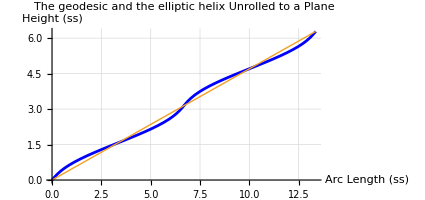

```mathematica
ParametricPlot[{{U[ss],Z[ss]},{sU[ss],ss}},{ss,0,tMax},AspectRatio->Automatic,PlotStyle->{Blue,Thick},PlotLabel->"The geodesic and the elliptic helix \n Unrolled to a Plane",AxesLabel->{"Arc Length (ss)","Height (ss)"},GridLines->Automatic]
```

### 6.1.5. Geodesics equation on a torus

#### Torus Geodesics equation - solving and plotting via Mathematica.The surface normal vector n and the principal normal vector N of the curve are aligned.

```mathematica
Remove["Global`*"]
Rr={R Cos[x[1]]+r Cos[x[2]]Cos[x[1]],R Sin[x[1]]+r Cos[x[2]]Sin[x[1]],r Sin[x[2]]}
R1=D[Rr,x[1]]
R2=D[Rr,x[2]]
GM={{R1.R1,R1.R2},{R2.R1,R2.R2}}//Simplify
SetSystem[x,g,GM]

AbsoluteDerivative[IndexDerivative[x[k],s],m,s,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
IndexDerivativeSimplify[%]/.ρ->n

ExpandDoubleIndex[%,{m,n}]
ExpandIndex[%,{k}]//Simplify
%/.x[1]->u[s]/.x[2]->v[s]
s20=EvaluateIndexDerivative[%]
```

{R Cos[x_^1]+r Cos[x_^1] Cos[x_^2],R Sin[x_^1]+r Cos[x_^2] Sin[x_^1],r Sin[x_^2]}

{-R Sin[x_^1]-r Cos[x_^2] Sin[x_^1],R Cos[x_^1]+r Cos[x_^1] Cos[x_^2],0}

{-r Cos[x_^1] Sin[x_^2],-r Sin[x_^1] Sin[x_^2],r Cos[x_^2]}

{{(R+r Cos[x_^2])^2,0},{0,(r)^2}}

(δ∂_s x_^k)/δs

(∇_m^ ∂_s x_^k) (∂_s x_^m)

(∂_s x_^m) (∂_(x_^m,s) x_^k)+(∂_s x_^m) (∂_s x_^ρ) Γ_(m ρ)^k

∂_(s,s) x_^k+(∂_s x_^m) (∂_s x_^n) Γ_(m n)^k

∂_(s,s) x_^k+(∂_s x_^1)^2 Γ_(1 1)^k+(∂_s x_^1) (∂_s x_^2) Γ_(1 2)^k+(∂_s x_^1) (∂_s x_^2) Γ_(2 1)^k+(∂_s x_^2)^2 Γ_(2 2)^k

{(2 (Cos[x_^2] (∂_(x_^2) r)+∂_(x_^2) R+r (∂_(x_^2) Cos[x_^2])) (∂_s x_^1) (∂_s x_^2))/(R+r Cos[x_^2])-(r (∂_(x_^1) r) (∂_s x_^2)^2)/((R+r Cos[x_^2])^2)+∂_(s,s) x_^1+((∂_s x_^1)^2 (Cos[x_^2] (∂_(x_^1) r)+∂_(x_^1) R-r (∂_(x_^1) x_^2) Sin[x_^2]))/(R+r Cos[x_^2]),(-((R+r Cos[x_^2]) (Cos[x_^2] (∂_(x_^2) r)+∂_(x_^2) R+r (∂_(x_^2) Cos[x_^2])) (∂_s x_^1)^2)+2 r (∂_(x_^1) r) (∂_s x_^1) (∂_s x_^2)+r (∂_(x_^2) r) (∂_s x_^2)^2+(r)^2 (∂_(s,s) x_^2))/(r)^2}

{(2 (Cos[v[s]] (∂_v[s] r)+∂_v[s] R+r (∂_v[s] Cos[v[s]])) (∂_s u[s]) (∂_s v[s]))/(R+r Cos[v[s]])-(r (∂_u[s] r) (∂_s v[s])^2)/(R+r Cos[v[s]])^2+∂_(s,s) u[s]+((∂_s u[s])^2 (Cos[v[s]] (∂_u[s] r)+∂_u[s] R-r (∂_u[s] s) Sin[v[s]] v'[s]))/(R+r Cos[v[s]]),1/(r)^2(-((R+r Cos[v[s]]) (Cos[v[s]] (∂_v[s] r)+∂_v[s] R+r (∂_v[s] Cos[v[s]])) (∂_s u[s])^2)+2 r (∂_u[s] r) (∂_s u[s]) (∂_s v[s])+r (∂_v[s] r) (∂_s v[s])^2+(r)^2 (∂_(s,s) v[s]))}

{-(2 r Sin[v[s]] u'[s] v'[s])/(R+r Cos[v[s]])+u''[s],(r (R+r Cos[v[s]]) Sin[v[s]] (u'[s])^2+(r)^2 v''[s])/(r)^2}

```mathematica
R=3;
r=1;

m=11.5;
s22=s20[[1]]==0
s23=s20[[2]]==0
s29:=NDSolve[{s22,s23,u[0]==0,v[0]==0,u[Pi]== Pi/2,v[Pi]==Pi},{u[s],v[s]},{s,0,2 Pi}]
s30=s29[[1]];
```

-(2 Sin[v[s]] u'[s] v'[s])/(3+Cos[v[s]])+u''[s]==0

(3+Cos[v[s]]) Sin[v[s]] (u'[s])^2+v''[s]==0

```mathematica
Rs=Rr/.{x[1]->u[s],x[2]->v[s]};
Rs1=Rs/.s30;
g1=ParametricPlot3D[Rs1,{s,0,2Pi},PlotStyle->{Thick},PlotRange->All,Boxed->False,AxesLabel->{"x","y","z"},AxesOrigin->{0,0,0},AxesStyle->Black];
g2=Graphics3D[{Red,Ball[{4,0,0},{.2,0,0}],Ball[{-4,0,0},{.2,0,0}]}];
To1=ParametricPlot3D[Rs,{u[s],0,2Pi},{v[s],0, 2Pi},PlotStyle->{Opacity[1],GrayLevel[0.9]},Mesh->10,PlotPoints->60,PerformanceGoal->"Speed"];
R1=D[Rr,x[1]]/.{x[1]->u[s],x[2]->v[s]}/.s30;
R2=D[Rr,x[2]]/.{x[1]->u[s],x[2]->v[s]}/.s30;
R31=Cross[R1,R2]/Norm[Cross[R1,R2]]/.Abs[p_]^2->p^2;
g5=Graphics3D[{Magenta,Thick,Arrow[Table[{Rs1,Rs1+R31},{s,0,2Pi,Pi/7}]]}];
D[Rs1,s]/Norm[D[Rs1,s]]/.Abs[p_]^2->p^2;
rt=D[%,s]/Norm[D[%,s]]/.Abs[p_]^2->p^2;
g6=Graphics3D[{Yellow,Thick,Arrow[Table[{Rs1,Rs1+Sign[rt[[1]]Rs1[[1]]]Sign[rt[[2]]Rs1[[2]]]Sign[rt[[3]]Rs1[[3]]]1.2rt}/.x[1]->s,{s,0, 2Pi,Pi/7}]]}];
Show[g1,To1,g2,g5,g6]
```

-Graphics3D-

## 6.2. General theory of relativity

### 6.2.1. Deriving the Schwarzschild metric. Line elements(("("ds")")^2==-("("dct")")^2+("("dr")")^2+("("dθ")")^2+("("dϕ")")^2==-("("dx[1]")")^2+("("dx[2]")")^2+("("dx[3]")")^2+("("dx[4]")")^2) at Minkowski space.

#### Assuming spherical symmetry,the metric tensor is generally given the flowing. (-("("ⅇ")")^ν[x_(" ")^2] | 0 | 0 | 0 0 | ("("ⅇ")")^λ[x_(" ")^2] | 0 | 0 0 | 0 | ("("x_(" ")^2")")^2 | 0 0 | 0 | 0 | ("("Sin[x_(" ")^3]")")^2 ("("x_(" ")^2")")^2)

```mathematica
Remove["Global`*"]
ds^2==-dct^2+dr^2+dθ^2+dϕ^2==-dx[1]^2+dx[2]^2+dx[3]^2+dx[4]^2
NDim=4;
GMs=DiagonalMatrix[{-(1-a/x[2]),1/(1-a/x[2]),x[2]^2,x[2]^2 Sin[x[3]]^2}];
MatrixForm[%];
GM=DiagonalMatrix[{-Exp[ν[x[2]]],Exp[λ[x[2]]],x[2]^2,x[2]^2 Sin[x[3]]^2}];
MatrixForm[%];
"Assuming spherical symmetry,the metric tensor is generally given by the following formula"
Tensor[g,{i,j},{Void,Void}]==MatrixForm[GM]
SetSystem[x,g,GM]
Christoffel2[g,x][{j,k},{i}];
ExpandIndex[%,{i,j,k}];
EvaluateIndexDerivative[%]//Simplify;
Christoffel2[g,x][{j,k},{i}]==Map[MatrixForm,%]

"Energy-momentum tensor=0.Because the mass is concentrated in the center and there is no mass on the periphery."
Tensor[G,{i,Void},{Void,j}]==8 Pi G/c^4 Tensor[T,{i,Void},{Void,j}]==0
"Einstein Tensor G==0"
s1=Tensor[G,{i,Void},{Void,j}]==RieChrisCur[{Void},{i},{j},g,x]-1/2 Kronecker[i,j]RieChrisCur[{Void},{p},{p},g,x]
```

(ds)^2==-(dct)^2+(dr)^2+(dθ)^2+(dϕ)^2==-(dx[1])^2+(dx[2])^2+(dx[3])^2+(dx[4])^2

Assuming spherical symmetry,the metric tensor is generally given by the following formula

g_ij^==(-(ⅇ)^ν[x_^2] | 0 | 0 | 0
0 | (ⅇ)^λ[x_^2] | 0 | 0
0 | 0 | (x_^2)^2 | 0
0 | 0 | 0 | (Sin[x_^3])^2 (x_^2)^2)

Γ_jk^i=={(0 | 1/2 ν'[x_^2] | 0 | 0
1/2 ν'[x_^2] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 (ⅇ)^(-λ[x_^2]+ν[x_^2]) ν'[x_^2] | 0 | 0 | 0
0 | 1/2 λ'[x_^2] | 0 | 0
0 | 0 | -(ⅇ)^(-λ[x_^2]) x_^2 | 0
0 | 0 | 0 | -(ⅇ)^(-λ[x_^2]) (Sin[x_^3])^2 x_^2),(0 | 0 | 0 | 0
0 | 0 | (x_^2)^-1 | 0
0 | (x_^2)^-1 | 0 | 0
0 | 0 | 0 | -1/2 Sin[2 x_^3]),(0 | 0 | 0 | 0
0 | 0 | 0 | (x_^2)^-1
0 | 0 | 0 | Cot[x_^3]
0 | (x_^2)^-1 | Cot[x_^3] | 0)}

Energy-momentum tensor=0.Because the mass is concentrated in the center and there is no mass on the periphery.

G_i^j==(8 G π T_i^j)/(c)^4==0

Einstein Tensor G==0

G_i^j==RCC_(,i)^j-1/2 δ_i^j RCC_(,p)^p

#### Einstein Tensor : G_(i" ")^(" "j)==0

```mathematica
ExpandRicci[s1[[2]]];
ExpandRCC[%];
ExpandDoubleIndex[%,{ρ,ξ,σ,p}];
ExpandIndex[%,{j,i}];
s5=EvaluateIndexDerivative[%]//Expand;
Tensor[G,{i,Void},{Void,j}]==MatrixForm[%]==0
"From the above formula,find λ[x[2]] and ν[x[2] ,and substitute them into Einstein Tensor:G and Metric Tensor:GM."
r1={λ[x[2]]->-Log[(1-a/x[2])],ν[x[2]]->Log[(1-a/x[2])]};
r2={λ'[x[2]]->-D[Log[(1-a/x[2])],x[2]],ν'[x[2]]->D[Log[(1-a/x[2])],x[2]],ν''[x[2]]->D[Log[(1-a/x[2])],{x[2],2}]};
GM/.r1//Simplify;
Tensor[g,{i,j},{Void,Void}]==MatrixForm[%]
Tensor[G,{i,Void},{Void,j}]==s5/.r1/.r2//Simplify
```

G_i^j==(-1/((x_^2)^2)+((ⅇ)^(-λ[x_^2]))/((x_^2)^2)-((ⅇ)^(-λ[x_^2]) λ'[x_^2])/x_^2 | 0 | 0 | 0
0 | -1/((x_^2)^2)+((ⅇ)^(-λ[x_^2]))/((x_^2)^2)+((ⅇ)^(-λ[x_^2]) ν'[x_^2])/x_^2 | 0 | 0
0 | 0 | -((ⅇ)^(-λ[x_^2]) λ'[x_^2])/(2 x_^2)+((ⅇ)^(-λ[x_^2]) ν'[x_^2])/(2 x_^2)-1/4 (ⅇ)^(-λ[x_^2]) λ'[x_^2] ν'[x_^2]+1/4 (ⅇ)^(-λ[x_^2]) (ν'[x_^2])^2+1/2 (ⅇ)^(-λ[x_^2]) ν''[x_^2] | 0
0 | 0 | 0 | -((ⅇ)^(-λ[x_^2]) λ'[x_^2])/(2 x_^2)+((ⅇ)^(-λ[x_^2]) ν'[x_^2])/(2 x_^2)-1/4 (ⅇ)^(-λ[x_^2]) λ'[x_^2] ν'[x_^2]+1/4 (ⅇ)^(-λ[x_^2]) (ν'[x_^2])^2+1/2 (ⅇ)^(-λ[x_^2]) ν''[x_^2])==0

From the above formula,find λ[x[2]] and ν[x[2] ,and substitute them into Einstein Tensor:G and Metric Tensor:GM.

g_ij^==(-1+a/x_^2 | 0 | 0 | 0
0 | (1-a/x_^2)^-1 | 0 | 0
0 | 0 | (x_^2)^2 | 0
0 | 0 | 0 | (Sin[x_^3])^2 (x_^2)^2)

G_i^j=={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### Solve λ[x[2]] and ν[x[2]] from G_(i" ")^(" "j)==0

```mathematica
"Solve λ[x[2]] and ν[x[2]] from G_i^j==0"
s5[[1,1]]==0
DSolve[%,λ[x[2]],x[2]];
Exp[λ[x[2]]]/.%[[1]];
TrigToExp[%]//Simplify;
s1=Exp[λ[x[2]]]==%/.C[1]->Pi I+Log[a]//Simplify
s5[[2,2]]==0
%/.Exp[-λ[x[2]]]->1/s1[[2]];
DSolve[%,ν[x[2]],x[2]]//Expand;
Exp[ν[x[2]]]==(Exp[ν[x[2]]]/.%[[1]]/.Exp[C[1]]->1)
```

Solve λ[x[2]] and ν[x[2]] from G_i^j==0

-1/((x_^2)^2)+((ⅇ)^(-λ[x_^2]))/((x_^2)^2)-((ⅇ)^(-λ[x_^2]) λ'[x_^2])/x_^2==0

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

(ⅇ)^λ[x_^2]==x_^2/(-a+x_^2)

-1/((x_^2)^2)+((ⅇ)^(-λ[x_^2]))/((x_^2)^2)+((ⅇ)^(-λ[x_^2]) ν'[x_^2])/x_^2==0

(ⅇ)^ν[x_^2]==(-a+x_^2)/x_^2

### 6.2.2. Derive the geodesic equation from the absolute derivative:((δ T_(" ")^i)/δτ=0).

#### Schwarzschild metric : GM

```mathematica
Remove["Global`*"]
dx[p_]:=Tensor[dx,{Void},{p}]
ds^2==(1-a/x[2])dx[1]^2+1/(1-a/x[2])dx[2]^2+x[2]^2dx[3]^2+x[2]^2 Sin[x[3]]^2dx[4]^2
GM=DiagonalMatrix[{-(1-a/x[2]),1/(1-a/x[2]),x[2]^2,x[2]^2 Sin[x[3]]^2}];
"Schwarzschild metric:GM"
⟨Tensor[g,{i,j},{Void,Void}]⟩==MatrixForm[GM]
SetSystem[x,g,GM]
Christoffel2[g,x][{j,k},{i}];
ExpandIndex[%,{i,j,k}];
s1=EvaluateIndexDerivative[%]//Simplify;
⟨Christoffel2[g,x][{j,k},{i}]⟩==Map[MatrixForm,%]
r10=SetTensorRule[ExpandIndex[Tensor[F,{j,k},{i}],{i,j,k}],s1];
```

(ds)^2==((dx_^2)^2)/(1-a/x_^2)+(dx_^1)^2 (1-a/x_^2)+(dx_^3)^2 (x_^2)^2+(Sin[x_^3])^2 (dx_^4)^2 (x_^2)^2

Schwarzschild metric:GM

⟨g_ij^⟩==(-1+a/x_^2 | 0 | 0 | 0
0 | (1-a/x_^2)^-1 | 0 | 0
0 | 0 | (x_^2)^2 | 0
0 | 0 | 0 | (Sin[x_^3])^2 (x_^2)^2)

⟨Γ_jk^i⟩=={(0 | -a/(2 a x_^2-2 (x_^2)^2) | 0 | 0
-a/(2 a x_^2-2 (x_^2)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-(a (a-x_^2))/(2 (x_^2)^3) | 0 | 0 | 0
0 | a/(2 a x_^2-2 (x_^2)^2) | 0 | 0
0 | 0 | a-x_^2 | 0
0 | 0 | 0 | (Sin[x_^3])^2 (a-x_^2)),(0 | 0 | 0 | 0
0 | 0 | (x_^2)^-1 | 0
0 | (x_^2)^-1 | 0 | 0
0 | 0 | 0 | -1/2 Sin[2 x_^3]),(0 | 0 | 0 | 0
0 | 0 | 0 | (x_^2)^-1
0 | 0 | 0 | Cot[x_^3]
0 | (x_^2)^-1 | Cot[x_^3] | 0)}

#### From AbsoluteDerivative:(δ T_(" ")^i)/δτ=0 , we can derive geodesics in Schwarzschild metric space.

```mathematica
AbsoluteDerivative[Tensor[T,{Void},{i}],n,τ,g,x]
ExpandABSDer[%]
ExpandCODer[%]//Expand
%/.Tensor[T,{Void},{i_}]->IndexDerivative[x[i],τ]
IndexDerivativeSimplify[%]
%/. Christoffel2[g,x][{j_,k_},{i_}]->Tensor[F,{j,k},{i}]

s2=ExpandIndex[ExpandDoubleIndex[%,{n,ρ}],{i}]/.r10;
MatrixForm[%]==0
```

(δ T_^i)/δτ

(∇_n^ T_^i) ∂_τ x_^n

∂_(x_^n) T_^i ∂_τ x_^n+∂_τ x_^n T_^ρ Γ_nρ^i

∂_τ x_^n ∂_(τ,x_^n) x_^i+∂_τ x_^n ∂_τ x_^ρ Γ_nρ^i

∂_(τ,τ) x_^i+∂_τ x_^n ∂_τ x_^ρ Γ_nρ^i

∂_(τ,τ) x_^i+∂_τ x_^n ∂_τ x_^ρ F_nρ^i

(∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2)
∂_(τ,τ) x_^2+(∂_τ x_^3)^2 (a-x_^2)+(∂_τ x_^4)^2 (Sin[x_^3])^2 (a-x_^2)-(a (∂_τ x_^1)^2 (a-x_^2))/(2 (x_^2)^3)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)
∂_(τ,τ) x_^3-1/2 (∂_τ x_^4)^2 Sin[2 x_^3]+(2 ∂_τ x_^2 ∂_τ x_^3)/x_^2
2 Cot[x_^3] ∂_τ x_^3 ∂_τ x_^4+∂_(τ,τ) x_^4+(2 ∂_τ x_^2 ∂_τ x_^4)/x_^2)==0

#### The equation we are looking for is called the law of conservation of areas with respect to τ (law of conservation of angular momentum). “h” is the angular velocity.

```mathematica
s2[[1]]==0
Integrate[%[[1]],τ]==K
(1-a /x[2])IndexDerivative[x[1],τ]==c K
s3=Solve[%,IndexDerivative[x[1],τ]]
s2[[4]]==0
x[2]^2 Sin[x[3]]^2 %[[1]]//Expand
Integrate[%,τ]==h
"the law of conservation of areas with respect to τ (law of conservation of angular momentum). h is the angular velocity"
x[2]^2Sin[x[3]]^2IndexDerivative[x[4],τ]==h
%/.x[3]->Pi/2
s4=Solve[%,IndexDerivative[x[4],τ]]
```

∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2)==0

∫(∂_(τ,τ) x_^1-(2 a ∂_τ x_^1 ∂_τ x_^2)/(2 a x_^2-2 (x_^2)^2))ⅆτ==K

∂_τ x_^1 (1-a/x_^2)==c K

{{∂_τ x_^1→(c K x_^2)/(-a+x_^2)}}

2 Cot[x_^3] ∂_τ x_^3 ∂_τ x_^4+∂_(τ,τ) x_^4+(2 ∂_τ x_^2 ∂_τ x_^4)/x_^2==0

2 ∂_τ x_^2 ∂_τ x_^4 (Sin[x_^3])^2 x_^2+2 Cos[x_^3] ∂_τ x_^3 ∂_τ x_^4 Sin[x_^3] (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2

∫(2 ∂_τ x_^2 ∂_τ x_^4 (Sin[x_^3])^2 x_^2+2 Cos[x_^3] ∂_τ x_^3 ∂_τ x_^4 Sin[x_^3] (x_^2)^2+∂_(τ,τ) x_^4 (Sin[x_^3])^2 (x_^2)^2)ⅆτ==h

the law of conservation of areas with respect to τ (law of conservation of angular momentum). h is the angular velocity

∂_τ x_^4 (Sin[x_^3])^2 (x_^2)^2==h

∂_τ x_^4 (x_^2)^2==h

{{∂_τ x_^4→h/((x_^2)^2)}}

```mathematica
s21=(s2[[2]]/.x[3]->Pi/2)==0
s21/.s3[[1]]/.s4[[1]]//Expand
%[[1,1]]+Factor[%[[1,2;;3]]]+Factor[%[[1,4;;5]]]+%[[1,6]]==0
```

∂_(τ,τ) x_^2+(∂_τ x_^4)^2 (a-x_^2)-(a (∂_τ x_^1)^2 (a-x_^2))/(2 (x_^2)^3)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)==0

∂_(τ,τ) x_^2+(a (h)^2)/((x_^2)^4)-(h)^2/((x_^2)^3)+(a (c)^2 (K)^2)/(2 (-a+x_^2)^2)-((a)^2 (c)^2 (K)^2)/(2 x_^2 (-a+x_^2)^2)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)==0

∂_(τ,τ) x_^2+((h)^2 (a-x_^2))/((x_^2)^4)-(a (c)^2 (K)^2)/(2 (a-x_^2) x_^2)+(a (∂_τ x_^2)^2)/(2 a x_^2-2 (x_^2)^2)==0

#### It is possible to solve this directly, but it is better to start with the following equation, which divides both sides of the equation for the line element of metric dcτ^2 by dτ^2, and thus eliminates one integration . Note that the various conditions obtained so far have been substituted in .

```mathematica
(dcτ)^2==-(ds)^2==-Tensor[g,{i,j},{Void,Void}]dx[i]dx[j]
(dcτ)^2==(1-a/x[2])dx[1]^2-(1/(1-a/x[2])dx[2]^2+x[2]^2dx[3]^2+x[2]^2 Sin[x[3]]^2dx[4]^2)
%[[1]]/(dτ)^2==Expand[%[[2]]/(dτ)^2];
c^2==%[[2]]/.dx[i_]^2/dτ^2->IndexDerivative[x[i],τ]^2//Simplify;
%/.x[3]->Pi/2/.s3[[1]]/.s4[[1]]//Simplify//Expand
Solve[%,IndexDerivative[x[2],τ]]//Expand
IndexDerivative[x[2],τ]^2==(IndexDerivative[x[2],τ]^2/.%[[1]]//Expand//Simplify)
s4=1/2%[[1,1]]-(%[[2,2;;4]]/2//Expand)==%[[2,1]]/2
"If we denote the first term by T, the second to fourth terms by effective potential:V[x[2]], and the right-hand side by E, this has the form of the law of conservation of energy in classical mechanics, T + V = E. Note that the fourth term of V(r), −a c^2/(2x[2]), is the term for the gravitational field −GM/r."
```

(dcτ)^2==-(ds)^2==-dx_^i dx_^j g_ij^

(dcτ)^2==-((dx_^2)^2)/(1-a/x_^2)+(dx_^1)^2 (1-a/x_^2)-(dx_^3)^2 (x_^2)^2-(Sin[x_^3])^2 (dx_^4)^2 (x_^2)^2

(c)^2==-(a (h)^2)/((a-x_^2) (x_^2)^2)+(h)^2/((a-x_^2) x_^2)-((c)^2 (K)^2 x_^2)/(a-x_^2)+((∂_τ x_^2)^2 x_^2)/(a-x_^2)

{{∂_τ x_^2→-((a (h)^2-(h)^2 x_^2+a (c)^2 (x_^2)^2-(c)^2 (x_^2)^3+(c)^2 (K)^2 (x_^2)^3)^(1/2))/((x_^2)^(3/2))},{∂_τ x_^2→((a (h)^2-(h)^2 x_^2+a (c)^2 (x_^2)^2-(c)^2 (x_^2)^3+(c)^2 (K)^2 (x_^2)^3)^(1/2))/((x_^2)^(3/2))}}

(∂_τ x_^2)^2==(c)^2 (-1+(K)^2)+(a (h)^2)/((x_^2)^3)-(h)^2/((x_^2)^2)+(a (c)^2)/x_^2

(∂_τ x_^2)/2-(a (h)^2)/(2 (x_^2)^3)+(h)^2/(2 (x_^2)^2)-(a (c)^2)/(2 x_^2)==1/2 (c)^2 (-1+(K)^2)

If we denote the first term by T, the second to fourth terms by effective potential:V[x[2]], and the right-hand side by E, this has the form of the law of conservation of energy in classical mechanics, T + V = E. Note that the fourth term of V(r), −a c^2/(2x[2]), is the term for the gravitational field −GM/r.

#### Effective potential of general relativity : V[x_(" ")^2]

```mathematica
"Effective potential:V[x_^2]==effect of general relativity+centrifugal potential+Newtonian potential"
V[x[2]]==s4[[1,2;;4]]/c^2//Expand
r==x[2]/a
L==h/(a c)
Evaluate[%%%[[2]]/.x[2]->r a/.h->L a c];
Vv[r_]=%
"Vr[r]:Effective potential of general relativity by r=x[2]/a"
"Vr[r]"==Vv[r]
D[%[[2]],r]==0
s5=Solve[%,r]
"Calculate the positions of the maximum and minimum points."
```

Effective potential:V[x_^2]==effect of general relativity+centrifugal potential+Newtonian potential

V[x_^2]==-(a (h)^2)/(2 (c)^2 (x_^2)^3)+(h)^2/(2 (c)^2 (x_^2)^2)-a/(2 x_^2)

r==x_^2/a

L==h/(a c)

-(L)^2/(2 (r)^3)+(L)^2/(2 (r)^2)-1/(2 r)

Vr[r]:Effective potential of general relativity by r=x[2]/a

Vr[r]==-(L)^2/(2 (r)^3)+(L)^2/(2 (r)^2)-1/(2 r)

(3 (L)^2)/(2 (r)^4)-(L)^2/(r)^3+1/(2 (r)^2)==0

{{r→(L)^2-(-3 (L)^2+(L)^4)^(1/2)},{r→(L)^2+(-3 (L)^2+(L)^4)^(1/2)}}

Calculate the positions of the maximum and minimum points.

```mathematica
s5[[1,1,2,2,2,1]]==0
Solve[%,L]
"In case L<Sqrt[3],Vr[r] has no extreme values."
Vn[r_]:=Vv[r]/.Vv[r][[1]]->0;
"Vn[r]:Effective potential of Newtonian mechanics"
"Vn[r]"==Vn[r]
```

-3 (L)^2+(L)^4==0

{{L→0},{L→0},{L→-(3)^(1/2)},{L→(3)^(1/2)}}

In case L<Sqrt[3],Vr[r] has no extreme values.

Vn[r]:Effective potential of Newtonian mechanics

Vn[r]==(L)^2/(2 (r)^2)-1/(2 r)

### 6.2.3. Available energy of motion in Schwarzschild space: V(r) Schwarzschild radius:a=2 G M/c^2 Area Velocity:h Constant of gravitation:G Mass of the object:M Speed of light:c =299792458 m/s r=x[2]/a L=h/(a c)

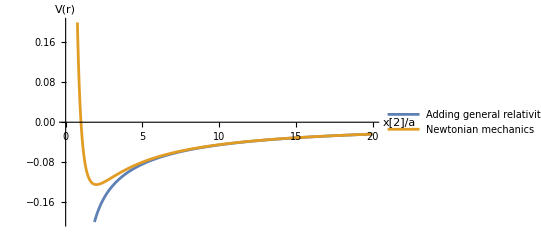
-Graphics-V[r]:Effective potential L=1

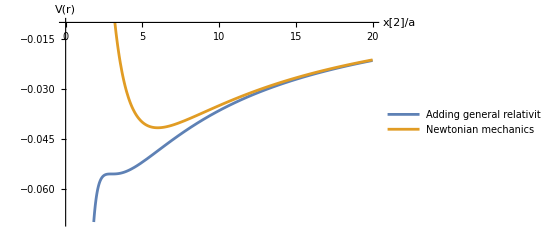
-Graphics-V[r]:Effective potential L=Sqrt[3]

2.12132

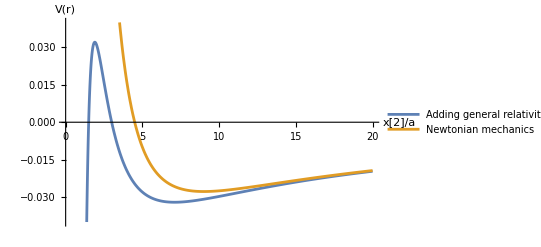
-Graphics-V[r]:Effective potential L=Sqrt[4.5]

2.5

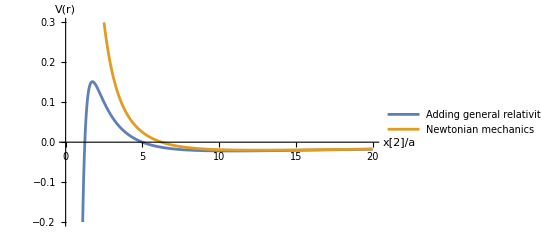
-Graphics-V[r]:Effective potential L=2.5

```mathematica
Remove["Global`*"]
Vr[r_]:=-L^2/(2 r^3)+L^2/(2 r^2)-1/(2 r)
Vn[r_]:=L^2/(2 r^2)-1/(2 r)
L=1;
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.2,0.2}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=1",Top]
L=Sqrt[3];
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.07,-0.01}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=Sqrt[3]",Top]
L=Sqrt[4.5]
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.04,0.04}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=Sqrt[4.5]",Top]
L=2.5
g1=Plot[{Vr[r],Vn[r]},{r,0,20},PlotRange->{{0,20},{-.2,0.3}},PlotLegends->LineLegend[{"Adding general relativity","Newtonian mechanics"}],AxesLabel->{"x[2]/a",V[r]}];
Labeled[g1,"V[r]:Effective potential L=2.5",Top]
```

### 6.2.4. Orbits of planets with the position of the sun as the focus.

#### Planetary motion in classical mechanics ϵ:Orbital eccentricity ϕ0:Initial Phase

```mathematica
Remove["Global`*"]
Manipulate[
s1=PolarPlot[{1/(1+ϵ Cos[ϕ-ϕ0])},{ϕ,0,2Pi},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Red]];
s2=Plot[{Tan[ϕ0]x },{x,-6.2,6.2},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Green]];
R1=(-1/(1-ϵ )+1/(1+ϵ ))/2;
s3=Plot[{-1/Tan[ϕ0](x-R1 Cos[ϕ0])+R1  Sin[ϕ0] },{x,-6.2,6.2},PlotRange->{{-6.2,6.2},{-6.2,6.2}},ColorFunction->Function[{x,y},Blue]];
Show[s1,s2,s3]
,{ϵ,0,1-0.001},{ϕ0,-Pi+0.0001,Pi}
]
```

#### Planetary motion in general relativity. ϵ=0.75:Orbital eccentricity Pp=3 a /l l=2 a (h/(a c)^2 Schwarzschild radius:a=2 G M/c^2 Area Velocity:h

```mathematica
Manipulate[
s1=PolarPlot[{1/(1+0.75 Cos[Sqrt[(1-Pp)] (ϕ-ϕ0)])},{ϕ,0,20Pi},PlotRange->{{-4.2,4.2},{-4.2,4.2}},ColorFunction->Function[{x,y,ϕ},Hue[ϕ]]];

Show[s1]
,{ϕ0,-Pi,Pi},{Pp,0 ,.1}
]
```

#### Geodesics of light in a gravitational field.

```mathematica
Remove["Global`*"]
Manipulate[
s1=PolarPlot[{r/(Abs[Cos[ϕ]]+3/(4 r)-1/(4r) Cos[2 ϕ] ),1},{ϕ,-Pi,Pi },PlotRange->{{-5,5},{-5,5}}];
Show[s1],{r,1.4,5}
]
```

## 6.3. Electromagnetic Relativity

### 6.3.1. Quaternion of the electromagnetic field.

#### The Lorentz force acting on a moving charged particle is given by the following equation: F = Q (E + v×B)

```mathematica
Remove["Global`*"]
F̲={Fx,Fy,Fz}
Ε={Ex,Ey,Ez}
v̲={vx,vy,vz}
B={Bx,By,Bz}
F̲==Q(Ε+Cross[v̲,B])
"F:Four-force"
F==UnderBar[γv] F̲
"v:Four-velocity"
v==UnderBar[γv] {-c ,UnderBar[vx],UnderBar[vy],UnderBar[vz]}
```

{Fx,Fy,Fz}

{Ex,Ey,Ez}

{vx,vy,vz}

{Bx,By,Bz}

{Fx,Fy,Fz}=={Q (Ex+Bz vy-By vz),Q (Ey-Bz vx+Bx vz),Q (Ez+By vx-Bx vy)}

F:Four-force

F=={Fx UnderBar[γv],Fy UnderBar[γv],Fz UnderBar[γv]}

v:Four-velocity

v=={-c UnderBar[γv],UnderBar[vx] UnderBar[γv],UnderBar[vy] UnderBar[γv],UnderBar[vz] UnderBar[γv]}

#### Electromagnetic field tensor:F_(n" ")^(" "m)

```mathematica
Remove["Global`*"]
Tensor[f,{Void},{m}]==Q Tensor[F,{n,Void},{Void,m}]Tensor[v,{Void},{n}]
Ff={f0,fx,fy,fz};
Vv={c ,vx,vy,vz};
Vm={-c ,vx,vy,vz};
"電磁テンソル"
s1={{0,Ex/c,Ey/c,Ez/c},{Ex/c,0,Bz,-By},{Ey/c,-Bz,0,Bx},{Ez/c,By,-Bx,0}};
⟨Tensor[F,{n,Void},{Void,m}]⟩==MatrixForm[s1]
Print[⟨Tensor[f,{Void},{m}]⟩,"==",MatrixForm[Q s1.Vv]]
s2=Q s1.Vv;
Tensor[g,{n,m},{Void,Void}]Tensor[v,{Void},{n}]Tensor[F,{Void},{m}]==Tensor[v,{m},{Void}]Tensor[f,{Void},{m}]==0
s2.Vm//Simplify
```

f_^m==Q F_n^m v_^n

電磁テンソル

⟨F_n^m⟩==(0 | Ex/c | Ey/c | Ez/c
Ex/c | 0 | Bz | -By
Ey/c | -Bz | 0 | Bx
Ez/c | By | -Bx | 0)

⟨f_^m⟩==(Q ((Ex vx)/c+(Ey vy)/c+(Ez vz)/c)
Q (Ex+Bz vy-By vz)
Q (Ey-Bz vx+Bx vz)
Q (Ez+By vx-Bx vy))

F_^m g_nm^ v_^n==f_^m v_m^==0

0

```mathematica
⟨Tensor[g,{Void,Void},{n,k}]⟩==⟨Tensor[g,{m,k},{Void,Void}]⟩==MatrixForm[DiagonalMatrix[{-1,1,1,1}]]
GM=DiagonalMatrix[{-1,1,1,1}];
"共変テンソル"
⟨Tensor[F,{m,n},{Void,Void}]⟩==⟨Tensor[g,{m,k},{Void,Void}]⟩.⟨Tensor[F,{n,Void},{Void,k}]⟩
⟨Tensor[F,{m,n},{Void,Void}]⟩==MatrixForm[GM.s1]
"反変テンソル"
⟨Tensor[F,{Void,Void},{m,n}]⟩==⟨Tensor[B,{k,Void},{Void,m}]⟩.⟨Tensor[g,{Void,Void},{n,k}]⟩
⟨Tensor[F,{Void,Void},{m,n}]⟩==MatrixForm[s1.GM]
```

⟨g_^nk⟩==⟨g_mk^⟩==(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

共変テンソル

⟨F_mn^⟩==⟨g_mk^⟩.⟨F_n^k⟩

⟨F_mn^⟩==(0 | -Ex/c | -Ey/c | -Ez/c
Ex/c | 0 | Bz | -By
Ey/c | -Bz | 0 | Bx
Ez/c | By | -Bx | 0)

反変テンソル

⟨F_^mn⟩==⟨B_k^m⟩.⟨g_^nk⟩

⟨F_^mn⟩==(0 | Ex/c | Ey/c | Ez/c
-Ex/c | 0 | Bz | -By
-Ey/c | -Bz | 0 | Bx
-Ez/c | By | -Bx | 0)

#### Faraday’s two-form (F̃)_ij^(" "" ")==1/2 F_(" "" ")^kl ϵ_ijkl^(" ")

```mathematica
Remove["Global`*"]
GM=DiagonalMatrix[{1,-1,-1,-1}];
SetSystem[x,g,GM]

s1={{0,Ex/c,Ey/c,Ez/c},{-Ex/c,0,Bz,-By},{-Ey/c,-Bz,0,Bx},{-Ez/c,By,-Bx,0}};
r1=SetTensorRule[ExpandIndex[Tensor[F,{Void,Void},{m,n}],{m,n}],s1]
⟨Tensor[F,{Void,Void},{m,n}]⟩==MatrixForm[s1]
Tensor[F̃,{i,j},{Void,Void}]==1/2Tensor[F,{Void,Void},{k,l}]Tensor[ϵ,{k,l,i,j},{Void}]
s2=ExpandIndex[ExpandDoubleIndex[%[[2]],{k,l}],{i,j}]/.r1
Tensor[F̃,{i,j},{Void,Void}]==MatrixForm[s2]
Tensor[F̃,{Void,Void},{i,j}]==MatrixForm[GM.s2.GM]
```

{F_^11→0,F_^12→Ex/c,F_^13→Ey/c,F_^14→Ez/c,F_^21→-Ex/c,F_^22→0,F_^23→Bz,F_^24→-By,F_^31→-Ey/c,F_^32→-Bz,F_^33→0,F_^34→Bx,F_^41→-Ez/c,F_^42→By,F_^43→-Bx,F_^44→0}

⟨F_^mn⟩==(0 | Ex/c | Ey/c | Ez/c
-Ex/c | 0 | Bz | -By
-Ey/c | -Bz | 0 | Bx
-Ez/c | By | -Bx | 0)

(F̃)_ij^==1/2 F_^kl ϵ_klij^

{{0,Bx,By,Bz},{-Bx,0,Ez/c,-Ey/c},{-By,-Ez/c,0,Ex/c},{-Bz,Ey/c,-Ex/c,0}}

(F̃)_ij^==(0 | Bx | By | Bz
-Bx | 0 | Ez/c | -Ey/c
-By | -Ez/c | 0 | Ex/c
-Bz | Ey/c | -Ex/c | 0)

(F̃)_^ij==(0 | -Bx | -By | -Bz
Bx | 0 | Ez/c | -Ey/c
By | -Ez/c | 0 | Ex/c
Bz | Ey/c | -Ex/c | 0)

(F̃)_^ij==(0 | -Bx | -By | -Bz
Bx | 0 | Ez/c | -Ey/c
By | -Ez/c | 0 | Ex/c
Bz | Ey/c | -Ex/c | 0)

#### Using the following equation to derive Electromagnetic field tensor: F_mn^(" "" ")==-∂_(x_(" ")^n) A_m^(" ")+∂_(x_(" ")^m) A_n^(" ") Maxwell’s equation: (1) ∇.B=0, (2) ∇×E=-∂B/∂t, (3) ϵ0∇.E=ρ, (4) 1/μ0∇×B-ϵ0∂E/∂t=j Four-dimensional vector potential:(5)A_1=-ϕ/c, (6)E=-∇ϕ-∂A/∂t, (7)B=∇×A

```mathematica
Remove["Global`*"]
NDim=4;
Tensor[F,{Void,Void},{m,n}]==Tensor["∂",{Void},{m}]Tensor[A,{Void},{n}]-Tensor["∂",{Void},{n}]Tensor[A,{Void},{m}]==
Tensor[g,{Void,Void},{m,i}]IndexDerivative[Tensor[A,{n},{Void}],x[i]]-Tensor[g,{Void,Void},{n,j}]IndexDerivative[Tensor[A,{m},{Void}],x[j]]

s1=Tensor[F,{m,n},{Void,Void}]==IndexDerivative[Tensor[A,{n},{Void}],x[m]]-IndexDerivative[Tensor[A,{m},{Void}],x[n]]
s2=ExpandIndex[s1[[2]],{m,n}];
⟨Tensor[F,{m,n},{Void,Void}]⟩==MatrixForm[s2]
```

F_^mn==-∂_^n A_^m+∂_^m A_^n==(∂_(x_^i) A_n^) g_^mi-(∂_(x_^j) A_m^) g_^nj

F_mn^==-(∂_(x_^n) A_m^)+∂_(x_^m) A_n^

⟨F_mn^⟩==(0 | -(∂_(x_^2) A_1^)+∂_(x_^1) A_2^ | -(∂_(x_^3) A_1^)+∂_(x_^1) A_3^ | -(∂_(x_^4) A_1^)+∂_(x_^1) A_4^
∂_(x_^2) A_1^-∂_(x_^1) A_2^ | 0 | -(∂_(x_^3) A_2^)+∂_(x_^2) A_3^ | -(∂_(x_^4) A_2^)+∂_(x_^2) A_4^
∂_(x_^3) A_1^-∂_(x_^1) A_3^ | ∂_(x_^3) A_2^-∂_(x_^2) A_3^ | 0 | -(∂_(x_^4) A_3^)+∂_(x_^3) A_4^
∂_(x_^4) A_1^-∂_(x_^1) A_4^ | ∂_(x_^4) A_2^-∂_(x_^2) A_4^ | ∂_(x_^4) A_3^-∂_(x_^3) A_4^ | 0)

```mathematica
"(7)B=∇×A"
Tensor[ϵ,{m,n,k},{Void,Void}]IndexDerivative[Tensor[A,{n},{Void}],x[m]]
s3=Table[Sum[%,{m,2,4},{n,2,4}],{k,2,4}];
s4=Table[Tensor[B,{n},{Void}],{n,2,4}];
r1=SetTensorRule[s3,s4]
r2=SetTensorRule[-s3,-s4];
s5=s2/.r1/.r2
⟨Tensor[F,{m,n},{Void,Void}]⟩==MatrixForm[s5]
```

(7)B=∇×A

(∂_(x_^m) A_n^) ϵ_mnk^

{-(∂_(x_^4) A_3^)+∂_(x_^3) A_4^→B_2^,∂_(x_^4) A_2^-∂_(x_^2) A_4^→B_3^,-(∂_(x_^3) A_2^)+∂_(x_^2) A_3^→B_4^}

{{0,-(∂_(x_^2) A_1^)+∂_(x_^1) A_2^,-(∂_(x_^3) A_1^)+∂_(x_^1) A_3^,-(∂_(x_^4) A_1^)+∂_(x_^1) A_4^},{∂_(x_^2) A_1^-∂_(x_^1) A_2^,0,B_4^,-B_3^},{∂_(x_^3) A_1^-∂_(x_^1) A_3^,-B_4^,0,B_2^},{∂_(x_^4) A_1^-∂_(x_^1) A_4^,B_3^,-B_2^,0}}

⟨F_mn^⟩==(0 | -(∂_(x_^2) A_1^)+∂_(x_^1) A_2^ | -(∂_(x_^3) A_1^)+∂_(x_^1) A_3^ | -(∂_(x_^4) A_1^)+∂_(x_^1) A_4^
∂_(x_^2) A_1^-∂_(x_^1) A_2^ | 0 | B_4^ | -B_3^
∂_(x_^3) A_1^-∂_(x_^1) A_3^ | -B_4^ | 0 | B_2^
∂_(x_^4) A_1^-∂_(x_^1) A_4^ | B_3^ | -B_2^ | 0)

```mathematica
"(6)E/c=-∇ϕ/c-∂A/∂x[1], (5)A_1=-ϕ/c"
s5/.Tensor[A,{1},{Void}]->-ϕ/c
%/.IndexDerivative[1/c,x[i_]]->0;
%/.IndexDerivative[ϕ,x[i_]]/c+IndexDerivative[Tensor[A,{i_},{Void}],x[1]]->-Tensor["E",{i},{Void}]/c;
s6=%/.-IndexDerivative[ϕ,x[i_]]/c-IndexDerivative[Tensor[A,{i_},{Void}],x[1]]->Tensor["E",{i},{Void}]/c;
s6=s6/.IndexDerivative[c,x[p_]]->0
⟨Tensor[F,{m,n},{Void,Void}]⟩==MatrixForm[s6]
GM=DiagonalMatrix[{-1,1,1,1}];
s7=GM.s6.GM;
⟨Tensor[F,{Void,Void},{m,n}]⟩==MatrixForm[s7]
r3=SetTensorRule[ExpandIndex[Tensor[F,{Void,Void},{m,n}],{m,n}],s7];
```

(6)E/c=-∇ϕ/c-∂A/∂x[1], (5)A_1=-ϕ/c

{{0,-(ϕ (∂_(x_^2) c))/(c)^2+(∂_(x_^2) ϕ)/c+∂_(x_^1) A_2^,-(ϕ (∂_(x_^3) c))/(c)^2+(∂_(x_^3) ϕ)/c+∂_(x_^1) A_3^,-(ϕ (∂_(x_^4) c))/(c)^2+(∂_(x_^4) ϕ)/c+∂_(x_^1) A_4^},{(ϕ (∂_(x_^2) c))/(c)^2-(∂_(x_^2) ϕ)/c-∂_(x_^1) A_2^,0,B_4^,-B_3^},{(ϕ (∂_(x_^3) c))/(c)^2-(∂_(x_^3) ϕ)/c-∂_(x_^1) A_3^,-B_4^,0,B_2^},{(ϕ (∂_(x_^4) c))/(c)^2-(∂_(x_^4) ϕ)/c-∂_(x_^1) A_4^,B_3^,-B_2^,0}}

{{0,-E_2^/c,-E_3^/c,-E_4^/c},{E_2^/c,0,B_4^,-B_3^},{E_3^/c,-B_4^,0,B_2^},{E_4^/c,B_3^,-B_2^,0}}

⟨F_mn^⟩==(0 | -E_2^/c | -E_3^/c | -E_4^/c
E_2^/c | 0 | B_4^ | -B_3^
E_3^/c | -B_4^ | 0 | B_2^
E_4^/c | B_3^ | -B_2^ | 0)

⟨F_^mn⟩==(0 | E_2^/c | E_3^/c | E_4^/c
-E_2^/c | 0 | B_4^ | -B_3^
-E_3^/c | -B_4^ | 0 | B_2^
-E_4^/c | B_3^ | -B_2^ | 0)

#### Derive the four-dimensional current density:⟨j_(" ")^m⟩=={c ρ,j} from ∂_(x_(" ")^n) F_(" "" ")^mn==μ0 J_(" ")^m Maxwell’s equation: (1) ∇.B=0, (2) ∇×E=-∂B/∂t, (3) ϵ0∇.E=ρ, (4) 1/μ0∇×B-ϵ0∂E/∂t=j Four-dimensional vector potential:(5)A_(" ")^m={ϕ/c,A}, (6)E=-∇ϕ-∂A/∂t, (7)B=∇×A

```mathematica
Remove["Global`*"]
⟨Tensor[j,{Void},{m}]⟩=={c ρ,j}
r3=SetTensorRule[ExpandIndex[Tensor[F,{Void,Void},{m,n}],{m,n}],{{0,Tensor["E",{2},{Void}]/c,Tensor["E",{3},{Void}]/c,Tensor["E",{4},{Void}]/c},
{-Tensor["E",{2},{Void}]/c,0,Tensor[B,{4},{Void}],-Tensor[B,{3},{Void}]},
{-Tensor["E",{3},{Void}]/c,-Tensor[B,{4},{Void}],0,Tensor[B,{2},{Void}]},
{-Tensor["E",{4},{Void}]/c,Tensor[B,{3},{Void}],-Tensor[B,{2},{Void}],0}}];
⟨Tensor[F,{Void,Void},{m,n}]⟩==MatrixForm[ExpandIndex[Tensor[F,{Void,Void},{m,n}],{m,n}]/.r3]
s21=IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]==μ0 Tensor[J,{Void},{m}]
s17=ExpandIndex[ExpandDoubleIndex[IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]],{n}],{m}];
⟨IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]⟩==MatrixForm[s17]
s18=s17/.r3/.IndexDerivative[1/c,x[1_]]->0;
⟨IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]⟩==MatrixForm[s18]
s19=s18/.IndexDerivative[w_,x[1]]->IndexDerivative[w,t]/c;
⟨IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]⟩==MatrixForm[s19]
```

⟨j_^m⟩=={c ρ,j}

⟨F_^mn⟩==(0 | E_2^/c | E_3^/c | E_4^/c
-E_2^/c | 0 | B_4^ | -B_3^
-E_3^/c | -B_4^ | 0 | B_2^
-E_4^/c | B_3^ | -B_2^ | 0)

∂_(x_^n) F_^mn==μ0 J_^m

⟨∂_(x_^n) F_^mn⟩==(∂_(x_^1) F_^11+∂_(x_^2) F_^12+∂_(x_^3) F_^13+∂_(x_^4) F_^14
∂_(x_^1) F_^21+∂_(x_^2) F_^22+∂_(x_^3) F_^23+∂_(x_^4) F_^24
∂_(x_^1) F_^31+∂_(x_^2) F_^32+∂_(x_^3) F_^33+∂_(x_^4) F_^34
∂_(x_^1) F_^41+∂_(x_^2) F_^42+∂_(x_^3) F_^43+∂_(x_^4) F_^44)

⟨∂_(x_^n) F_^mn⟩==((∂_(x_^2) E_2^)/c+(∂_(x_^3) E_3^)/c+(∂_(x_^4) E_4^)/c
-(∂_(x_^1) E_2^)/c-∂_(x_^4) B_3^+∂_(x_^3) B_4^+((∂_(x_^1) c) E_2^)/(c)^2
-(∂_(x_^1) E_3^)/c+∂_(x_^4) B_2^-∂_(x_^2) B_4^+((∂_(x_^1) c) E_3^)/(c)^2
-(∂_(x_^1) E_4^)/c-∂_(x_^3) B_2^+∂_(x_^2) B_3^+((∂_(x_^1) c) E_4^)/(c)^2)

⟨∂_(x_^n) F_^mn⟩==((∂_(x_^2) E_2^)/c+(∂_(x_^3) E_3^)/c+(∂_(x_^4) E_4^)/c
-(∂_t E_2^)/(c)^2-∂_(x_^4) B_3^+∂_(x_^3) B_4^+((∂_t c) E_2^)/(c)^3
-(∂_t E_3^)/(c)^2+∂_(x_^4) B_2^-∂_(x_^2) B_4^+((∂_t c) E_3^)/(c)^3
-(∂_t E_4^)/(c)^2-∂_(x_^3) B_2^+∂_(x_^2) B_3^+((∂_t c) E_4^)/(c)^3)

```mathematica
"(4)1/μ0∇×B-ϵ0∂E/∂t=j"
Tensor[j,{Void},{m}]==Tensor[ϵ,{Void,Void,Void},{i,j,m}]IndexDerivative[Tensor[B,{j},{Void}],x[i]]1/μ0-ϵ0 IndexDerivative[Tensor["E",{m},{Void}],t]
%[[2,1]]+Sum[%[[2,2]],{i,2,4},{j,2,4}];
s8=Table[%,{m,2,4}];
Table[ Tensor[j,{Void},{m}],{m,2,4}]== MatrixForm[s8]
s9=Expand[μ0 s8]/.ϵ0 μ0->1/ c^2;
sj3=Table[ μ0 Tensor[j,{Void},{m}],{m,2,4}];
sj3== MatrixForm[s9]
```

(4)1/μ0∇×B-ϵ0∂E/∂t=j

j_^m==-ϵ0 (∂_t E_m^)+((∂_(x_^i) B_j^) ϵ_^ijm)/μ0

{j_^2,j_^3,j_^4}==(-ϵ0 (∂_t E_2^)-(∂_(x_^4) B_3^)/μ0+(∂_(x_^3) B_4^)/μ0
-ϵ0 (∂_t E_3^)+(∂_(x_^4) B_2^)/μ0-(∂_(x_^2) B_4^)/μ0
-ϵ0 (∂_t E_4^)-(∂_(x_^3) B_2^)/μ0+(∂_(x_^2) B_3^)/μ0)

{μ0 j_^2,μ0 j_^3,μ0 j_^4}==(-(∂_t E_2^)/(c)^2-∂_(x_^4) B_3^+∂_(x_^3) B_4^
-(∂_t E_3^)/(c)^2+∂_(x_^4) B_2^-∂_(x_^2) B_4^
-(∂_t E_4^)/(c)^2-∂_(x_^3) B_2^+∂_(x_^2) B_3^)

```mathematica
"(3)Sinse ϵ0 ∇.E=ρ,　c==1/Sqrt[ϵ0μ0], j_^1=c ρ"
s12=1/c  Sum[IndexDerivative[Tensor["E",{m},{Void}],x[m]],{m,2,4}]== 1/(c ϵ0) ρ==1c μ0 ρ
sj1=μ0 Tensor[j,{Void},{1}]==Expand[s12[[1]]]
s14=Prepend[sj3,sj1[[1]]];
s15=Prepend[s9,Expand[s12[[1]]]];
```

(3)Sinse ϵ0 ∇.E=ρ,　c==1/Sqrt[ϵ0μ0], j_^1=c ρ

(∂_(x_^2) E_2^+∂_(x_^3) E_3^+∂_(x_^4) E_4^)/c==ρ/(c ϵ0)==c μ0 ρ

μ0 j_^1==(∂_(x_^2) E_2^)/c+(∂_(x_^3) E_3^)/c+(∂_(x_^4) E_4^)/c

```mathematica
r4=SetTensorRule[s15,s14]
⟨IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]⟩==s9/.r4
ExpandIndex[Tensor[j,{Void},{i}],{i}]=={c ρ,jx,jy,jz}
```

{(∂_(x_^2) E_2^)/c+(∂_(x_^3) E_3^)/c+(∂_(x_^4) E_4^)/c→μ0 j_^1,-(∂_t E_2^)/(c)^2-∂_(x_^4) B_3^+∂_(x_^3) B_4^→μ0 j_^2,-(∂_t E_3^)/(c)^2+∂_(x_^4) B_2^-∂_(x_^2) B_4^→μ0 j_^3,-(∂_t E_4^)/(c)^2-∂_(x_^3) B_2^+∂_(x_^2) B_3^→μ0 j_^4}

⟨∂_(x_^n) F_^mn⟩=={μ0 j_^2,μ0 j_^3,μ0 j_^4}

{j_^1,j_^2,j_^3,j_^4}=={c ρ,jx,jy,jz}

#### Lorentz condition:∂_(x_(" ")^n) A_(" ")^n==1/c^2 ∂ϕ/∂t + ∇ . A = 0 Potential wave equation:□A_(" ")^m==-μ0 J_(" ")^m Current continuity equation:∂_(x_(" ")^m) J_(" ")^m==0

```mathematica
Remove["Global`*"]
Ndim=4;
IndexUpDeri[m_,A_]:=

Style[Row[{Superscript["∂", m ],A}],Black,Italic,16,FontFamily->"Times New Roman"]
"J_^m of the following formula(1) is four current-density"
IndexDerivative[Tensor[F,{Void,Void},{m,n}],x[n]]==μ0 Tensor[J,{Void},{m}]

"Expressing Electro-magnetic Tensor(:F)_^mn in terms of potential"
Tensor[F,{Void,Void},{m,n}]==IndexUpDeri[m,Tensor[A,{Void},{n}]]-IndexUpDeri[n,Tensor[A,{Void},{m}]]
IndexDerivative[%[[2]],x[n]]==μ0 Tensor[J,{Void},{m}]

"From (1) to the following formula(2)"
IndexUpDeri[m,IndexDerivative[Tensor[A,{Void},{n}],x[n]]]-IndexUpDeri[n,IndexDerivative[Tensor[A,{Void},{m}],x[n]]]==μ0 Tensor[J,{Void},{m}]

"The following formula is Lorentz condition"
IndexDerivative[Tensor[A,{Void},{n}],x[n]]==0

"In other words:1/c^2 ∂ϕ/∂t+∇.A=0"
ExpandDoubleIndex[%%[[1]],{n}]==0

"From (2) to Potential wave equation(3) by Lorentz condition"
IndexUpDeri[n,IndexDerivative[Tensor[A,{Void},{m}],x[n]]]==-μ0 Tensor[J,{Void},{m}]
"d'Alembert operator:□=∂^2/∂x^2+∂^2/∂y^2+∂^2/∂z^2-∂^2/∂ct^2"
□Tensor[A,{Void},{m}]==-μ0 Tensor[J,{Void},{m}]

"Differentiating (3) with respect to x[m] gives the following formula(4)"
IndexDerivative[IndexUpDeri[n,IndexDerivative[Tensor[A,{Void},{m}],x[n]]],x[m]]==-μ0 IndexDerivative[Tensor[J,{Void},{m}],x[m]]
IndexUpDeri[n,IndexDerivative[Tensor[A,{Void},{m}],x[m],x[n]]]==-μ0 IndexDerivative[Tensor[J,{Void},{m}],x[m]]
IndexDerivative[Tensor[A,{Void},{m}],x[m]]==0
"From (4) to Current continuity equation(5) under the above conditions"
IndexDerivative[Tensor[J,{Void},{m}],x[m]]==0
```

J_^m of the following formula(1) is four current-density

∂_(x_^n) F_^mn==μ0 J_^m

Expressing Electro-magnetic Tensor(:F)_^mn in terms of potential

F_^mn==∂^m A_^n-∂^n A_^m

∂_(x_^n) ∂^m A_^n-∂_(x_^n) ∂^n A_^m==μ0 J_^m

From (1) to the following formula(2)

∂^m ∂_(x_^n) A_^n-∂^n ∂_(x_^n) A_^m==μ0 J_^m

The following formula is Lorentz condition

∂_(x_^n) A_^n==0

In other words:1/c^2 ∂ϕ/∂t+∇.A=0

∂_(x_^1) A_^1+∂_(x_^2) A_^2+∂_(x_^3) A_^3+∂_(x_^4) A_^4==0

From (2) to Potential wave equation(3) by Lorentz condition

∂^n ∂_(x_^n) A_^m==-μ0 J_^m

d'Alembert operator:□=∂^2/∂x^2+∂^2/∂y^2+∂^2/∂z^2-∂^2/∂ct^2

□A_^m==-μ0 J_^m

Differentiating (3) with respect to x[m] gives the following formula(4)

∂_(x_^m) ∂^n ∂_(x_^n) A_^m==-μ0 (∂_(x_^m) J_^m)

∂^n ∂_(x_^m,x_^n) A_^m==-μ0 (∂_(x_^m) J_^m)

∂_(x_^m) A_^m==0

From (4) to Current continuity equation(5) under the above conditions

∂_(x_^m) J_^m==0

### 6.3.2. Derive ∂_(x_(" ")^n) F_km^(" "" ")+∂_(x_(" ")^k) F_mn^(" "" ")+∂_(x_(" ")^m) F_nk^(" "" ")==0 && ∂_(x_(" ")^n) F_kl^(" "" ") ϵ_(" ")^mnkl==0 && ""∂_(x_(" ")^j) (F̃)_(" "" ")^ij""==0 from ∇×E=-∂B/∂t and ∇ . B = 0

#### ∂_(x_(" ")^n) F_km^(" "" ")+∂_(x_(" ")^k) F_mn^(" "" ")+∂_(x_(" ")^m) F_nk^(" "" ")==0

```mathematica
Remove["Global`*"]
NDim=4;
ss=IndexDerivative[Tensor[F,{m,n},{Void,Void}],x[k]]+IndexDerivative[Tensor[F,{n,k},{Void,Void}],x[m]]+IndexDerivative[Tensor[F,{k,m},{Void,Void}],x[n]]==0
r3=SetTensorRule[ExpandIndex[Tensor[F,{m,n},{Void,Void}],{m,n}],{{0,-Tensor["E",{2},{Void}]/c,-Tensor["E",{3},{Void}]/c,-Tensor["E",{4},{Void}]/c},
{Tensor["E",{2},{Void}]/c,0,Tensor[B,{4},{Void}],-Tensor[B,{3},{Void}]},
{Tensor["E",{3},{Void}]/c,-Tensor[B,{4},{Void}],0,Tensor[B,{2},{Void}]},
{Tensor["E",{4},{Void}]/c,Tensor[B,{3},{Void}],-Tensor[B,{2},{Void}],0}}];
"Since ∇×E+∂B/∂t=0"
s1=Tensor[ϵ,{Void,Void,Void},{i,j,m}]IndexDerivative[Tensor["E",{j},{Void}],x[i]]+IndexDerivative[Tensor[B,{m},{Void}],x[1]]c
Sum[%[[2]],{i,2,4},{j,2,4}];
s2=Expand[Table[%+s1[[1]],{m,2,4}]/c]
```

∂_(x_^n) F_km^+∂_(x_^k) F_mn^+∂_(x_^m) F_nk^==0

Since ∇×E+∂B/∂t=0

c (∂_(x_^1) B_m^)+(∂_(x_^i) E_j^) ϵ_^ijm

{-(∂_(x_^4) E_3^)/c+(∂_(x_^3) E_4^)/c+∂_(x_^1) B_2^,(∂_(x_^4) E_2^)/c-(∂_(x_^2) E_4^)/c+∂_(x_^1) B_3^,-(∂_(x_^3) E_2^)/c+(∂_(x_^2) E_3^)/c+∂_(x_^1) B_4^}

#### ∇×E+∂B/∂t==0

```mathematica
r1=SetTensorRule[s2,{0,0,0}];
r2=SetTensorRule[-s2,{0,0,0}];

s6=ExpandIndex[ss[[1]],{m,n,k}]/.r3/.IndexDerivative[1/c,x[m_]]->0/.IndexDerivative[c,x[m_]]->0;
⟨IndexDerivative[Tensor[F,{m,n},{Void,Void}],x[k]]+IndexDerivative[Tensor[F,{n,k},{Void,Void}],x[m]]+IndexDerivative[Tensor[F,{k,m},{Void,Void}],x[n]]⟩  ==Map[MatrixForm,s6];
s5=s6/.r1/.r2;
⟨IndexDerivative[Tensor[F,{m,n},{Void,Void}],x[k]]+IndexDerivative[Tensor[F,{n,k},{Void,Void}],x[m]]+IndexDerivative[Tensor[F,{k,m},{Void,Void}],x[n]]⟩  ==Map[MatrixForm,s5]
```

⟨∂_(x_^n) F_km^+∂_(x_^k) F_mn^+∂_(x_^m) F_nk^⟩=={(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^
0 | 0 | -(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^ | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | -(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^
0 | 0 | 0 | 0
0 | ∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^ | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | ∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^ | 0
0 | -(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^ | 0 | 0
0 | 0 | 0 | 0)}

#### Since ∇ . B = 0

```mathematica
"Since ∇.B=0"
s3=Sum[IndexDerivative[Tensor[B,{i},{Void}],x[i]],{i,2,4}]
r4={s3->0};
r5={-s3->0};
⟨IndexDerivative[Tensor[F,{m,n},{Void,Void}],x[k]]+IndexDerivative[Tensor[F,{n,k},{Void,Void}],x[m]]+IndexDerivative[Tensor[F,{k,m},{Void,Void}],x[n]]⟩  ==s5
%/.r4/.r5
```

Since ∇.B=0

∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^

⟨∂_(x_^n) F_km^+∂_(x_^k) F_mn^+∂_(x_^m) F_nk^⟩=={{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^},{0,0,-(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^,0}},{{0,0,0,0},{0,0,0,-(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^},{0,0,0,0},{0,∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^,0,0}},{{0,0,0,0},{0,0,∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^,0},{0,-(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^,0,0},{0,0,0,0}}}

⟨∂_(x_^n) F_km^+∂_(x_^k) F_mn^+∂_(x_^m) F_nk^⟩=={{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

#### ∂_(x_(" ")^n) F_kl^(" "" ") ϵ_(" ")^mnkl==0

```mathematica
Tensor[ϵ,{Void},{m,n,k,l}]IndexDerivative[Tensor[F,{k,l},{Void,Void}],x[n]]==0
ExpandIndex[ExpandDoubleIndex[%[[1]],{n,k,l}],{m}]/2  /.r3/.IndexDerivative[1/c,x[m_]]->0/.IndexDerivative[c,x[m_]]->0//Expand
%/.r4/.r2
```

(∂_(x_^n) F_kl^) ϵ_^mnkl==0

{∂_(x_^2) B_2^+∂_(x_^3) B_3^+∂_(x_^4) B_4^,(∂_(x_^4) E_3^)/c-(∂_(x_^3) E_4^)/c-∂_(x_^1) B_2^,-(∂_(x_^4) E_2^)/c+(∂_(x_^2) E_4^)/c-∂_(x_^1) B_3^,(∂_(x_^3) E_2^)/c-(∂_(x_^2) E_3^)/c-∂_(x_^1) B_4^}

{0,0,0,0}

#### ""∂_(x_(" ")^j) (F̃)_(" "" ")^ij""==0

```mathematica
IndexDerivative[Tensor[F̃,{Void,Void},{i,j}],x[j]]==0
```

∂_(x_^j) (F̃)_^ij==0

```mathematica
r3=SetTensorRule[ExpandIndex[Tensor[F̃,{Void,Void},{m,n}],{m,n}],{{0,-Tensor[B,{2},{Void}],-Tensor[B,{3},{Void}],-Tensor[B,{4},{Void}]},
{Tensor[B,{2},{Void}],0,Tensor["E",{4},{Void}]/c,-Tensor["E",{3},{Void}]/c},
{Tensor[B,{3},{Void}],-Tensor["E",{4},{Void}]/c,0,Tensor["E",{2},{Void}]/c},
{Tensor[B,{4},{Void}],Tensor["E",{3},{Void}]/c,-Tensor["E",{2},{Void}]/c,0}}]
⟨Tensor[F̃,{Void,Void},{m,n}]⟩==MatrixForm[ExpandIndex[Tensor[F̃,{Void,Void},{m,n}],{m,n}]/.r3]
IndexDerivative[Tensor[F̃,{Void,Void},{i,j}],x[j]]
ExpandDoubleIndex[%,{j}]
ExpandIndex[%,{i}]
%/.r3/.IndexDerivative[c,x[p_]]->0
%/.r5
%/.r1
```

{(F̃)_^11→0,(F̃)_^12→-B_2^,(F̃)_^13→-B_3^,(F̃)_^14→-B_4^,(F̃)_^21→B_2^,(F̃)_^22→0,(F̃)_^23→E_4^/c,(F̃)_^24→-E_3^/c,(F̃)_^31→B_3^,(F̃)_^32→-E_4^/c,(F̃)_^33→0,(F̃)_^34→E_2^/c,(F̃)_^41→B_4^,(F̃)_^42→E_3^/c,(F̃)_^43→-E_2^/c,(F̃)_^44→0}

⟨(F̃)_^mn⟩==(0 | -B_2^ | -B_3^ | -B_4^
B_2^ | 0 | E_4^/c | -E_3^/c
B_3^ | -E_4^/c | 0 | E_2^/c
B_4^ | E_3^/c | -E_2^/c | 0)

∂_(x_^j) (F̃)_^ij

∂_(x_^1) (F̃)_^i1+∂_(x_^2) (F̃)_^i2+∂_(x_^3) (F̃)_^i3+∂_(x_^4) (F̃)_^i4

{∂_(x_^1) (F̃)_^11+∂_(x_^2) (F̃)_^12+∂_(x_^3) (F̃)_^13+∂_(x_^4) (F̃)_^14,∂_(x_^1) (F̃)_^21+∂_(x_^2) (F̃)_^22+∂_(x_^3) (F̃)_^23+∂_(x_^4) (F̃)_^24,∂_(x_^1) (F̃)_^31+∂_(x_^2) (F̃)_^32+∂_(x_^3) (F̃)_^33+∂_(x_^4) (F̃)_^34,∂_(x_^1) (F̃)_^41+∂_(x_^2) (F̃)_^42+∂_(x_^3) (F̃)_^43+∂_(x_^4) (F̃)_^44}

{-(∂_(x_^2) B_2^)-∂_(x_^3) B_3^-∂_(x_^4) B_4^,-(∂_(x_^4) E_3^)/c+(∂_(x_^3) E_4^)/c+∂_(x_^1) B_2^,(∂_(x_^4) E_2^)/c-(∂_(x_^2) E_4^)/c+∂_(x_^1) B_3^,-(∂_(x_^3) E_2^)/c+(∂_(x_^2) E_3^)/c+∂_(x_^1) B_4^}

{0,-(∂_(x_^4) E_3^)/c+(∂_(x_^3) E_4^)/c+∂_(x_^1) B_2^,(∂_(x_^4) E_2^)/c-(∂_(x_^2) E_4^)/c+∂_(x_^1) B_3^,-(∂_(x_^3) E_2^)/c+(∂_(x_^2) E_3^)/c+∂_(x_^1) B_4^}

{0,0,0,0}

#### Derive ∂_(x_(" ")^n) F_km^(" "" ")+∂_(x_(" ")^k) F_mn^(" "" ")+∂_(x_(" ")^m) F_nk^(" "" ")==0 from F_mn^(" "" ")==-∂_(x_(" ")^n) A_m^(" ")+∂_(x_(" ")^m) A_n^(" ")

```mathematica
Remove["Global`*"]
r1={Tensor[F,{m_,n_},{Void,Void}]->IndexDerivative[Tensor[A,{n},{Void}],x[m]]-IndexDerivative[Tensor[A,{m},{Void}],x[n]]}
NDim=4;
IndexDerivative[Tensor[F,{m,n},{Void,Void}],x[k]]+IndexDerivative[Tensor[F,{n,k},{Void,Void}],x[m]]+IndexDerivative[Tensor[F,{k,m},{Void,Void}],x[n]]
%/.r1
%/.IndexDerivative[A_,x[m_],x[n_]]/;Order[m,n]==-1->IndexDerivative[A,x[n],x[m]]
```

{F_m_n_^→-(∂_(x_^n) A_m^)+∂_(x_^m) A_n^}

∂_(x_^n) F_km^+∂_(x_^k) F_mn^+∂_(x_^m) F_nk^

∂_(x_^m,x_^n) A_k^-∂_(x_^n,x_^m) A_k^-∂_(x_^k,x_^n) A_m^+∂_(x_^n,x_^k) A_m^+∂_(x_^k,x_^m) A_n^-∂_(x_^m,x_^k) A_n^

0

### 6.3.3. Transformation laws of electromagnetic tensors with Lorentz matrix(L).

#### Derive⟨(F̄)_(ν" ")^(" "μ)⟩==⟨("∂")_(m" ")^(" "μ̄)⟩.⟨F_(n" ")^(" "m)⟩.⟨("∂")_(ν̄" ")^(" "n)⟩

```mathematica
Remove["Global`*"]
r1=SetTensorRule[ExpandIndex[Tensor[F,{n,Void},{Void,m}],{m,n}],{{0,Tensor["E",{2},{Void}]/c,Tensor["E",{3},{Void}]/c,Tensor["E",{4},{Void}]/c},
{Tensor["E",{2},{Void}]/c,0,Tensor[B,{4},{Void}],-Tensor[B,{3},{Void}]},
{Tensor["E",{3},{Void}]/c,-Tensor[B,{4},{Void}],0,Tensor[B,{2},{Void}]},
{Tensor["E",{4},{Void}]/c,Tensor[B,{3},{Void}],-Tensor[B,{2},{Void}],0}}];
Ff=ExpandIndex[Tensor[F,{n,Void},{Void,m}],{m,n}]/.r1;
⟨Tensor[F,{n,Void},{Void,m}]⟩==MatrixForm[%]
L={{γ,-γ β,0,0},{-γ β,γ,0,0},{0,0,1,0},{0,0,0,1}};
"Li==Inverse[L]"
Li={{γ,γ β,0,0},{γ β,γ,0,0},{0,0,1,0},{0,0,0,1}};
"L"==MatrixForm[L]
⟨Tensor[F̄,{ν,Void},{Void,μ}]⟩==⟨Tensor["∂",{m,Void},{Void,μ̄}]⟩.⟨Tensor[F,{n,Void},{Void,m}]⟩.⟨Tensor["∂",{ν̄,Void},{Void,n}]⟩
L.Ff.Li//Simplify;
%/.γ^2->1/(1-β^2)//Simplify//Expand;
⟨Tensor[F̄,{ν,Void},{Void,μ}]⟩==MatrixForm[%]
```

⟨F_n^m⟩==(0 | E_2^/c | E_3^/c | E_4^/c
E_2^/c | 0 | B_4^ | -B_3^
E_3^/c | -B_4^ | 0 | B_2^
E_4^/c | B_3^ | -B_2^ | 0)

Li==Inverse[L]

L==(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

⟨(F̄)_ν^μ⟩==⟨∂_m^(μ̄) ⟩.⟨F_n^m⟩.⟨∂_(ν̄)^n ⟩

⟨(F̄)_ν^μ⟩==(0 | E_2^/c | (γ E_3^)/c-β γ B_4^ | (γ E_4^)/c+β γ B_3^
E_2^/c | 0 | -(β γ E_3^)/c+γ B_4^ | -(β γ E_4^)/c-γ B_3^
(γ E_3^)/c-β γ B_4^ | (β γ E_3^)/c-γ B_4^ | 0 | B_2^
(γ E_4^)/c+β γ B_3^ | (β γ E_4^)/c+γ B_3^ | -B_2^ | 0)

#### Derive⟨(F̄)_μν^(" "" ")⟩==⟨("∂")_(" "μ̄)^(m" ")⟩.⟨F_mn^(" "" ")⟩.⟨("∂")_(ν̄" ")^(" "n)⟩

```mathematica
Remove["Global`*"]
r1=SetTensorRule[ExpandIndex[Tensor[F,{m,n},{Void,Void}],{m,n}],{{0,-Tensor["E",{2},{Void}]/c,-Tensor["E",{3},{Void}]/c,-Tensor["E",{4},{Void}]/c},
{Tensor["E",{2},{Void}]/c,0,Tensor[B,{4},{Void}],-Tensor[B,{3},{Void}]},
{Tensor["E",{3},{Void}]/c,-Tensor[B,{4},{Void}],0,Tensor[B,{2},{Void}]},
{Tensor["E",{4},{Void}]/c,Tensor[B,{3},{Void}],-Tensor[B,{2},{Void}],0}}];
Ff=ExpandIndex[Tensor[F,{m,n},{Void,Void}],{m,n}]/.r1;
⟨Tensor[F,{m,n},{Void,Void}]⟩==MatrixForm[%]
L={{γ,-γ β,0,0},{-γ β,γ,0,0},{0,0,1,0},{0,0,0,1}};
"Li==Inverse[L]"
Li={{γ,γ β,0,0},{γ β,γ,0,0},{0,0,1,0},{0,0,0,1}};
"L"==MatrixForm[L]
⟨Tensor[F̄,{μ,ν},{Void,Void}]⟩==⟨Tensor["∂",{Void,μ̄},{m,Void}]⟩.⟨Tensor[F,{m,n},{Void,Void}]⟩.⟨Tensor["∂",{ν̄,Void},{Void,n}]⟩
Li.Ff.Li//Simplify;
%/.γ^2->1/(1-β^2)//Simplify//Expand;
⟨Tensor[F̄,{μ,ν},{Void,Void}]⟩==MatrixForm[%]
```

⟨F_mn^⟩==(0 | -E_2^/c | -E_3^/c | -E_4^/c
E_2^/c | 0 | B_4^ | -B_3^
E_3^/c | -B_4^ | 0 | B_2^
E_4^/c | B_3^ | -B_2^ | 0)

Li==Inverse[L]

L==(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

⟨(F̄)_μν^⟩==⟨∂_(μ̄)^m ⟩.⟨F_mn^⟩.⟨∂_(ν̄)^n ⟩

⟨(F̄)_μν^⟩==(0 | -E_2^/c | -(γ E_3^)/c+β γ B_4^ | -(γ E_4^)/c-β γ B_3^
E_2^/c | 0 | -(β γ E_3^)/c+γ B_4^ | -(β γ E_4^)/c-γ B_3^
(γ E_3^)/c-β γ B_4^ | (β γ E_3^)/c-γ B_4^ | 0 | B_2^
(γ E_4^)/c+β γ B_3^ | (β γ E_4^)/c+γ B_3^ | -B_2^ | 0)

## 6.4. A tensor field defined on a manifold

### 6.4.1 Torus manifold

#### Normal vector on a manifold by SliceVectorPlot3D

```mathematica
Remove["Global`*"]
NDim=3
r=1;
R=3;
s1=(Sqrt[x[1]^2+x[2]^2]-R)^2+x[3]^2==r^2

rr=ExpandIndex[IndexDerivative[s1[[1]],x[i]],{i}]//EvaluateIndexDerivative

SliceVectorPlot3D[Evaluate[{rr}, {s1}],Evaluate[{x[1],-4,4},{x[2],-4,4},{x[3],-1,1}],PlotRange->{{-5,5},{-5,5},{-2,2}},PlotStyle->Directive[Gray,Opacity[1.0]],VectorStyle->{Thick},VectorMarkers->Placed["Arrow","Start"],Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},VectorSizes->{0.6},VectorAspectRatio->.3,VectorStyle->Red,BoxRatios->{4,4,1}]
```

3

(-3+((x_^1)^2+(x_^2)^2)^(1/2))^2+(x_^3)^2==1

{(2 x_^1 (-3+((x_^1)^2+(x_^2)^2)^(1/2)))/(((x_^1)^2+(x_^2)^2)^(1/2)),(2 x_^2 (-3+((x_^1)^2+(x_^2)^2)^(1/2)))/(((x_^1)^2+(x_^2)^2)^(1/2)),2 x_^3}

-Graphics3D-

#### Tangent and Normal vector on a manifold by ParametricPlot3D

```mathematica
Remove["Global`*"]
rx={x[1]->R Cos[θ] +r Cos[ϕ]Cos[θ],x[2]->R Sin[θ] +r Cos[ϕ]Sin[θ],x[3]->r Sin[ϕ]}
xx={x[1],x[2],x[3]}/.rx;
rr1=D[xx,θ];
rr1=rr1/Norm[rr1]/.Abs[p_]^2->p^2//Simplify
rr2=D[xx,ϕ];
rr2=rr2/Norm[rr1]/.Abs[p_]^2->p^2//Simplify
rr3=Cross[rr1,rr2]//Simplify
r=1;
R=3;
sc=1.;
g1=ParametricPlot3D[{x[1],x[2],x[3]}/.rx,{θ,0,2Pi},{ϕ,0,2Pi},Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},PlotRange->{{-5,5},{-5,5},{-2,2}},PlotStyle->Directive[Gray,Opacity[1.0]]];
g2=Graphics3D[{Magenta,Table[Arrow[{xx,xx+sc rr1}],{θ,0,2Pi,Pi/7},{ϕ,0,2 Pi,Pi/5}]}];
g21=Graphics3D[{Blue,Table[Arrow[{xx,xx+sc rr2}],{θ,0,2Pi,Pi/7},{ϕ,0,2 Pi,Pi/5}]}];
g22=Graphics3D[{Orange,Table[Arrow[{xx,xx+sc rr3}],{θ,0,2Pi,Pi/7},{ϕ,0,2 Pi,Pi/5}]}];
g3=Graphics3D[{White,PointSize[Medium],Table[Point[{xx}],{θ,0,2Pi,Pi/7},{ϕ,0,2 Pi,Pi/6}]}];
Show[g1,g2,g3,g21,g22]
```

{x_^1→R Cos[θ]+r Cos[θ] Cos[ϕ],x_^2→R Sin[θ]+r Cos[ϕ] Sin[θ],x_^3→r Sin[ϕ]}

{-((R+r Cos[ϕ]) Sin[θ])/(((R+r Cos[ϕ])^2)^(1/2)),(Cos[θ] (R+r Cos[ϕ]))/(((R+r Cos[ϕ])^2)^(1/2)),0}

{-r Cos[θ] Sin[ϕ],-r Sin[θ] Sin[ϕ],r Cos[ϕ]}

{(r Cos[θ] Cos[ϕ] (R+r Cos[ϕ]))/(((R+r Cos[ϕ])^2)^(1/2)),(r Cos[ϕ] (R+r Cos[ϕ]) Sin[θ])/(((R+r Cos[ϕ])^2)^(1/2)),(r (R+r Cos[ϕ]) Sin[ϕ])/(((R+r Cos[ϕ])^2)^(1/2))}

-Graphics3D-

### 6.4.2 Spherical manifold

#### Coordinate patch(chart) or Local coordinatization and Atlas

```mathematica
Remove["Global`*"]
a=2;
s=3;
y[p_]:=Tensor[y,{Void},{p}]
r1={y[1]->2 a^2 x[1]/(x[1]^2+x[2]^2+a^2),y[2]->2 a^2 x[2]/(x[1]^2+x[2]^2+a^2),y[3]-> a ( x[1]^2+x[2]^2-a^2)/(x[1]^2+x[2]^2+a^2)}
g1=ParametricPlot3D[{y[1],y[2],y[3]}/.r1,{x[1],-s,s},{x[2],-s,s},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{y[1],y[2],y[3]},AxesStyle->Directive[Black,12,Thick],PlotRange->{{-s-.5,s+.5},{-s-.5,s+.5},{-a,a}},PlotStyle->{Cyan,Opacity[0.7]}];
g2=ParametricPlot3D[{x[1],x[2],-a}/.r1,{x[1],-s,s},{x[2],-s,s},PlotStyle->Yellow];
Show[g1,g2]
r2={x[1]-> 2 a Sin[ϕ]Cos[θ],x[2]->2 a Sin[ϕ]Sin[θ],x[3]-> a Cos[ϕ]}
r3=r1/.r2//Simplify
g3=ParametricPlot3D[{y[1],y[2],y[3]}/.r3,{θ,- Pi, Pi},{ϕ,0, Pi},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{y[1],y[2],y[3]},AxesStyle->Directive[Black,12,Thick],PlotPoints->100,PlotStyle->{Cyan,Opacity[0.7]},PlotRange->{{-2 a^2/2,2 a^2/2},{-2 a^2/2,2 a^2/2},{-a,a}}];
g4=ParametricPlot3D[{x[1],x[2],-a}/.r2,{θ,- Pi, Pi},{ϕ,0,  Pi},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{y[1],y[2],y[3]},AxesStyle->Directive[Black,12,Thick],PlotPoints->100,PlotStyle->Yellow];
Show[g3,g4]
```

{y_^1→(8 x_^1)/(4+(x_^1)^2+(x_^2)^2),y_^2→(8 x_^2)/(4+(x_^1)^2+(x_^2)^2),y_^3→(2 (-4+(x_^1)^2+(x_^2)^2))/(4+(x_^1)^2+(x_^2)^2)}

-Graphics3D-

{x_^1→4 Cos[θ] Sin[ϕ],x_^2→4 Sin[θ] Sin[ϕ],x_^3→2 Cos[ϕ]}

{y_^1→(8 Cos[θ] Sin[ϕ])/(3-2 Cos[2 ϕ]),y_^2→(8 Sin[θ] Sin[ϕ])/(3-2 Cos[2 ϕ]),y_^3→(2-4 Cos[2 ϕ])/(3-2 Cos[2 ϕ])}

-Graphics3D-

```mathematica
Remove["Global`*"]
a=2;
s=2;
y[p_]:=Tensor[y,{Void},{p}]
r1={y[1]->x[1],y[2]-> x[2],y[3]->-Sqrt[- x[1]^2-x[2]^2+a^2]}
g1=ParametricPlot3D[{y[1],y[2],y[3]}/.r1,{x[1],-s,s},{x[2],-s,s},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{y[1],y[2],y[3]},AxesStyle->Directive[Black,12,Thick],PlotRange->{{-s-.5,s+.5},{-s-.5,s+.5},{-a,a}},PlotStyle->{Cyan,Opacity[0.7]}];
g2=ParametricPlot3D[{x[1],x[2],-a}/.r1,{x[1],-s,s},{x[2],-s,s},PlotStyle->Yellow];
Show[g1,g2]
```

{y_^1→x_^1,y_^2→x_^2,y_^3→-(4-(x_^1)^2-(x_^2)^2)^(1/2)}

-Graphics3D-

#### Hairy-Ball-Theorem

```mathematica
Remove["Global`*"]
a=2.5;
y[p_]:=Tensor[y,{Void},{p}]

ry={y[1]->y1,y[2]->y2,y[3]->y3};
s1=y[1]^2+y[2]^2+y[3]^2==a^2/.ry;
σ1={-y[2],y[1],0}/.{y[1]->a Sin[θ]Cos[ϕ],y[2]->a Sin[θ]Sin[ϕ]}
σ11=σ1/Norm[σ1]/.Abs[b_]^2->b^2//Simplify
σ2={y[2]-y[3],-y[1]-y[3],y[1]+y[2]}/.{y[1]->a Sin[θ]Cos[ϕ],y[2]->a Sin[θ]Sin[ϕ],y[3]->a Cos[θ]}
σ22=σ2/Norm[σ2]/.Abs[b_]^2->b^2//Simplify
xx={a Sin[θ]Cos[ϕ],a Sin[θ]Sin[ϕ],a Cos[θ]}
g1=ParametricPlot3D[xx,{θ,-Pi,Pi},{ϕ,0,2 Pi},AxesLabel->{y[1],y[2],y[3]},Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],PlotRange->{{-3,3},{-3,3},{-3,3}},PlotStyle->Directive[Cyan,Opacity[0.5]]];
sc=0.3;
g2=Graphics3D[{Orange,Table[Arrow[{xx,xx+sc σ1}],{θ,0,Pi,Pi/16},{ϕ,0,2 Pi,Pi/8}]}];
g3=Graphics3D[{Gray,PointSize[Medium],Table[Point[{xx}],{θ,0,Pi,Pi/16},{ϕ,0,2 Pi,Pi/8}]}];
g4=Graphics3D[{Blue,Table[Arrow[{xx,xx+sc σ2 0.7}],{θ,0,Pi,Pi/16},{ϕ,0,2 Pi,Pi/8}]}];
Show[g1,g2,g3]
Show[g1,g3,g4]
```

{-2.5 Sin[θ] Sin[ϕ],2.5 Cos[ϕ] Sin[θ],0}

{-1. Csc[θ] ((Sin[θ])^2)^(1/2) Sin[ϕ],1. Cos[ϕ] Csc[θ] ((Sin[θ])^2)^(1/2),0}

{-2.5 Cos[θ]+2.5 Sin[θ] Sin[ϕ],-2.5 Cos[θ]-2.5 Cos[ϕ] Sin[θ],2.5 Cos[ϕ] Sin[θ]+2.5 Sin[θ] Sin[ϕ]}

{(-2.5 Cos[θ]+2.5 Sin[θ] Sin[ϕ])/((12.5 (Cos[θ])^2+Cos[θ] Sin[θ] (12.5 Cos[ϕ]-12.5 Sin[ϕ])+(Sin[θ])^2 (12.5+12.5 Cos[ϕ] Sin[ϕ]))^(1/2)),(-2.5 Cos[θ]-2.5 Cos[ϕ] Sin[θ])/((12.5 (Cos[θ])^2+Cos[θ] Sin[θ] (12.5 Cos[ϕ]-12.5 Sin[ϕ])+(Sin[θ])^2 (12.5+12.5 Cos[ϕ] Sin[ϕ]))^(1/2)),(Sin[θ] (2.5 Cos[ϕ]+2.5 Sin[ϕ]))/((12.5 (Cos[θ])^2+Cos[θ] Sin[θ] (12.5 Cos[ϕ]-12.5 Sin[ϕ])+(Sin[θ])^2 (12.5+12.5 Cos[ϕ] Sin[ϕ]))^(1/2))}

{2.5 Cos[ϕ] Sin[θ],2.5 Sin[θ] Sin[ϕ],2.5 Cos[θ]}

#### Constructing charts using stereographic projection

```mathematica
Remove["Global`*"]
a=1;
rx={x[1]->2,x[2]->1}
λ=2 a/(x[1]^2+x[2]^2+a^2)/.rx
g1=Graphics3D[{Cyan,Opacity[0.5],Sphere[{0,0,0},a]},Axes->True,AxesLabel->{x,y,z},PlotRange->{{-3,3},{-3,3},{-0.3,1.5}}];
g2=Graphics3D[{Black,Thick,Line[({{0,0,a},{x[1],x[2],0}}/.rx)]}];
g3=Graphics3D[{Red,PointSize[Large],Point[({λ x[1],λ x[2],(1-λ)a}/.rx)],Green,Point[{0,0,a}],Blue,Point[{x[1],x[2],0}/.rx]}];
Show[g1,g2,g3]
```

{x_^1→2,x_^2→1}

1/3

```mathematica
Remove["Global`*"]
a=1;
x1=2
x2=1
Manipulate[
a=1;
λ=2 a/(x1^2+x2^2+a^2);
x1=r Cos[θ];
x2=r Sin[θ];
g1=Graphics3D[{Cyan,Opacity[0.5],Sphere[{0,0,0},a]},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},PlotRange->{{-4,4},{-4,4},{-0.3,3}}];
g2=Graphics3D[{Black,Thick,Line[{{0,0,a},{x1,x2,0}}]}];
g3=Graphics3D[{Red,PointSize[Large],Point[{λ x1,λ x2,(1-λ)a}],Black,PointSize[Medium],Point[{0,0,a}],Blue,PointSize[Large],Point[{x1,x2,0}]}];
g4=Graphics3D[{Opacity[0.5],HalfPlane[{{-4,-4,0},{-4,4,0}},{4,4,0}]}];
Show[g1,g2,g3,g4],{{r,1.5},.8,4.8},{θ,0,2Pi}]
```

2

1

### 6.4.3 Single-sheeted hyperboloid

#### Normal vector and Tangent vector on a manifold by SliceVectorPlot3D

```mathematica
Remove["Global`*"]
s1=4x[1]^2+2x[2]^2-x[3]^2==16
r=1;
R=3;
rr=ExpandIndex[IndexDerivative[s1[[1]],x[i]],{i}]//EvaluateIndexDerivative
rr1=D[rr/Norm[rr]/.Abs[p_]^2->p^2,x[1]]//Simplify
rr2=D[rr/Norm[rr]/.Abs[p_]^2->p^2,x[2]]//Simplify

SliceVectorPlot3D[Evaluate[{rr}, {s1}],Evaluate[{x[1],-5,5},{x[2],-5,5},{x[3],-5,5}],PlotRange->{{-5,5},{-5,5},{-5.1,6}},PlotStyle->Directive[Cyan,Opacity[0.3]],VectorStyle->{Thick},VectorMarkers->Placed["Arrow","Start"],Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},VectorSizes->{0.6},VectorAspectRatio->.3,VectorStyle->Red,BoxRatios->{4,4,4},PlotLabel->"Surface normal vector"]
SliceVectorPlot3D[Evaluate[{rr1}, {s1}],Evaluate[{x[1],-5,5},{x[2],-5,5},{x[3],-5,5}],PlotRange->{{-5,5},{-5,5},{-5.1,6}},PlotStyle->Directive[Cyan,Opacity[0.3]],VectorStyle->{Thick},VectorMarkers->Placed["Arrow","Start"],Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},VectorSizes->{0.6},VectorAspectRatio->.3,VectorStyle->Red,BoxRatios->{4,4,4},PlotLabel->"Surface tangent vector for"x[1]]
SliceVectorPlot3D[Evaluate[{rr2}, {s1}],Evaluate[{x[1],-5,5},{x[2],-5,5},{x[3],-5,5}],PlotRange->{{-5,5},{-5,5},{-5.1,6}},PlotStyle->Directive[Cyan,Opacity[0.3]],VectorStyle->{Thick},VectorMarkers->Placed["Arrow","Start"],Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},VectorSizes->{0.6},VectorAspectRatio->.3,VectorStyle->Red,BoxRatios->{4,4,4},PlotLabel->"Surface tangent vector for"x[2]]
```

4 (x_^1)^2+2 (x_^2)^2-(x_^3)^2==16

{8 x_^1,4 x_^2,-2 x_^3}

{(4 (4 (x_^2)^2+(x_^3)^2))/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2)),-(32 x_^1 x_^2)/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2)),(16 x_^1 x_^3)/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2))}

{-(16 x_^1 x_^2)/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2)),(2 (16 (x_^1)^2+(x_^3)^2))/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2)),(4 x_^2 x_^3)/((16 (x_^1)^2+4 (x_^2)^2+(x_^3)^2)^(3/2))}

```mathematica
rr3={x[3](x[1]-x[2]),x[3](x[1]+x[2]),x[3]^2+16}
SliceVectorPlot3D[Evaluate[{rr,rr3}, {s1}],Evaluate[{x[1],-5,5},{x[2],-5,5},{x[3],-5,5}],PlotRange->{{-5,5},{-5,5},{-5.1,6}},PlotStyle->Directive[Cyan,Opacity[0.3]],VectorStyle->{Thick},VectorMarkers->Placed["Arrow","Start"],Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},VectorSizes->{0.6},VectorAspectRatio->.3,VectorStyle->Red,BoxRatios->{4,4,4},PlotLabel->"Any tangent and normal vector"]
```

{(x_^1-x_^2) x_^3,(x_^1+x_^2) x_^3,16+(x_^3)^2}

#### Tangent and Normal vector on a manifold by ParametricPlot3D

```mathematica
Remove["Global`*"]
rx={x[1]->4 Cos[θ]Cosh[ϕ],x[2]->2 Sin[θ]Cosh[ϕ],x[3]->4 Sinh[ϕ]}
xx={x[1],x[2],x[3]}/.rx;
rr1=D[xx,θ];
rr1=rr1/Norm[rr1]/.Abs[p_]^2->p^2//Simplify
rr2=D[xx,ϕ];
rr2=rr2/Norm[rr2]/.Abs[p_]^2->p^2//Simplify
rr3=Cross[rr1,rr2]//Simplify
r=1;
R=3;
sc=1.2;
g1=ParametricPlot3D[{x[1],x[2],x[3]}/.rx,{θ,0,2Pi},{ϕ,-Pi/3-0.05, Pi/3+0.05},Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},PlotRange->{{-7,7},{-7,7},{-6,7}},PlotStyle->Directive[Cyan,Opacity[0.6]]];
g11=ParametricPlot3D[{x[1],x[2],0}/.rx,{θ,0,2Pi},{ϕ,-Pi/3-0.05, Pi/3+0.05},Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},PlotRange->{{-5,6},{-5,6},{-6,7}},PlotStyle->Directive[Yellow,Opacity[0.6]]];
g2=Graphics3D[{Magenta,Table[Arrow[{xx,xx+sc rr1}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3, Pi/3,Pi/9}]}];
g21=Graphics3D[{Blue,Table[Arrow[{xx,xx+sc rr2}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3, Pi/3,Pi/9}]}];
g22=Graphics3D[{Orange,Table[Arrow[{xx,xx+sc rr3}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3, Pi/3,Pi/9}]}];
g3=Graphics3D[{White,PointSize[Medium],Table[Point[{xx}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3,Pi/3,Pi/9}]}];
Show[g1,g11,g2,g3,g21,g22,PlotLabel->"θ && ϕ Tangent and Normal vector and Coordinate patch"]
```

{x_^1→4 Cos[θ] Cosh[ϕ],x_^2→2 Cosh[ϕ] Sin[θ],x_^3→4 Sinh[ϕ]}

{-(2 Cosh[ϕ] Sin[θ])/(((Cosh[ϕ])^2 ((Cos[θ])^2+4 (Sin[θ])^2))^(1/2)),(Cos[θ] Cosh[ϕ])/(((Cosh[ϕ])^2 ((Cos[θ])^2+4 (Sin[θ])^2))^(1/2)),0}

{(2 Cos[θ] Sinh[ϕ])/((4 (Cosh[ϕ])^2+1/2 (5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2)),(Sin[θ] Sinh[ϕ])/((4 (Cosh[ϕ])^2+1/2 (5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2)),(2 Cosh[ϕ])/((4 (Cosh[ϕ])^2+1/2 (5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2))}

{(2 Cos[θ] (-((-5+3 Cos[2 θ]) (Cosh[ϕ])^2))^(1/2))/(((Cos[θ])^2+4 (Sin[θ])^2) (8 (Cosh[ϕ])^2+(5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2)),(4 (-((-5+3 Cos[2 θ]) (Cosh[ϕ])^2))^(1/2) Sin[θ])/(((Cos[θ])^2+4 (Sin[θ])^2) (8 (Cosh[ϕ])^2+(5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2)),-(2 (-((-5+3 Cos[2 θ]) (Cosh[ϕ])^2))^(1/2) Tanh[ϕ])/(((Cos[θ])^2+4 (Sin[θ])^2) (8 (Cosh[ϕ])^2+(5+3 Cos[2 θ]) (Sinh[ϕ])^2)^(1/2))}

-Graphics3D-

```mathematica
Vv1={4 Sinh[ϕ],2Cosh[ϕ]}
Vv2={3 Cos[ϕ],2Sin[ϕ]}
Dx={D[xx,θ],D[xx,ϕ]}
rr4=Vv1.Dx//Factor//Simplify
rr4=rr4/Norm[rr4]/.Abs[p_]^2->p^2//Simplify
rr5=Vv2.Dx//Factor//Simplify
rr5=rr5/Norm[rr5]/.Abs[p_]^2->p^2//Simplify
g12=ParametricPlot3D[{{4 Sinh[ϕ],2Cosh[ϕ],0},{3 Cos[ϕ],2Sin[ϕ],0}}/.rx,{ϕ,-Pi/3-0.05, Pi/3+0.05},Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Black,12,Thick],AxesLabel->{x1,x2,x3},PlotRange->{{-5,6},{-5,6},{-6,7}},PlotStyle->Directive[{Red,Thickness[.01]}]];
g23=Graphics3D[{Magenta,Table[Arrow[{xx,xx+sc rr4}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3, Pi/3,Pi/9}]}];
g24=Graphics3D[{Blue,Table[Arrow[{xx,xx+sc rr5}],{θ,0,2Pi,Pi/7},{ϕ,-Pi/3, Pi/3,Pi/9}]}];
Show[g1,g12,g3,g22,g23,g24,PlotLabel->"The tangent of any curves and Normal vector"]
```

{4 Sinh[ϕ],2 Cosh[ϕ]}

{3 Cos[ϕ],2 Sin[ϕ]}

{{-4 Cosh[ϕ] Sin[θ],2 Cos[θ] Cosh[ϕ],0},{4 Cos[θ] Sinh[ϕ],2 Sin[θ] Sinh[ϕ],4 Cosh[ϕ]}}

{4 (Cos[θ]-2 Sin[θ]) Sinh[2 ϕ],2 (2 Cos[θ]+Sin[θ]) Sinh[2 ϕ],8 (Cosh[ϕ])^2}

{(2 (Cos[θ]-2 Sin[θ]) Sinh[2 ϕ])/((16 (Abs[Cosh[ϕ]])^4-1/2 (-25+9 Cos[2 θ]+12 Sin[2 θ]) (Sinh[2 ϕ])^2)^(1/2)),((2 Cos[θ]+Sin[θ]) Sinh[2 ϕ])/((16 (Abs[Cosh[ϕ]])^4-1/2 (-25+9 Cos[2 θ]+12 Sin[2 θ]) (Sinh[2 ϕ])^2)^(1/2)),(4 (Cosh[ϕ])^2)/((16 (Abs[Cosh[ϕ]])^4-1/2 (-25+9 Cos[2 θ]+12 Sin[2 θ]) (Sinh[2 ϕ])^2)^(1/2))}

{-12 Cos[ϕ] Cosh[ϕ] Sin[θ]+8 Cos[θ] Sin[ϕ] Sinh[ϕ],6 Cos[θ] Cos[ϕ] Cosh[ϕ]+4 Sin[θ] Sin[ϕ] Sinh[ϕ],8 Cosh[ϕ] Sin[ϕ]}

{(-12 Cos[ϕ] Cosh[ϕ] Sin[θ]+8 Cos[θ] Sin[ϕ] Sinh[ϕ])/((64 (Cosh[ϕ])^2 (Sin[ϕ])^2+(12 Cos[ϕ] Cosh[ϕ] Sin[θ]-8 Cos[θ] Sin[ϕ] Sinh[ϕ])^2+(6 Cos[θ] Cos[ϕ] Cosh[ϕ]+4 Sin[θ] Sin[ϕ] Sinh[ϕ])^2)^(1/2)),(6 Cos[θ] Cos[ϕ] Cosh[ϕ]+4 Sin[θ] Sin[ϕ] Sinh[ϕ])/((64 (Cosh[ϕ])^2 (Sin[ϕ])^2+(12 Cos[ϕ] Cosh[ϕ] Sin[θ]-8 Cos[θ] Sin[ϕ] Sinh[ϕ])^2+(6 Cos[θ] Cos[ϕ] Cosh[ϕ]+4 Sin[θ] Sin[ϕ] Sinh[ϕ])^2)^(1/2)),(8 Cosh[ϕ] Sin[ϕ])/((64 (Cosh[ϕ])^2 (Sin[ϕ])^2+(12 Cos[ϕ] Cosh[ϕ] Sin[θ]-8 Cos[θ] Sin[ϕ] Sinh[ϕ])^2+(6 Cos[θ] Cos[ϕ] Cosh[ϕ]+4 Sin[θ] Sin[ϕ] Sinh[ϕ])^2)^(1/2))}

-Graphics3D-